## Shear Analysis

L: | 80.1
m: | 400
kappa: | 1.2
sigma: | 0.00024
kappa_sigma_r: | 5000.
Delta: | 0.1
Extension Minimum: | 0
Extension Maximum: | 150
beta: | 4.
mu: | 0.05
c: | 0.31
delta: | 4.66
b: | 0.55
k: | 0.15
ev0: | 1.64
C0: | 0.28
e0: | 0.0045
beta: | 38.6817

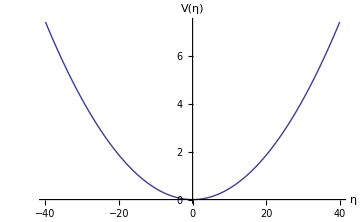

0.1

Backbone spring constant κ:

1.2

Residue-pair spring constant σ(ϵ = 0.0045):

0.00024

κ/σ ratio:

5000.

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

PotentialData = Import["potential_data.out","Table"];

PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];

Subscript[R, pfmxd]=Import["pfmxd_r.out","Table"];
Subscript[R, mxd]=Import["mxd_r.out","Table"];

Subscript[λ, pfmxd]=Import["pfmxd_lambda.out","Table"];
Subscript[λ, mxd]=Import["mxd_lambda.out","Table"];

Subscript[ρ, pfmxd]=Import["pfmxd_roe.out","Table"];
Subscript[ρ, mxd]=Import["mxd_roe.out","Table"];

Parameters=Import["Parameters"];
Grid[Parameters]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

ϵ=Parameters[[17,2]];
β=Parameters[[18,2]];

L=Parameters[[1,2]];
m=Parameters[[2,2]];
Δ=Parameters[[6,2]]
Print["Backbone spring constant κ:"]
κ=Parameters[[3,2]]
Print["Residue-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[4,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[5,2]]
umax=Parameters[[7,2]];
umax=Parameters[[8,2]];

n=ToExpression[StringTrim[Last[StringSplit[Directory[],"/"]],RegularExpression["N*"]]];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

Subscript[η, B]=4.0;

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f (κ/(2β))^(1/2)) ToNewton;
ToDimension[η_]:=η ((κ β)/2)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]](*Å*)
```

4.

0.830293

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

0.319267

99.7708

Partition function & Free Energy

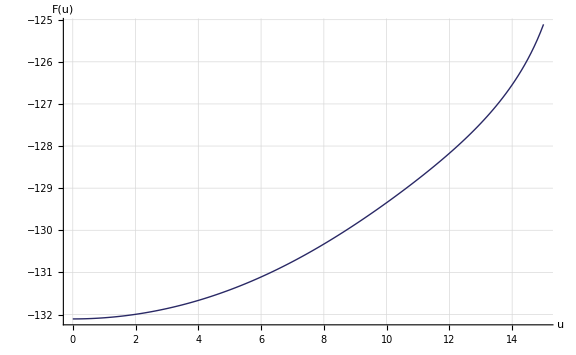
{-Graphics-,-Graphics-}

```mathematica
pIntactPF=ListLinePlot[PartitionFunction,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["Z(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

pIntactFE=ListLinePlot[FreeEnergy,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

{pIntactPF,pIntactFE}
```

Residue-pair separations (x-z), (x-y), (z-y)

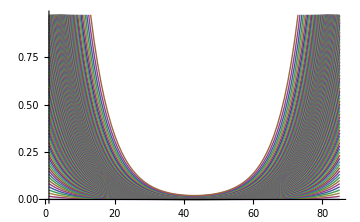
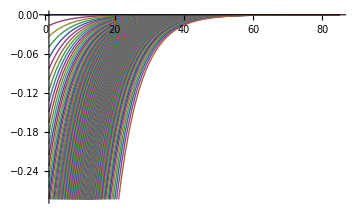

3.98726

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.016596 | 0.014253 | 0.0122407 | 0.0105126 | 0.00902841 | 0.00775379 | 0.00665912 | 0.00571901 | 0.00491163 | 0.00421824 | 0.00362276 | 0.00311136 | 0.00267217 | 0.00229499 | 0.00197108 | 0.00169292 | 0.00145405 | 0.00124893 | 0.00107279 | 0.000921553 | 0.000791703 | 0.000680227 | 0.000584539 | 0.000502417 | 0.000431956 | 0.00037152 | 0.000319707 | 0.000275314 | 0.00023731 | 0.000204815 | 0.000177073 | 0.00015344 | 0.000133369 | 0.000116393 | 0.000102119 | 0.0000902143 | 0.0000804037 | 0.0000724591 | 0.0000661963 | 0.0000614698 | 0.00005817 | 0.0000562203 | 0.0000555754 | 0.0000562203 | 0.00005817 | 0.0000614698 | 0.0000661963 | 0.0000724591 | 0.0000804037 | 0.0000902143 | 0.000102119 | 0.000116393 | 0.000133369 | 0.00015344 | 0.000177073 | 0.000204815 | 0.00023731 | 0.000275314 | 0.000319707 | 0.00037152 | 0.000431956 | 0.000502417 | 0.000584539 | 0.000680227 | 0.000791703 | 0.000921553 | 0.00107279 | 0.00124893 | 0.00145405 | 0.00169292 | 0.00197108 | 0.00229499 | 0.00267217 | 0.00311136 | 0.00362276 | 0.00421825 | 0.00491163 | 0.00571901 | 0.00665912 | 0.00775379 | 0.00902841 | 0.0105126 | 0.0122407 | 0.014253 | 0.016596
0.0331931 | 0.0285068 | 0.0244822 | 0.0210258 | 0.0180574 | 0.0155081 | 0.0133187 | 0.0114384 | 0.00982357 | 0.00843676 | 0.00724575 | 0.00622291 | 0.0053445 | 0.00459013 | 0.00394229 | 0.00338595 | 0.0029082 | 0.00249794 | 0.00214565 | 0.00184316 | 0.00158346 | 0.0013605 | 0.00116911 | 0.00100487 | 0.000863939 | 0.000743064 | 0.000639434 | 0.000550645 | 0.000474636 | 0.000409642 | 0.000354156 | 0.00030689 | 0.000266746 | 0.000232794 | 0.000204244 | 0.000180434 | 0.000160812 | 0.000144923 | 0.000132397 | 0.000122944 | 0.000116344 | 0.000112444 | 0.000111154 | 0.000112444 | 0.000116344 | 0.000122944 | 0.000132397 | 0.000144923 | 0.000160812 | 0.000180434 | 0.000204244 | 0.000232794 | 0.000266746 | 0.00030689 | 0.000354156 | 0.000409642 | 0.000474636 | 0.000550645 | 0.000639434 | 0.000743064 | 0.000863939 | 0.00100487 | 0.00116911 | 0.0013605 | 0.00158346 | 0.00184316 | 0.00214565 | 0.00249794 | 0.0029082 | 0.00338595 | 0.00394229 | 0.00459013 | 0.0053445 | 0.00622291 | 0.00724575 | 0.00843676 | 0.00982357 | 0.0114384 | 0.0133187 | 0.0155081 | 0.0180574 | 0.0210258 | 0.0244822 | 0.0285068 | 0.0331931
0.0497922 | 0.0427625 | 0.0367253 | 0.0315404 | 0.0270875 | 0.0232633 | 0.0199791 | 0.0171585 | 0.0147361 | 0.0126558 | 0.0108692 | 0.00933486 | 0.00801718 | 0.00688556 | 0.00591375 | 0.0050792 | 0.00436253 | 0.0037471 | 0.00321865 | 0.00276489 | 0.00237531 | 0.00204085 | 0.00175376 | 0.00150738 | 0.00129598 | 0.00111465 | 0.000959202 | 0.000826011 | 0.000711991 | 0.000614496 | 0.000531263 | 0.000460359 | 0.000400141 | 0.000349209 | 0.000306382 | 0.000270666 | 0.000241231 | 0.000217396 | 0.000198606 | 0.000184425 | 0.000174525 | 0.000168675 | 0.00016674 | 0.000168675 | 0.000174525 | 0.000184425 | 0.000198606 | 0.000217396 | 0.000241231 | 0.000270666 | 0.000306382 | 0.000349209 | 0.000400141 | 0.000460359 | 0.000531263 | 0.000614496 | 0.000711991 | 0.000826011 | 0.000959202 | 0.00111465 | 0.00129598 | 0.00150738 | 0.00175376 | 0.00204085 | 0.00237531 | 0.00276489 | 0.00321865 | 0.0037471 | 0.00436253 | 0.0050792 | 0.00591375 | 0.00688556 | 0.00801718 | 0.00933486 | 0.0108692 | 0.0126558 | 0.0147361 | 0.0171585 | 0.0199791 | 0.0232633 | 0.0270875 | 0.0315404 | 0.0367253 | 0.0427625 | 0.0497922
0.0663945 | 0.0570209 | 0.0489706 | 0.0420569 | 0.0361193 | 0.0310201 | 0.0266407 | 0.0228797 | 0.0196496 | 0.0168757 | 0.0144933 | 0.0124474 | 0.0106904 | 0.00918143 | 0.00788559 | 0.00677276 | 0.00581713 | 0.00499651 | 0.00429185 | 0.0036868 | 0.00316731 | 0.00272134 | 0.00233853 | 0.00200999 | 0.0017281 | 0.00148632 | 0.00127903 | 0.00110143 | 0.000949392 | 0.000819389 | 0.000708403 | 0.000613858 | 0.000533561 | 0.000465646 | 0.000408539 | 0.000360914 | 0.000321666 | 0.000289882 | 0.000264827 | 0.000245918 | 0.000232717 | 0.000224917 | 0.000222337 | 0.000224917 | 0.000232717 | 0.000245918 | 0.000264827 | 0.000289883 | 0.000321666 | 0.000360914 | 0.000408539 | 0.000465646 | 0.00053356 | 0.000613858 | 0.000708403 | 0.000819389 | 0.000949392 | 0.00110143 | 0.00127903 | 0.00148632 | 0.0017281 | 0.00200999 | 0.00233852 | 0.00272134 | 0.00316731 | 0.0036868 | 0.00429185 | 0.00499651 | 0.00581713 | 0.00677277 | 0.00788559 | 0.00918143 | 0.0106904 | 0.0124474 | 0.0144933 | 0.0168757 | 0.0196496 | 0.0228797 | 0.0266407 | 0.0310201 | 0.0361193 | 0.0420569 | 0.0489706 | 0.0570209 | 0.0663945
0.083001 | 0.0712829 | 0.0612191 | 0.0525762 | 0.0451535 | 0.0387788 | 0.033304 | 0.0286023 | 0.0245644 | 0.0210966 | 0.0181184 | 0.0155607 | 0.0133642 | 0.0114779 | 0.00985792 | 0.00846676 | 0.0072721 | 0.00624623 | 0.00536532 | 0.00460893 | 0.00395952 | 0.003402 | 0.00292343 | 0.00251272 | 0.00216033 | 0.00185807 | 0.00159894 | 0.00137692 | 0.00118685 | 0.00102433 | 0.000885587 | 0.000767395 | 0.000667014 | 0.000582113 | 0.000510723 | 0.000451186 | 0.00040212 | 0.000362387 | 0.000331065 | 0.000307427 | 0.000290924 | 0.000281173 | 0.000277947 | 0.000281173 | 0.000290924 | 0.000307427 | 0.000331065 | 0.000362388 | 0.00040212 | 0.000451186 | 0.000510723 | 0.000582113 | 0.000667014 | 0.000767395 | 0.000885587 | 0.00102433 | 0.00118685 | 0.00137692 | 0.00159894 | 0.00185807 | 0.00216033 | 0.00251272 | 0.00292343 | 0.003402 | 0.00395952 | 0.00460893 | 0.00536532 | 0.00624623 | 0.0072721 | 0.00846676 | 0.00985792 | 0.0114779 | 0.0133642 | 0.0155607 | 0.0181184 | 0.0210966 | 0.0245644 | 0.0286023 | 0.033304 | 0.0387788 | 0.0451535 | 0.0525762 | 0.0612191 | 0.0712829 | 0.083001
0.0996128 | 0.0855493 | 0.0734714 | 0.0630987 | 0.0541904 | 0.0465399 | 0.0399695 | 0.0343267 | 0.0294807 | 0.0253188 | 0.0217446 | 0.018675 | 0.0160389 | 0.013775 | 0.0118309 | 0.0101613 | 0.00872753 | 0.00749634 | 0.00643913 | 0.00553136 | 0.00475197 | 0.00408287 | 0.00350853 | 0.00301561 | 0.00259269 | 0.00222994 | 0.00191895 | 0.00165249 | 0.00142439 | 0.00122934 | 0.00106283 | 0.000920981 | 0.000800509 | 0.000698617 | 0.000612938 | 0.000541485 | 0.0004826 | 0.000434915 | 0.000397324 | 0.000368955 | 0.000349149 | 0.000337446 | 0.000333575 | 0.000337446 | 0.000349149 | 0.000368955 | 0.000397324 | 0.000434915 | 0.0004826 | 0.000541485 | 0.000612938 | 0.000698617 | 0.000800509 | 0.000920981 | 0.00106283 | 0.00122934 | 0.00142439 | 0.00165249 | 0.00191895 | 0.00222994 | 0.00259269 | 0.00301562 | 0.00350853 | 0.00408287 | 0.00475197 | 0.00553136 | 0.00643913 | 0.00749634 | 0.00872753 | 0.0101613 | 0.0118309 | 0.013775 | 0.0160389 | 0.018675 | 0.0217446 | 0.0253188 | 0.0294807 | 0.0343267 | 0.0399695 | 0.0465399 | 0.0541904 | 0.0630987 | 0.0734714 | 0.0855493 | 0.0996128
0.116231 | 0.0998212 | 0.0857284 | 0.0736252 | 0.0632308 | 0.0543039 | 0.0466374 | 0.0400533 | 0.0343988 | 0.0295427 | 0.0253721 | 0.0217905 | 0.0187146 | 0.0160731 | 0.0138046 | 0.0118565 | 0.0101835 | 0.00874692 | 0.00751334 | 0.00645413 | 0.00554472 | 0.004764 | 0.00409384 | 0.0035187 | 0.00302522 | 0.00260195 | 0.00223908 | 0.00192817 | 0.00166201 | 0.00143443 | 0.00124014 | 0.00107462 | 0.000934055 | 0.000815164 | 0.000715192 | 0.000631819 | 0.00056311 | 0.00050747 | 0.000463609 | 0.000430507 | 0.000407396 | 0.000393741 | 0.000389224 | 0.000393741 | 0.000407396 | 0.000430507 | 0.000463609 | 0.00050747 | 0.00056311 | 0.000631819 | 0.000715192 | 0.000815164 | 0.000934055 | 0.00107462 | 0.00124014 | 0.00143443 | 0.00166201 | 0.00192817 | 0.00223908 | 0.00260196 | 0.00302522 | 0.0035187 | 0.00409384 | 0.004764 | 0.00554472 | 0.00645413 | 0.00751334 | 0.00874692 | 0.0101835 | 0.0118565 | 0.0138046 | 0.0160731 | 0.0187146 | 0.0217905 | 0.0253722 | 0.0295426 | 0.0343988 | 0.0400533 | 0.0466374 | 0.0543039 | 0.0632308 | 0.0736252 | 0.0857283 | 0.0998212 | 0.116231
0.132856 | 0.114099 | 0.0979907 | 0.0841563 | 0.0722751 | 0.0620714 | 0.0533083 | 0.0457824 | 0.0393191 | 0.0337683 | 0.0290013 | 0.0249074 | 0.0213915 | 0.0183721 | 0.0157791 | 0.0135524 | 0.0116401 | 0.00999805 | 0.00858802 | 0.00737731 | 0.00633782 | 0.00544542 | 0.00467941 | 0.004022 | 0.00345794 | 0.00297413 | 0.00255935 | 0.00220397 | 0.00189974 | 0.0016396 | 0.00141752 | 0.00122834 | 0.00106766 | 0.000931762 | 0.000817491 | 0.000722193 | 0.000643656 | 0.000580057 | 0.000529922 | 0.000492085 | 0.000465669 | 0.000450061 | 0.000444898 | 0.000450061 | 0.000465669 | 0.000492085 | 0.000529922 | 0.000580057 | 0.000643656 | 0.000722193 | 0.000817491 | 0.000931762 | 0.00106766 | 0.00122834 | 0.00141752 | 0.0016396 | 0.00189974 | 0.00220397 | 0.00255935 | 0.00297413 | 0.00345794 | 0.004022 | 0.00467941 | 0.00544542 | 0.00633782 | 0.00737731 | 0.00858802 | 0.00999805 | 0.0116401 | 0.0135524 | 0.0157791 | 0.0183721 | 0.0213915 | 0.0249074 | 0.0290013 | 0.0337683 | 0.0393191 | 0.0457824 | 0.0533083 | 0.0620714 | 0.0722751 | 0.0841563 | 0.0979907 | 0.114099 | 0.132856
0.14949 | 0.128384 | 0.110259 | 0.0946927 | 0.081324 | 0.0698427 | 0.0599825 | 0.0515144 | 0.0442418 | 0.0379961 | 0.0326323 | 0.0280258 | 0.0240697 | 0.0206723 | 0.0177547 | 0.0152491 | 0.0130975 | 0.0112498 | 0.00966324 | 0.00830095 | 0.00713131 | 0.00612719 | 0.00526527 | 0.00452555 | 0.00389087 | 0.00334649 | 0.00287978 | 0.00247991 | 0.00213759 | 0.00184488 | 0.00159499 | 0.00138212 | 0.00120133 | 0.00104842 | 0.000919841 | 0.000812611 | 0.000724241 | 0.00065268 | 0.000596268 | 0.000553694 | 0.00052397 | 0.000506408 | 0.000500599 | 0.000506408 | 0.00052397 | 0.000553694 | 0.000596268 | 0.00065268 | 0.000724241 | 0.000812611 | 0.000919841 | 0.00104842 | 0.00120133 | 0.00138212 | 0.00159499 | 0.00184488 | 0.00213759 | 0.00247991 | 0.00287978 | 0.00334649 | 0.00389087 | 0.00452555 | 0.00526527 | 0.00612719 | 0.00713131 | 0.00830095 | 0.00966324 | 0.0112498 | 0.0130975 | 0.0152491 | 0.0177547 | 0.0206723 | 0.0240697 | 0.0280258 | 0.0326323 | 0.0379961 | 0.0442418 | 0.0515144 | 0.0599825 | 0.0698427 | 0.081324 | 0.0946927 | 0.110259 | 0.128385 | 0.14949
0.166132 | 0.142678 | 0.122534 | 0.105235 | 0.0903779 | 0.0776184 | 0.0666604 | 0.0572495 | 0.0491673 | 0.0422263 | 0.0362652 | 0.0311459 | 0.0267494 | 0.0229738 | 0.0197313 | 0.0169468 | 0.0145556 | 0.0125023 | 0.0107391 | 0.0092251 | 0.00792525 | 0.00680934 | 0.00585146 | 0.00502939 | 0.00432405 | 0.00371906 | 0.00320039 | 0.002756 | 0.00237557 | 0.00205027 | 0.00177257 | 0.001536 | 0.00133508 | 0.00116514 | 0.00102225 | 0.00090308 | 0.000804872 | 0.000725344 | 0.000662651 | 0.000615337 | 0.000582305 | 0.000562787 | 0.000556331 | 0.000562787 | 0.000582305 | 0.000615337 | 0.000662651 | 0.000725344 | 0.000804872 | 0.00090308 | 0.00102225 | 0.00116514 | 0.00133507 | 0.001536 | 0.00177257 | 0.00205027 | 0.00237557 | 0.002756 | 0.00320039 | 0.00371906 | 0.00432405 | 0.00502939 | 0.00585146 | 0.00680934 | 0.00792525 | 0.0092251 | 0.0107391 | 0.0125023 | 0.0145556 | 0.0169468 | 0.0197313 | 0.0229738 | 0.0267494 | 0.0311459 | 0.0362652 | 0.0422263 | 0.0491673 | 0.0572495 | 0.0666604 | 0.0776184 | 0.0903779 | 0.105235 | 0.122534 | 0.142678 | 0.166132
0.182785 | 0.15698 | 0.134817 | 0.115784 | 0.0994373 | 0.0853989 | 0.0733424 | 0.0629882 | 0.0540959 | 0.046459 | 0.0399005 | 0.034268 | 0.0294308 | 0.0252767 | 0.0217092 | 0.0186456 | 0.0160147 | 0.0137555 | 0.0118155 | 0.0101498 | 0.00871968 | 0.0074919 | 0.00643801 | 0.00553353 | 0.00475749 | 0.00409186 | 0.0035212 | 0.00303226 | 0.00261369 | 0.00225579 | 0.00195025 | 0.00168996 | 0.0014689 | 0.00128193 | 0.00112472 | 0.000993604 | 0.000885552 | 0.000798052 | 0.000729075 | 0.000677018 | 0.000640675 | 0.000619201 | 0.000612097 | 0.000619201 | 0.000640675 | 0.000677018 | 0.000729075 | 0.000798052 | 0.000885552 | 0.000993604 | 0.00112472 | 0.00128193 | 0.0014689 | 0.00168996 | 0.00195025 | 0.00225579 | 0.00261369 | 0.00303226 | 0.0035212 | 0.00409186 | 0.00475749 | 0.00553353 | 0.00643801 | 0.0074919 | 0.00871968 | 0.0101498 | 0.0118155 | 0.0137555 | 0.0160147 | 0.0186456 | 0.0217092 | 0.0252767 | 0.0294308 | 0.034268 | 0.0399005 | 0.046459 | 0.0540959 | 0.0629882 | 0.0733424 | 0.0853989 | 0.0994373 | 0.115784 | 0.134817 | 0.15698 | 0.182785
0.19945 | 0.171291 | 0.147108 | 0.126339 | 0.108503 | 0.0931845 | 0.0800289 | 0.0687307 | 0.0590277 | 0.0506946 | 0.0435381 | 0.0373921 | 0.0321139 | 0.0275811 | 0.0236884 | 0.0203454 | 0.0174747 | 0.0150096 | 0.0128927 | 0.0110752 | 0.00951464 | 0.00817493 | 0.00702495 | 0.00603802 | 0.00519122 | 0.00446491 | 0.00384222 | 0.0033087 | 0.00285198 | 0.00246145 | 0.00212805 | 0.00184404 | 0.00160282 | 0.00139881 | 0.00122726 | 0.00108419 | 0.000966287 | 0.00087081 | 0.000795543 | 0.000738741 | 0.000699084 | 0.000675652 | 0.000667902 | 0.000675652 | 0.000699084 | 0.000738741 | 0.000795543 | 0.00087081 | 0.000966287 | 0.00108419 | 0.00122726 | 0.00139881 | 0.00160282 | 0.00184404 | 0.00212805 | 0.00246145 | 0.00285198 | 0.0033087 | 0.00384222 | 0.00446491 | 0.00519122 | 0.00603802 | 0.00702495 | 0.00817493 | 0.00951464 | 0.0110752 | 0.0128928 | 0.0150096 | 0.0174747 | 0.0203454 | 0.0236884 | 0.0275811 | 0.0321139 | 0.0373921 | 0.0435381 | 0.0506946 | 0.0590277 | 0.0687307 | 0.0800289 | 0.0931845 | 0.108503 | 0.126339 | 0.147108 | 0.171291 | 0.19945
0.216126 | 0.185613 | 0.159408 | 0.136903 | 0.117575 | 0.100976 | 0.0867203 | 0.0744775 | 0.0639631 | 0.0549333 | 0.0471784 | 0.0405186 | 0.0347991 | 0.0298872 | 0.025669 | 0.0220466 | 0.0189358 | 0.0162645 | 0.0139707 | 0.0120012 | 0.0103102 | 0.00885845 | 0.00761232 | 0.00654287 | 0.00562527 | 0.00483823 | 0.00416347 | 0.00358535 | 0.00309044 | 0.00266726 | 0.00230598 | 0.00199822 | 0.00173684 | 0.00151576 | 0.00132987 | 0.00117484 | 0.00104708 | 0.00094362 | 0.000862061 | 0.000800509 | 0.000757536 | 0.000732145 | 0.000723746 | 0.000732145 | 0.000757536 | 0.000800509 | 0.000862061 | 0.00094362 | 0.00104708 | 0.00117484 | 0.00132987 | 0.00151576 | 0.00173684 | 0.00199822 | 0.00230598 | 0.00266726 | 0.00309044 | 0.00358535 | 0.00416347 | 0.00483823 | 0.00562527 | 0.00654287 | 0.00761232 | 0.00885845 | 0.0103102 | 0.0120012 | 0.0139707 | 0.0162645 | 0.0189358 | 0.0220466 | 0.025669 | 0.0298872 | 0.0347991 | 0.0405186 | 0.0471785 | 0.0549333 | 0.0639631 | 0.0744775 | 0.0867203 | 0.100976 | 0.117575 | 0.136903 | 0.159408 | 0.185613 | 0.216126
0.232816 | 0.199947 | 0.171718 | 0.147475 | 0.126654 | 0.108773 | 0.093417 | 0.0802287 | 0.0689024 | 0.0591753 | 0.0508216 | 0.0436474 | 0.0374863 | 0.0321951 | 0.0276512 | 0.023749 | 0.0203981 | 0.0175205 | 0.0150496 | 0.0129279 | 0.0111063 | 0.00954251 | 0.00820016 | 0.00704812 | 0.00605966 | 0.00521184 | 0.00448498 | 0.00386222 | 0.00332909 | 0.00287323 | 0.00248405 | 0.00215252 | 0.00187096 | 0.00163281 | 0.00143256 | 0.00126556 | 0.00112794 | 0.00101649 | 0.00092863 | 0.000862325 | 0.000816034 | 0.000788682 | 0.000779635 | 0.000788682 | 0.000816034 | 0.000862325 | 0.00092863 | 0.00101649 | 0.00112794 | 0.00126556 | 0.00143256 | 0.00163281 | 0.00187096 | 0.00215252 | 0.00248405 | 0.00287323 | 0.00332909 | 0.00386222 | 0.00448498 | 0.00521184 | 0.00605966 | 0.00704812 | 0.00820016 | 0.00954251 | 0.0111063 | 0.0129279 | 0.0150496 | 0.0175205 | 0.0203981 | 0.023749 | 0.0276512 | 0.0321951 | 0.0374863 | 0.0436475 | 0.0508216 | 0.0591753 | 0.0689024 | 0.0802287 | 0.093417 | 0.108773 | 0.126654 | 0.147475 | 0.171718 | 0.199947 | 0.232816
0.249519 | 0.214292 | 0.184038 | 0.158055 | 0.135741 | 0.116577 | 0.100119 | 0.0859847 | 0.0738459 | 0.0634209 | 0.0544679 | 0.046779 | 0.0401758 | 0.034505 | 0.0296351 | 0.0254529 | 0.0218615 | 0.0187775 | 0.0161293 | 0.0138555 | 0.0119032 | 0.0102271 | 0.00878848 | 0.00755379 | 0.00649441 | 0.00558577 | 0.00480676 | 0.00413931 | 0.00356794 | 0.00307937 | 0.00266227 | 0.00230696 | 0.00200519 | 0.00174996 | 0.00153534 | 0.00135636 | 0.00120886 | 0.00108942 | 0.000995255 | 0.000924193 | 0.000874581 | 0.000845266 | 0.00083557 | 0.000845266 | 0.000874581 | 0.000924193 | 0.000995255 | 0.00108942 | 0.00120886 | 0.00135636 | 0.00153534 | 0.00174996 | 0.00200519 | 0.00230696 | 0.00266227 | 0.00307937 | 0.00356794 | 0.00413931 | 0.00480676 | 0.00558577 | 0.00649441 | 0.00755379 | 0.00878848 | 0.0102271 | 0.0119032 | 0.0138555 | 0.0161293 | 0.0187775 | 0.0218615 | 0.0254529 | 0.0296351 | 0.034505 | 0.0401758 | 0.046779 | 0.0544678 | 0.0634209 | 0.0738459 | 0.0859847 | 0.100119 | 0.116577 | 0.135741 | 0.158055 | 0.184038 | 0.214292 | 0.249519
0.266238 | 0.22865 | 0.196369 | 0.168645 | 0.144836 | 0.124388 | 0.106827 | 0.0917459 | 0.0787937 | 0.0676702 | 0.0581173 | 0.0499132 | 0.0428676 | 0.0368169 | 0.0316207 | 0.0271583 | 0.0233263 | 0.0200356 | 0.01721 | 0.0147838 | 0.0127007 | 0.0109124 | 0.00937733 | 0.00805991 | 0.00692955 | 0.00596002 | 0.00512882 | 0.00441666 | 0.003807 | 0.00328569 | 0.00284065 | 0.00246153 | 0.00213954 | 0.00186721 | 0.00163821 | 0.00144724 | 0.00128986 | 0.00116241 | 0.00106194 | 0.000986116 | 0.000933179 | 0.000901901 | 0.000891555 | 0.000901901 | 0.000933179 | 0.000986116 | 0.00106194 | 0.00116241 | 0.00128986 | 0.00144724 | 0.00163821 | 0.00186721 | 0.00213954 | 0.00246153 | 0.00284065 | 0.00328569 | 0.003807 | 0.00441666 | 0.00512882 | 0.00596002 | 0.00692955 | 0.00805991 | 0.00937733 | 0.0109124 | 0.0127007 | 0.0147838 | 0.01721 | 0.0200357 | 0.0233263 | 0.0271583 | 0.0316207 | 0.0368169 | 0.0428676 | 0.0499132 | 0.0581173 | 0.0676702 | 0.0787937 | 0.0917459 | 0.106827 | 0.124388 | 0.144836 | 0.168645 | 0.196369 | 0.22865 | 0.266237
0.282971 | 0.243021 | 0.208711 | 0.179245 | 0.15394 | 0.132207 | 0.113542 | 0.0975124 | 0.0837461 | 0.0719235 | 0.0617702 | 0.0530505 | 0.045562 | 0.039131 | 0.0336081 | 0.0288653 | 0.0247924 | 0.021295 | 0.0182917 | 0.015713 | 0.013499 | 0.0115983 | 0.00996672 | 0.0085665 | 0.0073651 | 0.00633463 | 0.00545119 | 0.00469426 | 0.00404628 | 0.00349221 | 0.00301919 | 0.00261624 | 0.00227402 | 0.00198457 | 0.00174118 | 0.00153821 | 0.00137093 | 0.00123547 | 0.00112869 | 0.0010481 | 0.000991833 | 0.000958589 | 0.000947592 | 0.000958589 | 0.000991833 | 0.0010481 | 0.00112869 | 0.00123547 | 0.00137093 | 0.00153821 | 0.00174118 | 0.00198457 | 0.00227402 | 0.00261624 | 0.00301919 | 0.00349221 | 0.00404628 | 0.00469426 | 0.00545119 | 0.00633463 | 0.0073651 | 0.0085665 | 0.00996672 | 0.0115983 | 0.013499 | 0.015713 | 0.0182917 | 0.021295 | 0.0247924 | 0.0288653 | 0.0336081 | 0.039131 | 0.045562 | 0.0530505 | 0.0617702 | 0.0719235 | 0.0837462 | 0.0975124 | 0.113542 | 0.132207 | 0.15394 | 0.179245 | 0.208711 | 0.243021 | 0.282971
0.299722 | 0.257407 | 0.221066 | 0.189856 | 0.163052 | 0.140032 | 0.120263 | 0.103285 | 0.0887035 | 0.076181 | 0.0654267 | 0.0561908 | 0.048259 | 0.0414473 | 0.0355976 | 0.030574 | 0.02626 | 0.0225555 | 0.0193745 | 0.0166431 | 0.0142981 | 0.0122848 | 0.0105567 | 0.00907359 | 0.00780107 | 0.00670961 | 0.00577387 | 0.00497213 | 0.0042858 | 0.00369893 | 0.00319791 | 0.00277111 | 0.00240863 | 0.00210205 | 0.00184425 | 0.00162926 | 0.00145208 | 0.0013086 | 0.0011955 | 0.00111014 | 0.00105054 | 0.00101533 | 0.00100368 | 0.00101533 | 0.00105054 | 0.00111014 | 0.0011955 | 0.0013086 | 0.00145208 | 0.00162926 | 0.00184425 | 0.00210205 | 0.00240863 | 0.00277111 | 0.00319791 | 0.00369893 | 0.0042858 | 0.00497213 | 0.00577387 | 0.00670961 | 0.00780107 | 0.00907359 | 0.0105567 | 0.0122848 | 0.0142981 | 0.0166431 | 0.0193745 | 0.0225555 | 0.02626 | 0.030574 | 0.0355976 | 0.0414473 | 0.048259 | 0.0561908 | 0.0654267 | 0.076181 | 0.0887035 | 0.103285 | 0.120263 | 0.140033 | 0.163052 | 0.189856 | 0.221066 | 0.257407 | 0.299722
0.31649 | 0.271807 | 0.233433 | 0.200477 | 0.172174 | 0.147866 | 0.126991 | 0.109063 | 0.0936659 | 0.0804429 | 0.0690869 | 0.0593343 | 0.0509588 | 0.0437661 | 0.037589 | 0.0322844 | 0.0277291 | 0.0238174 | 0.0204584 | 0.0175742 | 0.015098 | 0.0129721 | 0.0111473 | 0.00958121 | 0.0082375 | 0.00708497 | 0.00609688 | 0.0052503 | 0.00452556 | 0.00390586 | 0.00337682 | 0.00292614 | 0.00254338 | 0.00221964 | 0.00194743 | 0.00172041 | 0.00153332 | 0.00138181 | 0.00126238 | 0.00117224 | 0.00110932 | 0.00107213 | 0.00105984 | 0.00107213 | 0.00110932 | 0.00117224 | 0.00126238 | 0.00138181 | 0.00153332 | 0.00172041 | 0.00194743 | 0.00221964 | 0.00254338 | 0.00292614 | 0.00337682 | 0.00390586 | 0.00452556 | 0.0052503 | 0.00609688 | 0.00708497 | 0.0082375 | 0.00958121 | 0.0111473 | 0.0129721 | 0.015098 | 0.0175742 | 0.0204584 | 0.0238174 | 0.0277291 | 0.0322844 | 0.037589 | 0.0437661 | 0.0509588 | 0.0593343 | 0.0690869 | 0.0804429 | 0.0936659 | 0.109063 | 0.126991 | 0.147867 | 0.172174 | 0.200477 | 0.233433 | 0.271807 | 0.31649
0.333275 | 0.286223 | 0.245814 | 0.21111 | 0.181305 | 0.155709 | 0.133726 | 0.114847 | 0.0986337 | 0.0847094 | 0.0727511 | 0.0624812 | 0.0536616 | 0.0460873 | 0.0395827 | 0.0339967 | 0.0291998 | 0.0250806 | 0.0215434 | 0.0185063 | 0.0158987 | 0.0136601 | 0.0117385 | 0.0100894 | 0.00867439 | 0.00746074 | 0.00642025 | 0.00552876 | 0.00476559 | 0.00411302 | 0.00355591 | 0.00308133 | 0.00267827 | 0.00233737 | 0.00205071 | 0.00181165 | 0.00161464 | 0.0014551 | 0.00132933 | 0.00123442 | 0.00116815 | 0.001129 | 0.00111605 | 0.001129 | 0.00116815 | 0.00123442 | 0.00132933 | 0.0014551 | 0.00161464 | 0.00181165 | 0.00205071 | 0.00233737 | 0.00267827 | 0.00308133 | 0.00355591 | 0.00411302 | 0.00476559 | 0.00552876 | 0.00642024 | 0.00746074 | 0.00867439 | 0.0100894 | 0.0117385 | 0.0136601 | 0.0158987 | 0.0185063 | 0.0215434 | 0.0250806 | 0.0291998 | 0.0339967 | 0.0395827 | 0.0460873 | 0.0536615 | 0.0624812 | 0.0727511 | 0.0847094 | 0.0986337 | 0.114847 | 0.133726 | 0.155709 | 0.181305 | 0.21111 | 0.245814 | 0.286223 | 0.333275
0.35008 | 0.300655 | 0.258208 | 0.221754 | 0.190447 | 0.16356 | 0.140469 | 0.120638 | 0.103607 | 0.0889806 | 0.0764193 | 0.0656317 | 0.0563673 | 0.0484111 | 0.0415785 | 0.0357109 | 0.0306721 | 0.0263452 | 0.0226297 | 0.0194394 | 0.0167004 | 0.0143489 | 0.0123304 | 0.0105981 | 0.00911177 | 0.00783693 | 0.00674397 | 0.00580753 | 0.00500588 | 0.00432041 | 0.00373521 | 0.0032367 | 0.00281331 | 0.00245522 | 0.00215411 | 0.001903 | 0.00169605 | 0.00152847 | 0.00139636 | 0.00129666 | 0.00122705 | 0.00118592 | 0.00117232 | 0.00118592 | 0.00122705 | 0.00129666 | 0.00139636 | 0.00152847 | 0.00169605 | 0.001903 | 0.00215411 | 0.00245522 | 0.00281332 | 0.0032367 | 0.00373521 | 0.00432041 | 0.00500588 | 0.00580753 | 0.00674397 | 0.00783693 | 0.00911177 | 0.0105981 | 0.0123304 | 0.0143489 | 0.0167003 | 0.0194394 | 0.0226297 | 0.0263452 | 0.0306721 | 0.0357109 | 0.0415785 | 0.0484111 | 0.0563673 | 0.0656317 | 0.0764193 | 0.0889806 | 0.103607 | 0.120638 | 0.140469 | 0.16356 | 0.190447 | 0.221754 | 0.258208 | 0.300655 | 0.35008
0.366903 | 0.315104 | 0.270617 | 0.232411 | 0.1996 | 0.17142 | 0.147219 | 0.126436 | 0.108586 | 0.0932567 | 0.0800918 | 0.0687857 | 0.0590761 | 0.0507376 | 0.0435766 | 0.037427 | 0.0321461 | 0.0276112 | 0.0237172 | 0.0203736 | 0.0175029 | 0.0150384 | 0.0129229 | 0.0111074 | 0.00954966 | 0.00821354 | 0.00706806 | 0.00608662 | 0.00524644 | 0.00452803 | 0.00391471 | 0.00339225 | 0.00294851 | 0.00257321 | 0.00225763 | 0.00199445 | 0.00177756 | 0.00160192 | 0.00146346 | 0.00135897 | 0.00128602 | 0.00124292 | 0.00122866 | 0.00124292 | 0.00128602 | 0.00135897 | 0.00146346 | 0.00160192 | 0.00177756 | 0.00199445 | 0.00225763 | 0.00257321 | 0.00294851 | 0.00339225 | 0.00391471 | 0.00452803 | 0.00524644 | 0.00608662 | 0.00706806 | 0.00821354 | 0.00954966 | 0.0111074 | 0.0129229 | 0.0150384 | 0.0175029 | 0.0203736 | 0.0237172 | 0.0276112 | 0.0321461 | 0.037427 | 0.0435766 | 0.0507376 | 0.0590761 | 0.0687857 | 0.0800918 | 0.0932567 | 0.108586 | 0.126436 | 0.147219 | 0.17142 | 0.1996 | 0.232411 | 0.270617 | 0.315104 | 0.366903
0.383747 | 0.329569 | 0.283041 | 0.243081 | 0.208763 | 0.17929 | 0.153978 | 0.13224 | 0.113571 | 0.0975379 | 0.0837686 | 0.0719435 | 0.0617882 | 0.0530668 | 0.0455771 | 0.0391452 | 0.0336219 | 0.0288788 | 0.024806 | 0.021309 | 0.0183064 | 0.0157288 | 0.0135162 | 0.0116173 | 0.00998806 | 0.00859061 | 0.00739254 | 0.00636604 | 0.0054873 | 0.0047359 | 0.00409443 | 0.00354798 | 0.00308387 | 0.00269134 | 0.00236128 | 0.00208601 | 0.00185916 | 0.00167546 | 0.00153065 | 0.00142136 | 0.00134506 | 0.00129997 | 0.00128506 | 0.00129997 | 0.00134506 | 0.00142136 | 0.00153065 | 0.00167546 | 0.00185916 | 0.00208601 | 0.00236128 | 0.00269134 | 0.00308387 | 0.00354798 | 0.00409443 | 0.0047359 | 0.0054873 | 0.00636604 | 0.00739254 | 0.00859061 | 0.00998806 | 0.0116173 | 0.0135162 | 0.0157288 | 0.0183064 | 0.021309 | 0.024806 | 0.0288788 | 0.0336219 | 0.0391452 | 0.0455771 | 0.0530668 | 0.0617882 | 0.0719435 | 0.0837686 | 0.097538 | 0.113571 | 0.13224 | 0.153978 | 0.17929 | 0.208763 | 0.243081 | 0.283041 | 0.329569 | 0.383747
0.400612 | 0.344053 | 0.295479 | 0.253763 | 0.217937 | 0.187169 | 0.160745 | 0.138051 | 0.118562 | 0.101824 | 0.08745 | 0.0751052 | 0.0645035 | 0.0553989 | 0.0475801 | 0.0408655 | 0.0350994 | 0.0301479 | 0.0258962 | 0.0222454 | 0.0191109 | 0.01642 | 0.0141102 | 0.0121279 | 0.010427 | 0.00896814 | 0.00771742 | 0.00664581 | 0.00572844 | 0.00494403 | 0.00427436 | 0.0037039 | 0.0032194 | 0.00280962 | 0.00246505 | 0.00217769 | 0.00194087 | 0.00174909 | 0.00159792 | 0.00148382 | 0.00140417 | 0.0013571 | 0.00134154 | 0.0013571 | 0.00140417 | 0.00148382 | 0.00159792 | 0.00174909 | 0.00194087 | 0.00217769 | 0.00246505 | 0.00280962 | 0.0032194 | 0.0037039 | 0.00427436 | 0.00494403 | 0.00572844 | 0.00664581 | 0.00771742 | 0.00896814 | 0.010427 | 0.0121279 | 0.0141102 | 0.01642 | 0.0191109 | 0.0222454 | 0.0258962 | 0.0301479 | 0.0350994 | 0.0408655 | 0.0475801 | 0.0553989 | 0.0645035 | 0.0751052 | 0.08745 | 0.101824 | 0.118562 | 0.138051 | 0.160745 | 0.187169 | 0.217937 | 0.253763 | 0.295479 | 0.344053 | 0.400612
0.417497 | 0.358554 | 0.307933 | 0.264459 | 0.227123 | 0.195058 | 0.16752 | 0.14387 | 0.123559 | 0.106116 | 0.0911359 | 0.0782708 | 0.0672223 | 0.0577339 | 0.0495855 | 0.042588 | 0.0365788 | 0.0314186 | 0.0269877 | 0.023183 | 0.0199164 | 0.0171121 | 0.0147049 | 0.012639 | 0.0108665 | 0.00934614 | 0.0080427 | 0.00692592 | 0.00596989 | 0.00515242 | 0.00445452 | 0.00386001 | 0.00335509 | 0.00292804 | 0.00256895 | 0.00226947 | 0.00202267 | 0.00182282 | 0.00166527 | 0.00154636 | 0.00146335 | 0.0014143 | 0.00139808 | 0.0014143 | 0.00146335 | 0.00154636 | 0.00166527 | 0.00182282 | 0.00202267 | 0.00226947 | 0.00256895 | 0.00292804 | 0.00335509 | 0.00386001 | 0.00445452 | 0.00515242 | 0.00596989 | 0.00692592 | 0.0080427 | 0.00934614 | 0.0108665 | 0.012639 | 0.0147049 | 0.0171121 | 0.0199164 | 0.023183 | 0.0269877 | 0.0314186 | 0.0365788 | 0.042588 | 0.0495855 | 0.0577339 | 0.0672223 | 0.0782708 | 0.0911359 | 0.106116 | 0.123559 | 0.14387 | 0.16752 | 0.195058 | 0.227123 | 0.264459 | 0.307933 | 0.358554 | 0.417497
0.434404 | 0.373074 | 0.320403 | 0.275169 | 0.23632 | 0.202957 | 0.174304 | 0.149696 | 0.128563 | 0.110413 | 0.0948266 | 0.0814405 | 0.0699445 | 0.0600719 | 0.0515936 | 0.0443126 | 0.0380601 | 0.032691 | 0.0280806 | 0.0241218 | 0.020723 | 0.0178051 | 0.0153004 | 0.0131509 | 0.0113065 | 0.00972462 | 0.00836839 | 0.00720639 | 0.00621165 | 0.00536107 | 0.00463491 | 0.00401633 | 0.00349096 | 0.00304662 | 0.00267298 | 0.00236138 | 0.00210458 | 0.00189663 | 0.0017327 | 0.00160899 | 0.00152261 | 0.00147158 | 0.0014547 | 0.00147158 | 0.00152261 | 0.00160899 | 0.0017327 | 0.00189663 | 0.00210458 | 0.00236138 | 0.00267298 | 0.00304662 | 0.00349096 | 0.00401633 | 0.00463491 | 0.00536107 | 0.00621165 | 0.00720639 | 0.00836839 | 0.00972462 | 0.0113065 | 0.0131509 | 0.0153004 | 0.0178051 | 0.020723 | 0.0241218 | 0.0280806 | 0.032691 | 0.0380601 | 0.0443126 | 0.0515936 | 0.0600719 | 0.0699445 | 0.0814405 | 0.0948265 | 0.110413 | 0.128563 | 0.149696 | 0.174304 | 0.202957 | 0.23632 | 0.275169 | 0.320403 | 0.373074 | 0.434404
0.451333 | 0.387613 | 0.33289 | 0.285892 | 0.24553 | 0.210866 | 0.181097 | 0.15553 | 0.133573 | 0.114716 | 0.098522 | 0.0846142 | 0.0726703 | 0.062413 | 0.0536042 | 0.0460395 | 0.0395433 | 0.033965 | 0.0291749 | 0.0250619 | 0.0215306 | 0.018499 | 0.0158967 | 0.0136634 | 0.0117472 | 0.0101036 | 0.00869451 | 0.00748723 | 0.00645372 | 0.00556999 | 0.00481554 | 0.00417285 | 0.00362701 | 0.00316534 | 0.00277714 | 0.0024534 | 0.0021866 | 0.00197055 | 0.00180023 | 0.00167169 | 0.00158195 | 0.00152893 | 0.00151139 | 0.00152893 | 0.00158195 | 0.00167169 | 0.00180023 | 0.00197055 | 0.0021866 | 0.0024534 | 0.00277714 | 0.00316534 | 0.00362701 | 0.00417285 | 0.00481554 | 0.00556999 | 0.00645372 | 0.00748723 | 0.00869451 | 0.0101036 | 0.0117472 | 0.0136634 | 0.0158967 | 0.018499 | 0.0215306 | 0.0250619 | 0.0291749 | 0.033965 | 0.0395433 | 0.0460395 | 0.0536042 | 0.062413 | 0.0726703 | 0.0846142 | 0.098522 | 0.114716 | 0.133573 | 0.15553 | 0.181097 | 0.210866 | 0.24553 | 0.285892 | 0.33289 | 0.387613 | 0.451333
0.468284 | 0.402171 | 0.345392 | 0.29663 | 0.254752 | 0.218786 | 0.187898 | 0.161371 | 0.13859 | 0.119025 | 0.102222 | 0.0877922 | 0.0753996 | 0.0647571 | 0.0556175 | 0.0477686 | 0.0410285 | 0.0352406 | 0.0302706 | 0.0260032 | 0.0223392 | 0.0191937 | 0.0164937 | 0.0141765 | 0.0121884 | 0.0104831 | 0.00902106 | 0.00776844 | 0.00669611 | 0.00577919 | 0.0049964 | 0.00432957 | 0.00376323 | 0.00328423 | 0.00288145 | 0.00254555 | 0.00226872 | 0.00204456 | 0.00186784 | 0.00173447 | 0.00164136 | 0.00158635 | 0.00156815 | 0.00158635 | 0.00164136 | 0.00173447 | 0.00186784 | 0.00204456 | 0.00226872 | 0.00254555 | 0.00288145 | 0.00328423 | 0.00376323 | 0.00432957 | 0.0049964 | 0.00577919 | 0.00669611 | 0.00776844 | 0.00902106 | 0.0104831 | 0.0121884 | 0.0141765 | 0.0164937 | 0.0191937 | 0.0223392 | 0.0260032 | 0.0302706 | 0.0352406 | 0.0410285 | 0.0477687 | 0.0556175 | 0.0647571 | 0.0753996 | 0.0877922 | 0.102222 | 0.119025 | 0.13859 | 0.161371 | 0.187898 | 0.218786 | 0.254752 | 0.29663 | 0.345392 | 0.402171 | 0.468284
0.485258 | 0.416749 | 0.357912 | 0.307382 | 0.263985 | 0.226716 | 0.194709 | 0.167221 | 0.143613 | 0.123339 | 0.105928 | 0.0909744 | 0.0781326 | 0.0671043 | 0.0576334 | 0.0495001 | 0.0425157 | 0.036518 | 0.0313678 | 0.0269457 | 0.0231489 | 0.0198895 | 0.0170916 | 0.0146904 | 0.0126301 | 0.010863 | 0.00934805 | 0.00805002 | 0.00693882 | 0.00598867 | 0.0051775 | 0.0044865 | 0.00389963 | 0.00340327 | 0.00298589 | 0.00263781 | 0.00235096 | 0.00211866 | 0.00193554 | 0.00179734 | 0.00170086 | 0.00164385 | 0.00162499 | 0.00164385 | 0.00170086 | 0.00179734 | 0.00193554 | 0.00211866 | 0.00235096 | 0.00263781 | 0.00298589 | 0.00340327 | 0.00389963 | 0.00448651 | 0.0051775 | 0.00598867 | 0.00693882 | 0.00805002 | 0.00934805 | 0.010863 | 0.0126301 | 0.0146904 | 0.0170916 | 0.0198895 | 0.0231489 | 0.0269457 | 0.0313678 | 0.036518 | 0.0425157 | 0.0495001 | 0.0576334 | 0.0671043 | 0.0781326 | 0.0909744 | 0.105927 | 0.123339 | 0.143613 | 0.167221 | 0.194709 | 0.226716 | 0.263986 | 0.307382 | 0.357912 | 0.416749 | 0.485258
0.502254 | 0.431346 | 0.370448 | 0.318148 | 0.273232 | 0.234657 | 0.201529 | 0.173078 | 0.148643 | 0.127659 | 0.109638 | 0.0941608 | 0.0808693 | 0.0694547 | 0.0596521 | 0.0512339 | 0.0440048 | 0.037797 | 0.0324665 | 0.0278895 | 0.0239598 | 0.0205861 | 0.0176902 | 0.0152049 | 0.0130725 | 0.0112435 | 0.00967547 | 0.00833198 | 0.00718186 | 0.00619842 | 0.00535885 | 0.00464365 | 0.00403622 | 0.00352247 | 0.00309048 | 0.00273021 | 0.0024333 | 0.00219287 | 0.00200334 | 0.0018603 | 0.00176043 | 0.00170143 | 0.00168191 | 0.00170143 | 0.00176043 | 0.0018603 | 0.00200334 | 0.00219287 | 0.0024333 | 0.00273021 | 0.00309048 | 0.00352247 | 0.00403622 | 0.00464365 | 0.00535885 | 0.00619842 | 0.00718186 | 0.00833198 | 0.00967547 | 0.0112435 | 0.0130725 | 0.0152049 | 0.0176902 | 0.0205861 | 0.0239598 | 0.0278895 | 0.0324665 | 0.037797 | 0.0440048 | 0.0512339 | 0.0596521 | 0.0694547 | 0.0808693 | 0.0941608 | 0.109638 | 0.127659 | 0.148643 | 0.173078 | 0.201529 | 0.234657 | 0.273232 | 0.318148 | 0.370448 | 0.431346 | 0.502254
0.519274 | 0.445962 | 0.383001 | 0.328929 | 0.282491 | 0.242609 | 0.208358 | 0.178943 | 0.153681 | 0.131985 | 0.113353 | 0.0973516 | 0.0836097 | 0.0718083 | 0.0616735 | 0.05297 | 0.045496 | 0.0390779 | 0.0335667 | 0.0288346 | 0.0247717 | 0.0212837 | 0.0182897 | 0.0157202 | 0.0135155 | 0.0116245 | 0.0100033 | 0.00861432 | 0.00742523 | 0.00640847 | 0.00554044 | 0.00480101 | 0.004173 | 0.00364184 | 0.0031952 | 0.00282272 | 0.00251576 | 0.00226718 | 0.00207122 | 0.00192334 | 0.00182009 | 0.00175908 | 0.0017389 | 0.00175908 | 0.00182009 | 0.00192334 | 0.00207122 | 0.00226718 | 0.00251576 | 0.00282272 | 0.0031952 | 0.00364184 | 0.004173 | 0.00480101 | 0.00554044 | 0.00640847 | 0.00742523 | 0.00861432 | 0.0100033 | 0.0116245 | 0.0135155 | 0.0157202 | 0.0182897 | 0.0212837 | 0.0247717 | 0.0288346 | 0.0335667 | 0.0390779 | 0.045496 | 0.05297 | 0.0616735 | 0.0718083 | 0.0836097 | 0.0973516 | 0.113353 | 0.131985 | 0.15368 | 0.178943 | 0.208358 | 0.242609 | 0.282491 | 0.328929 | 0.383001 | 0.445962 | 0.519274
0.536317 | 0.460599 | 0.395571 | 0.339724 | 0.291762 | 0.250571 | 0.215196 | 0.184816 | 0.158724 | 0.136317 | 0.117073 | 0.100547 | 0.0863538 | 0.074165 | 0.0636976 | 0.0547085 | 0.0469892 | 0.0403604 | 0.0346684 | 0.0297809 | 0.0255847 | 0.0219822 | 0.01889 | 0.0162361 | 0.0139591 | 0.012006 | 0.0103316 | 0.00889704 | 0.00766892 | 0.00661879 | 0.00572228 | 0.00495857 | 0.00430995 | 0.00376136 | 0.00330007 | 0.00291537 | 0.00259833 | 0.00234159 | 0.0021392 | 0.00198646 | 0.00187982 | 0.00181682 | 0.00179597 | 0.00181682 | 0.00187982 | 0.00198646 | 0.0021392 | 0.00234159 | 0.00259833 | 0.00291537 | 0.00330007 | 0.00376136 | 0.00430995 | 0.00495857 | 0.00572228 | 0.00661879 | 0.00766892 | 0.00889704 | 0.0103316 | 0.012006 | 0.0139591 | 0.0162361 | 0.01889 | 0.0219822 | 0.0255847 | 0.0297809 | 0.0346683 | 0.0403604 | 0.0469892 | 0.0547085 | 0.0636976 | 0.074165 | 0.0863538 | 0.100547 | 0.117073 | 0.136317 | 0.158724 | 0.184816 | 0.215196 | 0.250571 | 0.291762 | 0.339724 | 0.395571 | 0.460599 | 0.536317
0.553382 | 0.475255 | 0.408158 | 0.350534 | 0.301046 | 0.258545 | 0.222044 | 0.190696 | 0.163775 | 0.140654 | 0.120798 | 0.103746 | 0.0891016 | 0.076525 | 0.0657245 | 0.0564493 | 0.0484844 | 0.0416447 | 0.0357715 | 0.0307285 | 0.0263988 | 0.0226817 | 0.019491 | 0.0167527 | 0.0144033 | 0.0123881 | 0.0106604 | 0.00918014 | 0.00791295 | 0.0068294 | 0.00590436 | 0.00511636 | 0.0044471 | 0.00388105 | 0.00340508 | 0.00300813 | 0.002681 | 0.0024161 | 0.00220727 | 0.00204967 | 0.00193964 | 0.00187463 | 0.00185312 | 0.00187463 | 0.00193964 | 0.00204967 | 0.00220727 | 0.0024161 | 0.002681 | 0.00300813 | 0.00340508 | 0.00388105 | 0.0044471 | 0.00511636 | 0.00590436 | 0.0068294 | 0.00791295 | 0.00918014 | 0.0106604 | 0.0123881 | 0.0144033 | 0.0167527 | 0.019491 | 0.0226817 | 0.0263988 | 0.0307286 | 0.0357715 | 0.0416447 | 0.0484844 | 0.0564493 | 0.0657245 | 0.076525 | 0.0891016 | 0.103746 | 0.120798 | 0.140655 | 0.163775 | 0.190696 | 0.222044 | 0.258545 | 0.301046 | 0.350534 | 0.408158 | 0.475255 | 0.553382
0.570471 | 0.489931 | 0.420762 | 0.361359 | 0.310342 | 0.266529 | 0.228901 | 0.196585 | 0.168832 | 0.144998 | 0.124529 | 0.10695 | 0.091853 | 0.0788881 | 0.0677541 | 0.0581925 | 0.0499816 | 0.0429307 | 0.0368761 | 0.0316775 | 0.027214 | 0.0233821 | 0.0200929 | 0.0172701 | 0.014848 | 0.0127706 | 0.0109896 | 0.00946363 | 0.0081573 | 0.0070403 | 0.00608669 | 0.00527435 | 0.00458442 | 0.0040009 | 0.00351023 | 0.00310102 | 0.00276379 | 0.00249071 | 0.00227543 | 0.00211296 | 0.00199954 | 0.00193252 | 0.00191035 | 0.00193252 | 0.00199954 | 0.00211296 | 0.00227543 | 0.00249071 | 0.00276379 | 0.00310103 | 0.00351023 | 0.0040009 | 0.00458442 | 0.00527435 | 0.00608669 | 0.0070403 | 0.0081573 | 0.00946363 | 0.0109896 | 0.0127706 | 0.014848 | 0.0172701 | 0.0200929 | 0.0233821 | 0.027214 | 0.0316775 | 0.0368761 | 0.0429307 | 0.0499816 | 0.0581925 | 0.067754 | 0.0788881 | 0.091853 | 0.10695 | 0.124529 | 0.144998 | 0.168832 | 0.196585 | 0.228901 | 0.266529 | 0.310342 | 0.361359 | 0.420762 | 0.489931 | 0.570471
0.587582 | 0.504627 | 0.433383 | 0.372198 | 0.319651 | 0.274523 | 0.235766 | 0.202482 | 0.173896 | 0.149347 | 0.128264 | 0.110158 | 0.0946082 | 0.0812543 | 0.0697863 | 0.059938 | 0.0514808 | 0.0442184 | 0.0379822 | 0.0326276 | 0.0280303 | 0.0240835 | 0.0206956 | 0.0177881 | 0.0152934 | 0.0131537 | 0.0113192 | 0.00974749 | 0.00840198 | 0.00725147 | 0.00626926 | 0.00543256 | 0.00472193 | 0.0041209 | 0.00361552 | 0.00319404 | 0.00284669 | 0.00256542 | 0.00234368 | 0.00217634 | 0.00205951 | 0.00199048 | 0.00196765 | 0.00199048 | 0.00205951 | 0.00217634 | 0.00234368 | 0.00256542 | 0.0028467 | 0.00319404 | 0.00361552 | 0.0041209 | 0.00472194 | 0.00543256 | 0.00626926 | 0.00725147 | 0.00840198 | 0.00974749 | 0.0113192 | 0.0131537 | 0.0152934 | 0.0177881 | 0.0206956 | 0.0240835 | 0.0280303 | 0.0326276 | 0.0379822 | 0.0442184 | 0.0514808 | 0.059938 | 0.0697863 | 0.0812543 | 0.0946082 | 0.110158 | 0.128264 | 0.149347 | 0.173896 | 0.202482 | 0.235766 | 0.274523 | 0.319651 | 0.372198 | 0.433383 | 0.504627 | 0.587582
0.604716 | 0.519341 | 0.44602 | 0.383051 | 0.328972 | 0.282528 | 0.242641 | 0.208386 | 0.178967 | 0.153702 | 0.132004 | 0.11337 | 0.0973669 | 0.0836237 | 0.0718213 | 0.0616858 | 0.052982 | 0.0455078 | 0.0390898 | 0.033579 | 0.0288476 | 0.0247857 | 0.0212991 | 0.0183068 | 0.0157394 | 0.0135372 | 0.0116493 | 0.0100317 | 0.00864698 | 0.00746292 | 0.00645207 | 0.00559097 | 0.00485963 | 0.00424107 | 0.00372094 | 0.00328718 | 0.0029297 | 0.00264023 | 0.00241202 | 0.0022398 | 0.00211957 | 0.00204852 | 0.00202502 | 0.00204852 | 0.00211957 | 0.0022398 | 0.00241203 | 0.00264023 | 0.0029297 | 0.00328718 | 0.00372094 | 0.00424107 | 0.00485963 | 0.00559097 | 0.00645207 | 0.00746292 | 0.00864698 | 0.0100317 | 0.0116493 | 0.0135372 | 0.0157394 | 0.0183068 | 0.0212991 | 0.0247857 | 0.0288476 | 0.033579 | 0.0390898 | 0.0455078 | 0.052982 | 0.0616858 | 0.0718213 | 0.0836237 | 0.0973669 | 0.11337 | 0.132004 | 0.153702 | 0.178967 | 0.208386 | 0.242641 | 0.282528 | 0.328972 | 0.383051 | 0.44602 | 0.519341 | 0.604716
0.621872 | 0.534075 | 0.458674 | 0.393918 | 0.338305 | 0.290544 | 0.249525 | 0.214298 | 0.184045 | 0.158063 | 0.135749 | 0.116586 | 0.100129 | 0.0859961 | 0.0738589 | 0.0634358 | 0.0544851 | 0.0467988 | 0.0401988 | 0.0345317 | 0.029666 | 0.0254889 | 0.0219034 | 0.0188262 | 0.0161859 | 0.0139213 | 0.0119798 | 0.0103163 | 0.0088923 | 0.00767465 | 0.00663512 | 0.00574959 | 0.00499749 | 0.00436139 | 0.00382651 | 0.00338044 | 0.00301282 | 0.00271513 | 0.00248045 | 0.00230335 | 0.0021797 | 0.00210664 | 0.00208247 | 0.00210664 | 0.0021797 | 0.00230335 | 0.00248045 | 0.00271513 | 0.00301282 | 0.00338044 | 0.00382651 | 0.00436139 | 0.00499749 | 0.00574959 | 0.00663512 | 0.00767465 | 0.0088923 | 0.0103163 | 0.0119798 | 0.0139213 | 0.0161859 | 0.0188262 | 0.0219034 | 0.0254889 | 0.029666 | 0.0345317 | 0.0401988 | 0.0467988 | 0.0544851 | 0.0634358 | 0.0738589 | 0.0859961 | 0.100129 | 0.116586 | 0.135749 | 0.158063 | 0.184045 | 0.214298 | 0.249525 | 0.290544 | 0.338305 | 0.393918 | 0.458674 | 0.534075 | 0.621872
0.639049 | 0.548828 | 0.471344 | 0.404799 | 0.34765 | 0.298569 | 0.256418 | 0.220217 | 0.189128 | 0.162429 | 0.139499 | 0.119807 | 0.102895 | 0.0883715 | 0.075899 | 0.0651881 | 0.0559901 | 0.0480915 | 0.0413091 | 0.0354855 | 0.0304855 | 0.026193 | 0.0225084 | 0.0193462 | 0.016633 | 0.0143058 | 0.0123107 | 0.0106013 | 0.00913792 | 0.00788664 | 0.0068184 | 0.0059084 | 0.00513554 | 0.00448186 | 0.0039322 | 0.00347381 | 0.00309604 | 0.00279013 | 0.00254897 | 0.00236697 | 0.00223991 | 0.00216483 | 0.00214 | 0.00216483 | 0.00223991 | 0.00236697 | 0.00254897 | 0.00279013 | 0.00309604 | 0.00347381 | 0.0039322 | 0.00448186 | 0.00513554 | 0.0059084 | 0.0068184 | 0.00788664 | 0.00913792 | 0.0106013 | 0.0123107 | 0.0143058 | 0.016633 | 0.0193462 | 0.0225084 | 0.026193 | 0.0304855 | 0.0354855 | 0.0413092 | 0.0480915 | 0.0559901 | 0.0651881 | 0.075899 | 0.0883715 | 0.102895 | 0.119807 | 0.139499 | 0.162429 | 0.189128 | 0.220218 | 0.256418 | 0.298569 | 0.34765 | 0.404799 | 0.471344 | 0.548828 | 0.639049
0.656248 | 0.563598 | 0.484029 | 0.415694 | 0.357006 | 0.306604 | 0.263319 | 0.226144 | 0.194218 | 0.1668 | 0.143253 | 0.123031 | 0.105664 | 0.0907498 | 0.0779417 | 0.0669424 | 0.0574969 | 0.0493858 | 0.0424209 | 0.0364405 | 0.0313059 | 0.0268979 | 0.0231141 | 0.0198668 | 0.0170806 | 0.0146908 | 0.012642 | 0.0108866 | 0.00938385 | 0.00809889 | 0.0070019 | 0.00606741 | 0.00527375 | 0.00460248 | 0.00403803 | 0.0035673 | 0.00317936 | 0.00286522 | 0.00261757 | 0.00243067 | 0.00230019 | 0.00222309 | 0.00219759 | 0.00222309 | 0.00230019 | 0.00243067 | 0.00261757 | 0.00286522 | 0.00317936 | 0.0035673 | 0.00403803 | 0.00460248 | 0.00527375 | 0.00606741 | 0.0070019 | 0.00809889 | 0.00938385 | 0.0108866 | 0.012642 | 0.0146908 | 0.0170806 | 0.0198668 | 0.0231141 | 0.0268979 | 0.0313059 | 0.0364405 | 0.0424209 | 0.0493858 | 0.0574969 | 0.0669424 | 0.0779417 | 0.0907498 | 0.105664 | 0.123031 | 0.143253 | 0.1668 | 0.194218 | 0.226144 | 0.263318 | 0.306604 | 0.357006 | 0.415694 | 0.484029 | 0.563598 | 0.656248
0.673467 | 0.578386 | 0.496729 | 0.426601 | 0.366373 | 0.314649 | 0.270227 | 0.232078 | 0.199314 | 0.171177 | 0.147012 | 0.126259 | 0.108437 | 0.093131 | 0.0799867 | 0.0686989 | 0.0590055 | 0.0506816 | 0.0435339 | 0.0373967 | 0.0321273 | 0.0276037 | 0.0237206 | 0.0203881 | 0.0175288 | 0.0150763 | 0.0129737 | 0.0111722 | 0.00963007 | 0.00831139 | 0.00718562 | 0.00622661 | 0.00541212 | 0.00472324 | 0.00414398 | 0.0036609 | 0.00326278 | 0.0029404 | 0.00268625 | 0.00249445 | 0.00236054 | 0.00228142 | 0.00225525 | 0.00228142 | 0.00236054 | 0.00249445 | 0.00268625 | 0.0029404 | 0.00326279 | 0.0036609 | 0.00414398 | 0.00472324 | 0.00541212 | 0.00622661 | 0.00718562 | 0.00831139 | 0.00963007 | 0.0111722 | 0.0129737 | 0.0150763 | 0.0175288 | 0.0203881 | 0.0237206 | 0.0276036 | 0.0321273 | 0.0373967 | 0.0435339 | 0.0506816 | 0.0590055 | 0.0686989 | 0.0799867 | 0.093131 | 0.108437 | 0.126259 | 0.147012 | 0.171177 | 0.199314 | 0.232078 | 0.270228 | 0.314649 | 0.366373 | 0.426601 | 0.496729 | 0.578386 | 0.673467
0.690705 | 0.59319 | 0.509443 | 0.43752 | 0.375751 | 0.322703 | 0.277144 | 0.238018 | 0.204416 | 0.175558 | 0.150775 | 0.129491 | 0.111212 | 0.0955148 | 0.0820341 | 0.0704573 | 0.0605159 | 0.0519789 | 0.0446483 | 0.0383539 | 0.0329497 | 0.0283102 | 0.0243278 | 0.02091 | 0.0179775 | 0.0154622 | 0.0133058 | 0.0114582 | 0.00987656 | 0.00852413 | 0.00736954 | 0.00638599 | 0.00555065 | 0.00484414 | 0.00425005 | 0.00375461 | 0.0033463 | 0.00301566 | 0.00275501 | 0.0025583 | 0.00242096 | 0.00233982 | 0.00231298 | 0.00233982 | 0.00242096 | 0.0025583 | 0.00275501 | 0.00301566 | 0.0033463 | 0.00375461 | 0.00425005 | 0.00484414 | 0.00555065 | 0.00638599 | 0.00736954 | 0.00852413 | 0.00987656 | 0.0114582 | 0.0133058 | 0.0154622 | 0.0179775 | 0.02091 | 0.0243278 | 0.0283102 | 0.0329497 | 0.0383539 | 0.0446483 | 0.0519789 | 0.0605159 | 0.0704573 | 0.0820341 | 0.0955148 | 0.111212 | 0.129491 | 0.150775 | 0.175558 | 0.204416 | 0.238018 | 0.277144 | 0.322703 | 0.375751 | 0.43752 | 0.509443 | 0.59319 | 0.690705
0.707962 | 0.608011 | 0.522171 | 0.448451 | 0.385139 | 0.330765 | 0.284069 | 0.243965 | 0.209523 | 0.179944 | 0.154542 | 0.132726 | 0.113991 | 0.0979011 | 0.0840837 | 0.0722177 | 0.0620278 | 0.0532775 | 0.0457638 | 0.0393121 | 0.0337729 | 0.0290175 | 0.0249356 | 0.0214324 | 0.0184266 | 0.0158485 | 0.0136382 | 0.0117445 | 0.0101233 | 0.0087371 | 0.00755366 | 0.00654554 | 0.00568933 | 0.00496516 | 0.00435624 | 0.00384841 | 0.00342991 | 0.003091 | 0.00282384 | 0.00262222 | 0.00248145 | 0.00239828 | 0.00237077 | 0.00239828 | 0.00248145 | 0.00262222 | 0.00282384 | 0.003091 | 0.00342991 | 0.00384841 | 0.00435624 | 0.00496517 | 0.00568933 | 0.00654554 | 0.00755366 | 0.0087371 | 0.0101233 | 0.0117445 | 0.0136382 | 0.0158485 | 0.0184266 | 0.0214324 | 0.0249356 | 0.0290175 | 0.0337729 | 0.0393121 | 0.0457638 | 0.0532775 | 0.0620278 | 0.0722177 | 0.0840837 | 0.0979011 | 0.113991 | 0.132726 | 0.154542 | 0.179944 | 0.209523 | 0.243965 | 0.284069 | 0.330765 | 0.385139 | 0.448451 | 0.522172 | 0.608011 | 0.707962
0.725236 | 0.622846 | 0.534913 | 0.459393 | 0.394536 | 0.338836 | 0.291 | 0.249918 | 0.214636 | 0.184335 | 0.158313 | 0.135965 | 0.116772 | 0.10029 | 0.0861353 | 0.0739798 | 0.0635413 | 0.0545775 | 0.0468804 | 0.0402713 | 0.034597 | 0.0297255 | 0.025544 | 0.0219553 | 0.0188762 | 0.0162352 | 0.013971 | 0.0120311 | 0.0103703 | 0.00895029 | 0.00773797 | 0.00670525 | 0.00582815 | 0.00508632 | 0.00446253 | 0.00394231 | 0.0035136 | 0.00316642 | 0.00289274 | 0.0026862 | 0.002542 | 0.0024568 | 0.00242861 | 0.00245679 | 0.002542 | 0.0026862 | 0.00289274 | 0.00316642 | 0.00351359 | 0.00394231 | 0.00446253 | 0.00508632 | 0.00582815 | 0.00670525 | 0.00773797 | 0.00895029 | 0.0103703 | 0.0120311 | 0.013971 | 0.0162352 | 0.0188762 | 0.0219553 | 0.025544 | 0.0297255 | 0.034597 | 0.0402714 | 0.0468804 | 0.0545775 | 0.0635413 | 0.0739798 | 0.0861353 | 0.10029 | 0.116772 | 0.135965 | 0.158313 | 0.184335 | 0.214635 | 0.249917 | 0.291 | 0.338836 | 0.394536 | 0.459393 | 0.534913 | 0.622846 | 0.725236
0.742526 | 0.637696 | 0.547665 | 0.470346 | 0.403943 | 0.346914 | 0.297938 | 0.255876 | 0.219753 | 0.18873 | 0.162087 | 0.139206 | 0.119556 | 0.102681 | 0.0881889 | 0.0757435 | 0.0650562 | 0.0558787 | 0.0479981 | 0.0412315 | 0.0354218 | 0.0304342 | 0.026153 | 0.0224788 | 0.0193263 | 0.0166223 | 0.0143041 | 0.0123179 | 0.0106176 | 0.00916367 | 0.00792245 | 0.00686511 | 0.0059671 | 0.00520758 | 0.00456892 | 0.0040363 | 0.00359736 | 0.00324191 | 0.00296171 | 0.00275024 | 0.0026026 | 0.00251537 | 0.00248651 | 0.00251537 | 0.0026026 | 0.00275024 | 0.00296171 | 0.00324191 | 0.00359736 | 0.0040363 | 0.00456892 | 0.00520758 | 0.0059671 | 0.00686511 | 0.00792245 | 0.00916367 | 0.0106176 | 0.0123179 | 0.0143041 | 0.0166223 | 0.0193263 | 0.0224788 | 0.026153 | 0.0304342 | 0.0354218 | 0.0412315 | 0.0479981 | 0.0558787 | 0.0650562 | 0.0757435 | 0.0881888 | 0.102681 | 0.119556 | 0.139206 | 0.162087 | 0.18873 | 0.219753 | 0.255876 | 0.297938 | 0.346914 | 0.403942 | 0.470346 | 0.547665 | 0.637696 | 0.742526
0.759831 | 0.652558 | 0.560429 | 0.481307 | 0.413357 | 0.354999 | 0.304881 | 0.261839 | 0.224874 | 0.193128 | 0.165865 | 0.14245 | 0.122343 | 0.105074 | 0.0902442 | 0.0775088 | 0.0665723 | 0.057181 | 0.0491167 | 0.0421924 | 0.0362473 | 0.0311435 | 0.0267625 | 0.0230027 | 0.0197767 | 0.0170097 | 0.0146375 | 0.012605 | 0.010865 | 0.00937724 | 0.00810709 | 0.00702511 | 0.00610617 | 0.00532894 | 0.0046754 | 0.00413037 | 0.0036812 | 0.00331747 | 0.00303073 | 0.00281434 | 0.00266326 | 0.00257399 | 0.00254446 | 0.00257399 | 0.00266326 | 0.00281434 | 0.00303073 | 0.00331747 | 0.0036812 | 0.00413037 | 0.0046754 | 0.00532894 | 0.00610617 | 0.00702511 | 0.00810709 | 0.00937724 | 0.010865 | 0.012605 | 0.0146375 | 0.0170097 | 0.0197767 | 0.0230027 | 0.0267625 | 0.0311435 | 0.0362473 | 0.0421924 | 0.0491167 | 0.057181 | 0.0665723 | 0.0775088 | 0.0902442 | 0.105074 | 0.122342 | 0.14245 | 0.165865 | 0.193128 | 0.224874 | 0.261839 | 0.304881 | 0.354999 | 0.413357 | 0.481308 | 0.560429 | 0.652558 | 0.759831
0.77715 | 0.667431 | 0.573203 | 0.492278 | 0.422778 | 0.363091 | 0.31183 | 0.267807 | 0.23 | 0.19753 | 0.169645 | 0.145697 | 0.125131 | 0.107469 | 0.092301 | 0.0792754 | 0.0680897 | 0.0584843 | 0.0502362 | 0.0431541 | 0.0370735 | 0.0318534 | 0.0273725 | 0.023527 | 0.0202274 | 0.0173974 | 0.0149711 | 0.0128923 | 0.0111127 | 0.00959097 | 0.00829187 | 0.00718523 | 0.00624534 | 0.0054504 | 0.00478197 | 0.00422451 | 0.0037651 | 0.00339308 | 0.00309981 | 0.00287848 | 0.00272396 | 0.00263266 | 0.00260246 | 0.00263266 | 0.00272396 | 0.00287848 | 0.00309981 | 0.00339308 | 0.00376511 | 0.00422451 | 0.00478197 | 0.0054504 | 0.00624534 | 0.00718523 | 0.00829187 | 0.00959097 | 0.0111127 | 0.0128923 | 0.0149711 | 0.0173974 | 0.0202274 | 0.023527 | 0.0273725 | 0.0318534 | 0.0370735 | 0.0431541 | 0.0502362 | 0.0584843 | 0.0680897 | 0.0792754 | 0.092301 | 0.107469 | 0.125131 | 0.145697 | 0.169645 | 0.19753 | 0.23 | 0.267807 | 0.31183 | 0.363091 | 0.422778 | 0.492278 | 0.573203 | 0.667431 | 0.77715
0.79448 | 0.682314 | 0.585985 | 0.503255 | 0.432206 | 0.371187 | 0.318784 | 0.273779 | 0.235128 | 0.201935 | 0.173428 | 0.148946 | 0.127921 | 0.109865 | 0.0943593 | 0.0810432 | 0.0696081 | 0.0597884 | 0.0513564 | 0.0441164 | 0.0379002 | 0.0325637 | 0.0279829 | 0.0240516 | 0.0206785 | 0.0177853 | 0.0153049 | 0.0131798 | 0.0113605 | 0.00980484 | 0.00847678 | 0.00734545 | 0.00638461 | 0.00557195 | 0.0048886 | 0.00431872 | 0.00384906 | 0.00346875 | 0.00316893 | 0.00294267 | 0.0027847 | 0.00269136 | 0.00266049 | 0.00269136 | 0.0027847 | 0.00294267 | 0.00316893 | 0.00346875 | 0.00384906 | 0.00431872 | 0.0048886 | 0.00557194 | 0.00638461 | 0.00734545 | 0.00847678 | 0.00980484 | 0.0113605 | 0.0131798 | 0.0153049 | 0.0177853 | 0.0206785 | 0.0240516 | 0.0279829 | 0.0325637 | 0.0379002 | 0.0441164 | 0.0513564 | 0.0597884 | 0.069608 | 0.0810432 | 0.0943593 | 0.109865 | 0.127921 | 0.148946 | 0.173428 | 0.201935 | 0.235128 | 0.273779 | 0.318784 | 0.371187 | 0.432206 | 0.503255 | 0.585985 | 0.682314 | 0.79448
0.811819 | 0.697206 | 0.598774 | 0.514239 | 0.441639 | 0.379289 | 0.325741 | 0.279754 | 0.24026 | 0.206342 | 0.177213 | 0.152197 | 0.130713 | 0.112263 | 0.0964187 | 0.082812 | 0.0711273 | 0.0610933 | 0.0524773 | 0.0450792 | 0.0387274 | 0.0332744 | 0.0285936 | 0.0245765 | 0.0211298 | 0.0181735 | 0.015639 | 0.0134674 | 0.0116084 | 0.0100188 | 0.00866178 | 0.00750577 | 0.00652395 | 0.00569355 | 0.0049953 | 0.00441297 | 0.00393307 | 0.00354445 | 0.0032381 | 0.00300689 | 0.00284548 | 0.0027501 | 0.00271856 | 0.0027501 | 0.00284548 | 0.00300689 | 0.0032381 | 0.00354445 | 0.00393307 | 0.00441297 | 0.00499529 | 0.00569355 | 0.00652395 | 0.00750577 | 0.00866178 | 0.0100188 | 0.0116084 | 0.0134674 | 0.015639 | 0.0181735 | 0.0211298 | 0.0245765 | 0.0285936 | 0.0332744 | 0.0387274 | 0.0450792 | 0.0524773 | 0.0610933 | 0.0711273 | 0.082812 | 0.0964187 | 0.112263 | 0.130713 | 0.152197 | 0.177213 | 0.206342 | 0.24026 | 0.279754 | 0.325741 | 0.379289 | 0.441639 | 0.514239 | 0.598774 | 0.697206 | 0.811819
0.829167 | 0.712104 | 0.611569 | 0.525227 | 0.451076 | 0.387393 | 0.332702 | 0.285732 | 0.245394 | 0.210751 | 0.181 | 0.155449 | 0.133506 | 0.114662 | 0.098479 | 0.0845816 | 0.0726471 | 0.0623988 | 0.0535986 | 0.0460425 | 0.0395549 | 0.0339854 | 0.0292046 | 0.0251017 | 0.0215813 | 0.0185618 | 0.0159731 | 0.0137552 | 0.0118565 | 0.0102329 | 0.00884687 | 0.00766615 | 0.00666336 | 0.00581522 | 0.00510204 | 0.00450727 | 0.00401712 | 0.00362019 | 0.00330729 | 0.00307115 | 0.00290628 | 0.00280887 | 0.00277665 | 0.00280887 | 0.00290628 | 0.00307115 | 0.00330729 | 0.00362019 | 0.00401711 | 0.00450727 | 0.00510204 | 0.00581522 | 0.00666336 | 0.00766615 | 0.00884687 | 0.0102329 | 0.0118565 | 0.0137552 | 0.0159731 | 0.0185618 | 0.0215813 | 0.0251017 | 0.0292046 | 0.0339854 | 0.0395549 | 0.0460425 | 0.0535986 | 0.0623988 | 0.0726471 | 0.0845816 | 0.098479 | 0.114662 | 0.133506 | 0.155449 | 0.181 | 0.210751 | 0.245394 | 0.285732 | 0.332702 | 0.387393 | 0.451076 | 0.525227 | 0.611569 | 0.712104 | 0.829167
0.84652 | 0.727007 | 0.624368 | 0.536219 | 0.460516 | 0.395501 | 0.339665 | 0.291712 | 0.25053 | 0.215162 | 0.184788 | 0.158702 | 0.1363 | 0.117062 | 0.10054 | 0.0863517 | 0.0741675 | 0.0637047 | 0.0547203 | 0.0470061 | 0.0403827 | 0.0346966 | 0.0298158 | 0.025627 | 0.022033 | 0.0189503 | 0.0163074 | 0.014043 | 0.0121046 | 0.0104471 | 0.00903202 | 0.00782659 | 0.00680281 | 0.00593692 | 0.00520881 | 0.0046016 | 0.00410119 | 0.00369595 | 0.0033765 | 0.00313542 | 0.0029671 | 0.00286765 | 0.00283476 | 0.00286765 | 0.0029671 | 0.00313542 | 0.0033765 | 0.00369596 | 0.00410118 | 0.0046016 | 0.00520881 | 0.00593692 | 0.00680281 | 0.00782659 | 0.00903202 | 0.0104471 | 0.0121046 | 0.0140431 | 0.0163074 | 0.0189503 | 0.022033 | 0.025627 | 0.0298158 | 0.0346966 | 0.0403827 | 0.0470061 | 0.0547204 | 0.0637047 | 0.0741675 | 0.0863517 | 0.10054 | 0.117062 | 0.1363 | 0.158702 | 0.184788 | 0.215162 | 0.25053 | 0.291712 | 0.339665 | 0.395501 | 0.460516 | 0.536219 | 0.624368 | 0.727007 | 0.84652
0.863875 | 0.741913 | 0.637169 | 0.547213 | 0.469958 | 0.40361 | 0.346629 | 0.297693 | 0.255666 | 0.219573 | 0.188576 | 0.161956 | 0.139095 | 0.119462 | 0.102601 | 0.0881221 | 0.0756881 | 0.0650108 | 0.0558423 | 0.0479698 | 0.0412107 | 0.035408 | 0.0304271 | 0.0261524 | 0.0224847 | 0.0193388 | 0.0166418 | 0.014331 | 0.0123528 | 0.0106613 | 0.0092172 | 0.00798706 | 0.00694229 | 0.00605864 | 0.00531561 | 0.00469594 | 0.00418527 | 0.00377173 | 0.00344573 | 0.0031997 | 0.00302794 | 0.00292645 | 0.00289288 | 0.00292645 | 0.00302794 | 0.0031997 | 0.00344573 | 0.00377173 | 0.00418527 | 0.00469594 | 0.00531561 | 0.00605864 | 0.00694229 | 0.00798706 | 0.0092172 | 0.0106613 | 0.0123528 | 0.014331 | 0.0166418 | 0.0193388 | 0.0224847 | 0.0261524 | 0.0304271 | 0.035408 | 0.0412107 | 0.0479698 | 0.0558423 | 0.0650108 | 0.0756881 | 0.0881221 | 0.102601 | 0.119462 | 0.139095 | 0.161956 | 0.188576 | 0.219573 | 0.255666 | 0.297693 | 0.346629 | 0.40361 | 0.469958 | 0.547213 | 0.637169 | 0.741913 | 0.863875
0.881232 | 0.756818 | 0.64997 | 0.558207 | 0.4794 | 0.411718 | 0.353593 | 0.303674 | 0.260803 | 0.223985 | 0.192365 | 0.16521 | 0.141889 | 0.121862 | 0.104663 | 0.0898926 | 0.0772088 | 0.0663169 | 0.0569642 | 0.0489336 | 0.0420386 | 0.0361194 | 0.0310384 | 0.0266779 | 0.0229364 | 0.0197274 | 0.0169761 | 0.0146189 | 0.0126009 | 0.0108755 | 0.00940238 | 0.00814753 | 0.00708176 | 0.00618036 | 0.0054224 | 0.00479029 | 0.00426936 | 0.00384751 | 0.00351496 | 0.00326399 | 0.00308877 | 0.00298524 | 0.002951 | 0.00298524 | 0.00308877 | 0.00326399 | 0.00351496 | 0.00384751 | 0.00426936 | 0.00479029 | 0.0054224 | 0.00618036 | 0.00708176 | 0.00814753 | 0.00940238 | 0.0108755 | 0.0126009 | 0.0146189 | 0.0169761 | 0.0197274 | 0.0229364 | 0.0266779 | 0.0310384 | 0.0361194 | 0.0420386 | 0.0489336 | 0.0569642 | 0.0663169 | 0.0772088 | 0.0898926 | 0.104663 | 0.121862 | 0.14189 | 0.16521 | 0.192365 | 0.223985 | 0.260803 | 0.303674 | 0.353593 | 0.411719 | 0.4794 | 0.558207 | 0.64997 | 0.756818 | 0.881232
0.898586 | 0.771722 | 0.66277 | 0.5692 | 0.48884 | 0.419826 | 0.360556 | 0.309654 | 0.265939 | 0.228396 | 0.196153 | 0.168464 | 0.144684 | 0.124262 | 0.106724 | 0.0916628 | 0.0787292 | 0.0676229 | 0.058086 | 0.0498972 | 0.0428665 | 0.0368307 | 0.0316497 | 0.0272032 | 0.0233881 | 0.0201158 | 0.0173104 | 0.0149068 | 0.0128491 | 0.0110896 | 0.00958754 | 0.00830797 | 0.00722122 | 0.00630207 | 0.00552918 | 0.00488463 | 0.00435343 | 0.00392328 | 0.00358418 | 0.00332827 | 0.0031496 | 0.00304403 | 0.00300911 | 0.00304403 | 0.0031496 | 0.00332827 | 0.00358418 | 0.00392328 | 0.00435343 | 0.00488463 | 0.00552919 | 0.00630207 | 0.00722122 | 0.00830797 | 0.00958754 | 0.0110896 | 0.0128491 | 0.0149068 | 0.0173104 | 0.0201158 | 0.0233881 | 0.0272032 | 0.0316497 | 0.0368307 | 0.0428665 | 0.0498972 | 0.058086 | 0.0676229 | 0.0787292 | 0.0916628 | 0.106724 | 0.124262 | 0.144684 | 0.168464 | 0.196153 | 0.228396 | 0.265939 | 0.309654 | 0.360556 | 0.419826 | 0.48884 | 0.5692 | 0.66277 | 0.771722 | 0.898586
0.915934 | 0.786622 | 0.675566 | 0.580189 | 0.498278 | 0.427932 | 0.367517 | 0.315632 | 0.271073 | 0.232805 | 0.19994 | 0.171716 | 0.147477 | 0.126661 | 0.108784 | 0.0934325 | 0.0802492 | 0.0689284 | 0.0592074 | 0.0508606 | 0.0436941 | 0.0375418 | 0.0322607 | 0.0277284 | 0.0238397 | 0.0205042 | 0.0176446 | 0.0151946 | 0.0130972 | 0.0113037 | 0.00977265 | 0.00846837 | 0.00736064 | 0.00642374 | 0.00563593 | 0.00497893 | 0.00443748 | 0.00399902 | 0.00365338 | 0.00339252 | 0.00321041 | 0.0031028 | 0.00306721 | 0.0031028 | 0.00321041 | 0.00339252 | 0.00365338 | 0.00399902 | 0.00443748 | 0.00497893 | 0.00563593 | 0.00642374 | 0.00736064 | 0.00846837 | 0.00977265 | 0.0113037 | 0.0130972 | 0.0151946 | 0.0176446 | 0.0205042 | 0.0238397 | 0.0277284 | 0.0322607 | 0.0375418 | 0.0436941 | 0.0508606 | 0.0592074 | 0.0689284 | 0.0802492 | 0.0934325 | 0.108784 | 0.126661 | 0.147477 | 0.171716 | 0.19994 | 0.232805 | 0.271073 | 0.315632 | 0.367517 | 0.427932 | 0.498278 | 0.580189 | 0.675566 | 0.786622 | 0.915934
0.933274 | 0.801514 | 0.688355 | 0.591173 | 0.507711 | 0.436033 | 0.374475 | 0.321608 | 0.276205 | 0.237213 | 0.203726 | 0.174967 | 0.150269 | 0.129059 | 0.110844 | 0.0952013 | 0.0817685 | 0.0702334 | 0.0603283 | 0.0518234 | 0.0445213 | 0.0382525 | 0.0328715 | 0.0282534 | 0.024291 | 0.0208924 | 0.0179787 | 0.0154822 | 0.0133451 | 0.0115177 | 0.00995766 | 0.00862869 | 0.00749999 | 0.00654535 | 0.00574263 | 0.00507319 | 0.00452149 | 0.00407473 | 0.00372254 | 0.00345675 | 0.00327118 | 0.00316154 | 0.00312527 | 0.00316154 | 0.00327118 | 0.00345675 | 0.00372254 | 0.00407473 | 0.00452149 | 0.00507319 | 0.00574263 | 0.00654535 | 0.00749999 | 0.00862869 | 0.00995766 | 0.0115177 | 0.0133451 | 0.0154822 | 0.0179787 | 0.0208924 | 0.024291 | 0.0282534 | 0.0328715 | 0.0382525 | 0.0445213 | 0.0518234 | 0.0603283 | 0.0702334 | 0.0817685 | 0.0952013 | 0.110844 | 0.129059 | 0.150269 | 0.174967 | 0.203726 | 0.237213 | 0.276205 | 0.321608 | 0.374475 | 0.436033 | 0.507711 | 0.591173 | 0.688355 | 0.801514 | 0.933274
0.950602 | 0.816395 | 0.701136 | 0.602149 | 0.517138 | 0.444129 | 0.381428 | 0.327579 | 0.281333 | 0.241617 | 0.207508 | 0.178215 | 0.153059 | 0.131455 | 0.112902 | 0.0969689 | 0.0832867 | 0.0715374 | 0.0614484 | 0.0527856 | 0.0453479 | 0.0389627 | 0.0334818 | 0.0287779 | 0.024742 | 0.0212803 | 0.0183125 | 0.0157697 | 0.0135929 | 0.0117316 | 0.0101425 | 0.0087889 | 0.00763924 | 0.00666688 | 0.00584926 | 0.00516738 | 0.00460544 | 0.00415039 | 0.00379166 | 0.00352093 | 0.00333192 | 0.00322024 | 0.0031833 | 0.00322024 | 0.00333192 | 0.00352093 | 0.00379166 | 0.00415039 | 0.00460544 | 0.00516738 | 0.00584926 | 0.00666688 | 0.00763924 | 0.0087889 | 0.0101425 | 0.0117316 | 0.0135929 | 0.0157697 | 0.0183125 | 0.0212803 | 0.024742 | 0.0287779 | 0.0334818 | 0.0389627 | 0.0453479 | 0.0527856 | 0.0614484 | 0.0715374 | 0.0832867 | 0.0969689 | 0.112902 | 0.131455 | 0.153059 | 0.178216 | 0.207508 | 0.241617 | 0.281333 | 0.327579 | 0.381428 | 0.444129 | 0.517138 | 0.60215 | 0.701136 | 0.816395 | 0.950602
0.967915 | 0.831264 | 0.713905 | 0.613116 | 0.526556 | 0.452218 | 0.388375 | 0.333545 | 0.286457 | 0.246017 | 0.211287 | 0.181461 | 0.155847 | 0.133849 | 0.114958 | 0.098735 | 0.0848035 | 0.0728403 | 0.0625676 | 0.053747 | 0.0461738 | 0.0396723 | 0.0340916 | 0.0293021 | 0.0251926 | 0.0216679 | 0.018646 | 0.0160569 | 0.0138405 | 0.0119452 | 0.0103273 | 0.00894897 | 0.00777837 | 0.0067883 | 0.00595578 | 0.00526149 | 0.00468932 | 0.00422597 | 0.00386071 | 0.00358506 | 0.0033926 | 0.00327889 | 0.00324128 | 0.00327889 | 0.0033926 | 0.00358506 | 0.00386071 | 0.00422597 | 0.00468932 | 0.00526149 | 0.00595578 | 0.0067883 | 0.00777837 | 0.00894897 | 0.0103273 | 0.0119452 | 0.0138405 | 0.0160569 | 0.018646 | 0.0216679 | 0.0251926 | 0.0293021 | 0.0340916 | 0.0396723 | 0.0461738 | 0.053747 | 0.0625675 | 0.0728402 | 0.0848035 | 0.098735 | 0.114958 | 0.133849 | 0.155847 | 0.181461 | 0.211287 | 0.246017 | 0.286457 | 0.333545 | 0.388374 | 0.452218 | 0.526556 | 0.613116 | 0.713905 | 0.831264 | 0.967915
0.985208 | 0.846115 | 0.72666 | 0.62407 | 0.535964 | 0.460297 | 0.395313 | 0.339504 | 0.291575 | 0.250413 | 0.215062 | 0.184703 | 0.158631 | 0.13624 | 0.117012 | 0.100499 | 0.0863186 | 0.0741416 | 0.0636854 | 0.0547072 | 0.0469988 | 0.0403811 | 0.0347007 | 0.0298256 | 0.0256427 | 0.022055 | 0.0189791 | 0.0163438 | 0.0140877 | 0.0121587 | 0.0105118 | 0.00910885 | 0.00791734 | 0.00690959 | 0.00606219 | 0.0053555 | 0.0047731 | 0.00430148 | 0.00392969 | 0.00364911 | 0.00345322 | 0.00333747 | 0.00329919 | 0.00333747 | 0.00345322 | 0.00364911 | 0.00392969 | 0.00430148 | 0.0047731 | 0.0053555 | 0.00606219 | 0.00690959 | 0.00791734 | 0.00910885 | 0.0105118 | 0.0121587 | 0.0140877 | 0.0163438 | 0.0189791 | 0.022055 | 0.0256427 | 0.0298256 | 0.0347007 | 0.0403811 | 0.0469988 | 0.0547072 | 0.0636854 | 0.0741417 | 0.0863186 | 0.100499 | 0.117012 | 0.13624 | 0.158631 | 0.184703 | 0.215062 | 0.250413 | 0.291575 | 0.339504 | 0.395313 | 0.460297 | 0.535964 | 0.62407 | 0.72666 | 0.846116 | 0.985208
1.00248 | 0.860947 | 0.739398 | 0.63501 | 0.545359 | 0.468366 | 0.402243 | 0.345456 | 0.296686 | 0.254802 | 0.218832 | 0.187941 | 0.161412 | 0.138629 | 0.119063 | 0.102261 | 0.0878317 | 0.0754413 | 0.0648018 | 0.0556662 | 0.0478226 | 0.041089 | 0.0353089 | 0.0303484 | 0.0260922 | 0.0224416 | 0.0193118 | 0.0166303 | 0.0143347 | 0.0123718 | 0.010696 | 0.00926852 | 0.00805613 | 0.0070307 | 0.00616846 | 0.00544937 | 0.00485677 | 0.00437688 | 0.00399857 | 0.00371307 | 0.00351375 | 0.00339597 | 0.00335702 | 0.00339598 | 0.00351375 | 0.00371307 | 0.00399857 | 0.00437688 | 0.00485677 | 0.00544937 | 0.00616846 | 0.0070307 | 0.00805613 | 0.00926852 | 0.010696 | 0.0123718 | 0.0143347 | 0.0166303 | 0.0193118 | 0.0224416 | 0.0260922 | 0.0303484 | 0.0353089 | 0.041089 | 0.0478226 | 0.0556662 | 0.0648018 | 0.0754413 | 0.0878317 | 0.102261 | 0.119063 | 0.138629 | 0.161412 | 0.187941 | 0.218832 | 0.254802 | 0.296686 | 0.345456 | 0.402243 | 0.468366 | 0.545359 | 0.63501 | 0.739398 | 0.860947 | 1.00248
1.01972 | 0.875755 | 0.752115 | 0.645931 | 0.554739 | 0.476421 | 0.409161 | 0.351397 | 0.301789 | 0.259185 | 0.222596 | 0.191173 | 0.164188 | 0.141013 | 0.121111 | 0.104019 | 0.0893424 | 0.0767388 | 0.0659163 | 0.0566236 | 0.0486452 | 0.0417957 | 0.0359162 | 0.0308704 | 0.026541 | 0.0228276 | 0.019644 | 0.0169163 | 0.0145812 | 0.0125846 | 0.01088 | 0.00942794 | 0.00819469 | 0.00715163 | 0.00627455 | 0.0055431 | 0.0049403 | 0.00445216 | 0.00406735 | 0.00377694 | 0.00357418 | 0.00345438 | 0.00341476 | 0.00345438 | 0.00357418 | 0.00377694 | 0.00406735 | 0.00445216 | 0.0049403 | 0.0055431 | 0.00627455 | 0.00715163 | 0.00819469 | 0.00942794 | 0.01088 | 0.0125846 | 0.0145812 | 0.0169163 | 0.019644 | 0.0228276 | 0.026541 | 0.0308704 | 0.0359162 | 0.0417957 | 0.0486452 | 0.0566236 | 0.0659163 | 0.0767388 | 0.0893424 | 0.104019 | 0.121111 | 0.141013 | 0.164188 | 0.191173 | 0.222596 | 0.259185 | 0.301789 | 0.351397 | 0.409161 | 0.476421 | 0.554739 | 0.645931 | 0.752115 | 0.875755 | 1.01972
1.03693 | 0.890535 | 0.764809 | 0.656833 | 0.564101 | 0.484462 | 0.416067 | 0.357328 | 0.306882 | 0.263559 | 0.226353 | 0.1944 | 0.166959 | 0.143393 | 0.123155 | 0.105775 | 0.0908502 | 0.0780339 | 0.0670288 | 0.0575793 | 0.0494661 | 0.0425011 | 0.0365224 | 0.0313914 | 0.0269889 | 0.0232128 | 0.0199755 | 0.0172018 | 0.0148273 | 0.012797 | 0.0110636 | 0.00958705 | 0.00833299 | 0.00727232 | 0.00638045 | 0.00563665 | 0.00502368 | 0.0045273 | 0.00413599 | 0.00384068 | 0.00363451 | 0.00351268 | 0.00347239 | 0.00351268 | 0.0036345 | 0.00384068 | 0.00413599 | 0.0045273 | 0.00502368 | 0.00563665 | 0.00638045 | 0.00727233 | 0.00833299 | 0.00958705 | 0.0110636 | 0.012797 | 0.0148273 | 0.0172018 | 0.0199755 | 0.0232128 | 0.0269889 | 0.0313914 | 0.0365224 | 0.0425011 | 0.0494661 | 0.0575793 | 0.0670288 | 0.0780339 | 0.0908502 | 0.105775 | 0.123155 | 0.143393 | 0.166959 | 0.1944 | 0.226353 | 0.263559 | 0.306882 | 0.357328 | 0.416067 | 0.484462 | 0.564101 | 0.656833 | 0.764809 | 0.890535 | 1.03693
1.0541 | 0.905283 | 0.777475 | 0.667711 | 0.573443 | 0.492485 | 0.422957 | 0.363246 | 0.311964 | 0.267924 | 0.230101 | 0.197619 | 0.169724 | 0.145768 | 0.125194 | 0.107527 | 0.0923548 | 0.0793263 | 0.0681388 | 0.0585329 | 0.0502854 | 0.0432049 | 0.0371272 | 0.0319113 | 0.0274359 | 0.0235973 | 0.0203063 | 0.0174867 | 0.0150729 | 0.0130089 | 0.0112468 | 0.00974582 | 0.00847099 | 0.00739276 | 0.00648611 | 0.00573 | 0.00510688 | 0.00460227 | 0.00420449 | 0.00390428 | 0.0036947 | 0.00357086 | 0.00352989 | 0.00357086 | 0.0036947 | 0.00390429 | 0.00420449 | 0.00460228 | 0.00510687 | 0.00573 | 0.00648611 | 0.00739276 | 0.00847099 | 0.00974582 | 0.0112468 | 0.0130089 | 0.0150729 | 0.0174867 | 0.0203063 | 0.0235973 | 0.0274359 | 0.0319112 | 0.0371272 | 0.0432049 | 0.0502854 | 0.0585329 | 0.0681389 | 0.0793263 | 0.0923548 | 0.107527 | 0.125194 | 0.145768 | 0.169724 | 0.197619 | 0.230101 | 0.267924 | 0.311964 | 0.363246 | 0.422957 | 0.492485 | 0.573443 | 0.667711 | 0.777475 | 0.905283 | 1.0541
1.07123 | 0.919996 | 0.79011 | 0.678562 | 0.582763 | 0.500489 | 0.429831 | 0.369149 | 0.317034 | 0.272278 | 0.233841 | 0.200831 | 0.172482 | 0.148136 | 0.127229 | 0.109274 | 0.0938557 | 0.0806155 | 0.0692462 | 0.0594841 | 0.0511026 | 0.0439071 | 0.0377306 | 0.0324299 | 0.0278818 | 0.0239808 | 0.0206363 | 0.0177709 | 0.0153178 | 0.0132203 | 0.0114296 | 0.00990421 | 0.00860866 | 0.00751291 | 0.00659152 | 0.00582312 | 0.00518987 | 0.00467707 | 0.00427282 | 0.00396774 | 0.00375474 | 0.00362889 | 0.00358726 | 0.00362889 | 0.00375474 | 0.00396774 | 0.00427282 | 0.00467707 | 0.00518987 | 0.00582312 | 0.00659152 | 0.00751291 | 0.00860866 | 0.00990421 | 0.0114296 | 0.0132203 | 0.0153178 | 0.0177709 | 0.0206363 | 0.0239808 | 0.0278818 | 0.0324299 | 0.0377306 | 0.0439071 | 0.0511026 | 0.0594841 | 0.0692462 | 0.0806155 | 0.0938557 | 0.109274 | 0.127229 | 0.148136 | 0.172482 | 0.200831 | 0.233841 | 0.272278 | 0.317034 | 0.369149 | 0.429831 | 0.500489 | 0.582763 | 0.678562 | 0.79011 | 0.919996 | 1.07123
1.08832 | 0.934668 | 0.80271 | 0.689384 | 0.592056 | 0.508471 | 0.436686 | 0.375036 | 0.32209 | 0.27662 | 0.23757 | 0.204034 | 0.175233 | 0.150499 | 0.129258 | 0.111017 | 0.0953525 | 0.0819011 | 0.0703505 | 0.0604328 | 0.0519175 | 0.0446073 | 0.0383323 | 0.032947 | 0.0283264 | 0.0243632 | 0.0209654 | 0.0180543 | 0.0155621 | 0.0134311 | 0.0116119 | 0.0100622 | 0.00874595 | 0.00763272 | 0.00669664 | 0.00591599 | 0.00527264 | 0.00475166 | 0.00434096 | 0.00403101 | 0.00381462 | 0.00368676 | 0.00364447 | 0.00368676 | 0.00381462 | 0.00403101 | 0.00434096 | 0.00475166 | 0.00527264 | 0.00591599 | 0.00669664 | 0.00763272 | 0.00874595 | 0.0100622 | 0.0116119 | 0.0134311 | 0.0155621 | 0.0180543 | 0.0209654 | 0.0243632 | 0.0283264 | 0.032947 | 0.0383323 | 0.0446073 | 0.0519175 | 0.0604327 | 0.0703505 | 0.0819011 | 0.0953525 | 0.111017 | 0.129258 | 0.150499 | 0.175233 | 0.204034 | 0.23757 | 0.27662 | 0.32209 | 0.375036 | 0.436686 | 0.508471 | 0.592057 | 0.689383 | 0.80271 | 0.934667 | 1.08832
1.10535 | 0.949294 | 0.815272 | 0.700172 | 0.601322 | 0.516428 | 0.44352 | 0.380905 | 0.327131 | 0.280949 | 0.241288 | 0.207227 | 0.177975 | 0.152854 | 0.131281 | 0.112754 | 0.0968447 | 0.0831828 | 0.0714515 | 0.0613785 | 0.05273 | 0.0453054 | 0.0389322 | 0.0334626 | 0.0287697 | 0.0247445 | 0.0212935 | 0.0183368 | 0.0158057 | 0.0136413 | 0.0117936 | 0.0102196 | 0.00888281 | 0.00775217 | 0.00680144 | 0.00600857 | 0.00535515 | 0.00482602 | 0.00440889 | 0.0040941 | 0.00387432 | 0.00374446 | 0.0037015 | 0.00374446 | 0.00387432 | 0.00409409 | 0.00440889 | 0.00482602 | 0.00535515 | 0.00600857 | 0.00680144 | 0.00775217 | 0.00888282 | 0.0102196 | 0.0117936 | 0.0136413 | 0.0158057 | 0.0183368 | 0.0212935 | 0.0247445 | 0.0287697 | 0.0334626 | 0.0389322 | 0.0453054 | 0.05273 | 0.0613785 | 0.0714515 | 0.0831828 | 0.0968447 | 0.112754 | 0.131281 | 0.152854 | 0.177975 | 0.207227 | 0.241288 | 0.280949 | 0.327131 | 0.380905 | 0.44352 | 0.516428 | 0.601322 | 0.700172 | 0.815272 | 0.949294 | 1.10535
1.12232 | 0.963871 | 0.827791 | 0.710923 | 0.610555 | 0.524358 | 0.45033 | 0.386754 | 0.332154 | 0.285263 | 0.244993 | 0.210409 | 0.180708 | 0.155201 | 0.133297 | 0.114486 | 0.0983318 | 0.0844601 | 0.0725487 | 0.062321 | 0.0535397 | 0.0460011 | 0.03953 | 0.0339765 | 0.0292115 | 0.0251244 | 0.0216205 | 0.0186184 | 0.0160484 | 0.0138508 | 0.0119747 | 0.0103766 | 0.00901922 | 0.00787121 | 0.00690588 | 0.00610083 | 0.00543738 | 0.00490012 | 0.00447659 | 0.00415696 | 0.00393381 | 0.00380196 | 0.00375834 | 0.00380196 | 0.00393381 | 0.00415696 | 0.00447659 | 0.00490012 | 0.00543738 | 0.00610083 | 0.00690588 | 0.00787121 | 0.00901922 | 0.0103766 | 0.0119747 | 0.0138508 | 0.0160484 | 0.0186184 | 0.0216205 | 0.0251244 | 0.0292115 | 0.0339765 | 0.03953 | 0.0460011 | 0.0535397 | 0.062321 | 0.0725487 | 0.0844601 | 0.0983318 | 0.114486 | 0.133297 | 0.155201 | 0.180708 | 0.210409 | 0.244993 | 0.285263 | 0.332154 | 0.386754 | 0.45033 | 0.524358 | 0.610555 | 0.710923 | 0.827791 | 0.963871 | 1.12232
1.13923 | 0.978393 | 0.840263 | 0.721635 | 0.619754 | 0.532258 | 0.457115 | 0.392581 | 0.337159 | 0.289561 | 0.248684 | 0.213579 | 0.183431 | 0.15754 | 0.135305 | 0.116211 | 0.0998133 | 0.0857326 | 0.0736417 | 0.0632599 | 0.0543464 | 0.0466941 | 0.0401256 | 0.0344884 | 0.0296516 | 0.025503 | 0.0219463 | 0.0188989 | 0.0162902 | 0.0140595 | 0.0121551 | 0.0105329 | 0.00915511 | 0.0079898 | 0.00700993 | 0.00619275 | 0.0055193 | 0.00497395 | 0.00454404 | 0.00421959 | 0.00399308 | 0.00385924 | 0.00381497 | 0.00385924 | 0.00399308 | 0.00421959 | 0.00454404 | 0.00497395 | 0.0055193 | 0.00619275 | 0.00700993 | 0.0079898 | 0.0091551 | 0.0105329 | 0.0121551 | 0.0140595 | 0.0162902 | 0.0188989 | 0.0219463 | 0.025503 | 0.0296516 | 0.0344884 | 0.0401256 | 0.0466941 | 0.0543464 | 0.0632599 | 0.0736417 | 0.0857326 | 0.0998133 | 0.116211 | 0.135305 | 0.15754 | 0.183431 | 0.213579 | 0.248684 | 0.289561 | 0.337158 | 0.392581 | 0.457115 | 0.532258 | 0.619754 | 0.721635 | 0.840263 | 0.978393 | 1.13923
1.15607 | 0.992856 | 0.852684 | 0.732302 | 0.628915 | 0.540126 | 0.463872 | 0.398384 | 0.342142 | 0.293841 | 0.25236 | 0.216736 | 0.186142 | 0.159868 | 0.137305 | 0.117928 | 0.101289 | 0.0869999 | 0.0747303 | 0.064195 | 0.0551497 | 0.0473843 | 0.0407187 | 0.0349982 | 0.0300899 | 0.0258799 | 0.0222707 | 0.0191782 | 0.0165309 | 0.0142673 | 0.0123348 | 0.0106886 | 0.00929043 | 0.0081079 | 0.00711355 | 0.00628429 | 0.00560089 | 0.00504747 | 0.00461121 | 0.00428197 | 0.0040521 | 0.00391628 | 0.00387136 | 0.00391628 | 0.0040521 | 0.00428197 | 0.00461121 | 0.00504748 | 0.00560089 | 0.00628429 | 0.00711355 | 0.0081079 | 0.00929043 | 0.0106886 | 0.0123348 | 0.0142673 | 0.0165309 | 0.0191783 | 0.0222707 | 0.0258799 | 0.0300899 | 0.0349982 | 0.0407187 | 0.0473844 | 0.0551497 | 0.064195 | 0.0747303 | 0.0869999 | 0.101289 | 0.117928 | 0.137305 | 0.159868 | 0.186142 | 0.216736 | 0.25236 | 0.293841 | 0.342142 | 0.398384 | 0.463872 | 0.540126 | 0.628915 | 0.732302 | 0.852684 | 0.992856 | 1.15607
1.17284 | 1.00725 | 0.865048 | 0.742921 | 0.638035 | 0.547958 | 0.470598 | 0.404161 | 0.347104 | 0.298102 | 0.25602 | 0.219879 | 0.188841 | 0.162187 | 0.139296 | 0.119638 | 0.102757 | 0.0882615 | 0.0758139 | 0.0651259 | 0.0559494 | 0.0480715 | 0.0413092 | 0.0355057 | 0.0305262 | 0.0262552 | 0.0225936 | 0.0194563 | 0.0167707 | 0.0144742 | 0.0125137 | 0.0108436 | 0.00942515 | 0.00822547 | 0.0072167 | 0.00637542 | 0.00568211 | 0.00512067 | 0.00467808 | 0.00434406 | 0.00411086 | 0.00397307 | 0.0039275 | 0.00397307 | 0.00411086 | 0.00434406 | 0.00467808 | 0.00512067 | 0.00568211 | 0.00637542 | 0.0072167 | 0.00822547 | 0.00942515 | 0.0108436 | 0.0125137 | 0.0144742 | 0.0167707 | 0.0194563 | 0.0225936 | 0.0262552 | 0.0305262 | 0.0355057 | 0.0413092 | 0.0480715 | 0.0559494 | 0.0651259 | 0.0758139 | 0.0882615 | 0.102757 | 0.119638 | 0.139296 | 0.162187 | 0.188841 | 0.219879 | 0.25602 | 0.298102 | 0.347104 | 0.404161 | 0.470598 | 0.547958 | 0.638035 | 0.742921 | 0.865048 | 1.00725 | 1.17284
1.18952 | 1.02158 | 0.877352 | 0.753488 | 0.64711 | 0.555752 | 0.477292 | 0.40991 | 0.352041 | 0.302342 | 0.259661 | 0.223006 | 0.191527 | 0.164493 | 0.141277 | 0.12134 | 0.104219 | 0.0895169 | 0.0768923 | 0.0660522 | 0.0567452 | 0.0487552 | 0.0418968 | 0.0360107 | 0.0309604 | 0.0266287 | 0.022915 | 0.0197331 | 0.0170092 | 0.0146801 | 0.0126917 | 0.0109978 | 0.00955921 | 0.00834247 | 0.00731935 | 0.0064661 | 0.00576293 | 0.0051935 | 0.00474462 | 0.00440585 | 0.00416933 | 0.00402959 | 0.00398336 | 0.00402959 | 0.00416933 | 0.00440585 | 0.00474462 | 0.0051935 | 0.00576293 | 0.0064661 | 0.00731935 | 0.00834247 | 0.00955921 | 0.0109978 | 0.0126917 | 0.0146801 | 0.0170092 | 0.0197331 | 0.022915 | 0.0266287 | 0.0309604 | 0.0360107 | 0.0418968 | 0.0487552 | 0.0567452 | 0.0660522 | 0.0768923 | 0.0895169 | 0.104219 | 0.12134 | 0.141277 | 0.164493 | 0.191527 | 0.223006 | 0.259661 | 0.302342 | 0.352041 | 0.40991 | 0.477292 | 0.555752 | 0.64711 | 0.753488 | 0.877352 | 1.02158 | 1.18952
1.20611 | 1.03583 | 0.889591 | 0.763999 | 0.656138 | 0.563505 | 0.48395 | 0.415628 | 0.356952 | 0.30656 | 0.263283 | 0.226117 | 0.194199 | 0.166788 | 0.143248 | 0.123033 | 0.105673 | 0.0907656 | 0.0779649 | 0.0669737 | 0.0575368 | 0.0494353 | 0.0424812 | 0.036513 | 0.0313923 | 0.0270001 | 0.0232346 | 0.0200084 | 0.0172465 | 0.0148849 | 0.0128687 | 0.0111512 | 0.00969256 | 0.00845885 | 0.00742145 | 0.0065563 | 0.00584332 | 0.00526595 | 0.0048108 | 0.00446731 | 0.00422749 | 0.0040858 | 0.00403893 | 0.0040858 | 0.0042275 | 0.00446731 | 0.0048108 | 0.00526595 | 0.00584332 | 0.0065563 | 0.00742145 | 0.00845885 | 0.00969256 | 0.0111512 | 0.0128687 | 0.0148849 | 0.0172465 | 0.0200084 | 0.0232346 | 0.0270001 | 0.0313923 | 0.036513 | 0.0424812 | 0.0494353 | 0.0575368 | 0.0669737 | 0.0779649 | 0.0907656 | 0.105673 | 0.123033 | 0.143248 | 0.166788 | 0.194199 | 0.226117 | 0.263283 | 0.30656 | 0.356952 | 0.415628 | 0.48395 | 0.563505 | 0.656137 | 0.763999 | 0.889591 | 1.03583 | 1.20611
1.22261 | 1.05 | 0.901761 | 0.77445 | 0.665113 | 0.571213 | 0.49057 | 0.421313 | 0.361835 | 0.310754 | 0.266885 | 0.22921 | 0.196856 | 0.16907 | 0.145208 | 0.124716 | 0.107118 | 0.0920072 | 0.0790314 | 0.0678898 | 0.0583239 | 0.0501116 | 0.0430623 | 0.0370125 | 0.0318217 | 0.0273695 | 0.0235525 | 0.0202821 | 0.0174824 | 0.0150885 | 0.0130447 | 0.0113038 | 0.00982515 | 0.00857456 | 0.00752297 | 0.00664599 | 0.00592325 | 0.00533799 | 0.00487661 | 0.00452842 | 0.00428532 | 0.00414169 | 0.00409418 | 0.00414169 | 0.00428532 | 0.00452842 | 0.00487661 | 0.00533799 | 0.00592325 | 0.00664599 | 0.00752297 | 0.00857456 | 0.00982515 | 0.0113038 | 0.0130447 | 0.0150885 | 0.0174824 | 0.0202821 | 0.0235525 | 0.0273695 | 0.0318217 | 0.0370125 | 0.0430623 | 0.0501116 | 0.0583239 | 0.0678898 | 0.0790314 | 0.0920072 | 0.107118 | 0.124716 | 0.145208 | 0.16907 | 0.196856 | 0.22921 | 0.266885 | 0.310754 | 0.361835 | 0.421313 | 0.49057 | 0.571213 | 0.665113 | 0.77445 | 0.901761 | 1.05 | 1.22261
1.23901 | 1.06408 | 0.913855 | 0.784837 | 0.674034 | 0.578874 | 0.49715 | 0.426964 | 0.366688 | 0.314921 | 0.270464 | 0.232285 | 0.199496 | 0.171337 | 0.147155 | 0.126389 | 0.108555 | 0.0932413 | 0.0800914 | 0.0688004 | 0.0591061 | 0.0507837 | 0.0436399 | 0.0375089 | 0.0322485 | 0.0277366 | 0.0238683 | 0.0205541 | 0.0177169 | 0.0152908 | 0.0132197 | 0.0114554 | 0.00995693 | 0.00868956 | 0.00762387 | 0.00673513 | 0.00600269 | 0.00540958 | 0.00494202 | 0.00458915 | 0.0043428 | 0.00419724 | 0.00414909 | 0.00419724 | 0.0043428 | 0.00458915 | 0.00494202 | 0.00540958 | 0.00600269 | 0.00673512 | 0.00762387 | 0.00868956 | 0.00995693 | 0.0114554 | 0.0132197 | 0.0152908 | 0.0177169 | 0.0205541 | 0.0238683 | 0.0277366 | 0.0322485 | 0.0375089 | 0.0436399 | 0.0507837 | 0.0591061 | 0.0688004 | 0.0800914 | 0.0932413 | 0.108555 | 0.126389 | 0.147155 | 0.171337 | 0.199496 | 0.232285 | 0.270464 | 0.314921 | 0.366688 | 0.426964 | 0.49715 | 0.578874 | 0.674034 | 0.784837 | 0.913855 | 1.06408 | 1.23901
1.2553 | 1.07807 | 0.92587 | 0.795155 | 0.682896 | 0.586485 | 0.503686 | 0.432578 | 0.371509 | 0.319062 | 0.27402 | 0.235339 | 0.202119 | 0.17359 | 0.14909 | 0.12805 | 0.109982 | 0.0944672 | 0.0811444 | 0.0697049 | 0.0598832 | 0.0514514 | 0.0442137 | 0.0380021 | 0.0326725 | 0.0281012 | 0.0241822 | 0.0208243 | 0.0179498 | 0.0154919 | 0.0133935 | 0.011606 | 0.0100878 | 0.00880381 | 0.00772411 | 0.00682368 | 0.00608162 | 0.0054807 | 0.00500699 | 0.00464949 | 0.0043999 | 0.00425242 | 0.00420364 | 0.00425242 | 0.0043999 | 0.00464949 | 0.00500699 | 0.0054807 | 0.00608162 | 0.00682368 | 0.00772411 | 0.00880381 | 0.0100878 | 0.011606 | 0.0133935 | 0.0154919 | 0.0179498 | 0.0208243 | 0.0241822 | 0.0281012 | 0.0326725 | 0.0380021 | 0.0442137 | 0.0514514 | 0.0598832 | 0.0697049 | 0.0811444 | 0.0944672 | 0.109982 | 0.12805 | 0.14909 | 0.17359 | 0.202119 | 0.235339 | 0.27402 | 0.319062 | 0.371509 | 0.432578 | 0.503686 | 0.586485 | 0.682896 | 0.795156 | 0.92587 | 1.07807 | 1.2553
1.27147 | 1.09197 | 0.937801 | 0.805402 | 0.691696 | 0.594043 | 0.510177 | 0.438152 | 0.376296 | 0.323174 | 0.277552 | 0.238371 | 0.204723 | 0.175827 | 0.151011 | 0.1297 | 0.1114 | 0.0956845 | 0.0821901 | 0.0706032 | 0.0606549 | 0.0521144 | 0.0447834 | 0.0384918 | 0.0330935 | 0.0284634 | 0.0244938 | 0.0210927 | 0.0181811 | 0.0156915 | 0.0135661 | 0.0117556 | 0.0102178 | 0.00891726 | 0.00782364 | 0.00691161 | 0.00615999 | 0.00555133 | 0.00507151 | 0.0047094 | 0.00445659 | 0.00430722 | 0.00425781 | 0.00430722 | 0.0044566 | 0.0047094 | 0.00507151 | 0.00555133 | 0.00615999 | 0.00691161 | 0.00782364 | 0.00891726 | 0.0102178 | 0.0117556 | 0.0135661 | 0.0156915 | 0.0181811 | 0.0210927 | 0.0244938 | 0.0284634 | 0.0330935 | 0.0384918 | 0.0447834 | 0.0521144 | 0.0606549 | 0.0706032 | 0.0821901 | 0.0956845 | 0.1114 | 0.1297 | 0.151011 | 0.175827 | 0.204723 | 0.238371 | 0.277551 | 0.323173 | 0.376296 | 0.438152 | 0.510177 | 0.594043 | 0.691696 | 0.805402 | 0.937801 | 1.09197 | 1.27147
1.28753 | 1.10575 | 0.949643 | 0.815572 | 0.70043 | 0.601544 | 0.516619 | 0.443685 | 0.381048 | 0.327254 | 0.281056 | 0.241381 | 0.207309 | 0.178047 | 0.152918 | 0.131338 | 0.112806 | 0.0968928 | 0.0832279 | 0.0714947 | 0.0614208 | 0.0527725 | 0.0453489 | 0.0389779 | 0.0335114 | 0.0288228 | 0.0248031 | 0.021359 | 0.0184107 | 0.0158897 | 0.0137374 | 0.011904 | 0.0103469 | 0.00902986 | 0.00792244 | 0.00699889 | 0.00623777 | 0.00562143 | 0.00513556 | 0.00476887 | 0.00451287 | 0.00436161 | 0.00431158 | 0.00436161 | 0.00451287 | 0.00476887 | 0.00513556 | 0.00562143 | 0.00623777 | 0.00699889 | 0.00792244 | 0.00902986 | 0.0103469 | 0.011904 | 0.0137374 | 0.0158897 | 0.0184107 | 0.021359 | 0.0248031 | 0.0288228 | 0.0335114 | 0.0389779 | 0.0453489 | 0.0527725 | 0.0614208 | 0.0714947 | 0.0832279 | 0.0968928 | 0.112806 | 0.131338 | 0.152918 | 0.178047 | 0.207308 | 0.241381 | 0.281056 | 0.327254 | 0.381048 | 0.443685 | 0.516619 | 0.601544 | 0.70043 | 0.815572 | 0.949643 | 1.10575 | 1.28753
1.30346 | 1.11943 | 0.961392 | 0.825662 | 0.709096 | 0.608986 | 0.523011 | 0.449174 | 0.385762 | 0.331303 | 0.284533 | 0.244368 | 0.209873 | 0.18025 | 0.15481 | 0.132963 | 0.114202 | 0.0980915 | 0.0842576 | 0.0723792 | 0.0621807 | 0.0534254 | 0.04591 | 0.0394601 | 0.033926 | 0.0291794 | 0.0251099 | 0.0216233 | 0.0186385 | 0.0160862 | 0.0139074 | 0.0120513 | 0.0104749 | 0.00914158 | 0.00802045 | 0.00708547 | 0.00631494 | 0.00569098 | 0.00519909 | 0.00482787 | 0.0045687 | 0.00441557 | 0.00436492 | 0.00441557 | 0.0045687 | 0.00482787 | 0.00519909 | 0.00569098 | 0.00631494 | 0.00708547 | 0.00802045 | 0.00914158 | 0.0104749 | 0.0120513 | 0.0139074 | 0.0160863 | 0.0186385 | 0.0216233 | 0.0251099 | 0.0291794 | 0.033926 | 0.0394601 | 0.04591 | 0.0534254 | 0.0621807 | 0.0723792 | 0.0842576 | 0.0980915 | 0.114202 | 0.132963 | 0.15481 | 0.18025 | 0.209873 | 0.244368 | 0.284533 | 0.331303 | 0.385762 | 0.449174 | 0.523011 | 0.608986 | 0.709096 | 0.825662 | 0.961392 | 1.11943 | 1.30346
1.31925 | 1.133 | 0.973043 | 0.835669 | 0.717689 | 0.616367 | 0.529349 | 0.454617 | 0.390437 | 0.335318 | 0.287982 | 0.247329 | 0.212417 | 0.182434 | 0.156686 | 0.134574 | 0.115586 | 0.0992803 | 0.0852787 | 0.0732564 | 0.0629343 | 0.0540728 | 0.0464663 | 0.0399383 | 0.0343372 | 0.029533 | 0.0254142 | 0.0218853 | 0.0188644 | 0.0162812 | 0.0140759 | 0.0121973 | 0.0106018 | 0.00925236 | 0.00811765 | 0.00717134 | 0.00639147 | 0.00575995 | 0.0052621 | 0.00488638 | 0.00462407 | 0.00446908 | 0.00441782 | 0.00446908 | 0.00462407 | 0.00488638 | 0.0052621 | 0.00575995 | 0.00639147 | 0.00717134 | 0.00811765 | 0.00925236 | 0.0106018 | 0.0121973 | 0.0140759 | 0.0162812 | 0.0188644 | 0.0218853 | 0.0254142 | 0.029533 | 0.0343372 | 0.0399383 | 0.0464663 | 0.0540728 | 0.0629343 | 0.0732564 | 0.0852787 | 0.0992803 | 0.115586 | 0.134574 | 0.156686 | 0.182434 | 0.212417 | 0.247329 | 0.287982 | 0.335318 | 0.390437 | 0.454617 | 0.529349 | 0.616366 | 0.717689 | 0.835669 | 0.973043 | 1.133 | 1.31925
1.33491 | 1.14645 | 0.984592 | 0.845587 | 0.726207 | 0.623682 | 0.535632 | 0.460013 | 0.395071 | 0.339298 | 0.2914 | 0.250265 | 0.214938 | 0.1846 | 0.158546 | 0.136172 | 0.116958 | 0.100459 | 0.0862909 | 0.0741259 | 0.0636813 | 0.0547146 | 0.0470179 | 0.0404123 | 0.0347447 | 0.0298835 | 0.0257159 | 0.0221451 | 0.0190883 | 0.0164744 | 0.014243 | 0.0123421 | 0.0107276 | 0.00936218 | 0.008214 | 0.00725646 | 0.00646734 | 0.00582831 | 0.00532456 | 0.00494438 | 0.00467896 | 0.00452213 | 0.00447025 | 0.00452213 | 0.00467896 | 0.00494438 | 0.00532456 | 0.00582831 | 0.00646734 | 0.00725646 | 0.008214 | 0.00936218 | 0.0107276 | 0.0123421 | 0.014243 | 0.0164744 | 0.0190883 | 0.0221451 | 0.0257159 | 0.0298835 | 0.0347447 | 0.0404123 | 0.0470179 | 0.0547146 | 0.0636813 | 0.0741259 | 0.0862909 | 0.100459 | 0.116958 | 0.136172 | 0.158546 | 0.1846 | 0.214938 | 0.250265 | 0.2914 | 0.339298 | 0.395071 | 0.460013 | 0.535632 | 0.623682 | 0.726207 | 0.845587 | 0.984592 | 1.14645 | 1.33491
1.35043 | 1.15977 | 0.996036 | 0.855415 | 0.734648 | 0.630931 | 0.541857 | 0.46536 | 0.399663 | 0.343242 | 0.294787 | 0.253173 | 0.217436 | 0.186745 | 0.160389 | 0.137754 | 0.118317 | 0.101626 | 0.0872938 | 0.0749874 | 0.0644214 | 0.0553505 | 0.0475643 | 0.040882 | 0.0351485 | 0.0302308 | 0.0260148 | 0.0224025 | 0.0193101 | 0.0166659 | 0.0144085 | 0.0124855 | 0.0108523 | 0.00947099 | 0.00830947 | 0.0073408 | 0.0065425 | 0.00589605 | 0.00538644 | 0.00500184 | 0.00473334 | 0.00457468 | 0.00452221 | 0.00457468 | 0.00473334 | 0.00500184 | 0.00538644 | 0.00589605 | 0.0065425 | 0.0073408 | 0.00830947 | 0.00947099 | 0.0108523 | 0.0124855 | 0.0144085 | 0.0166659 | 0.0193101 | 0.0224025 | 0.0260148 | 0.0302308 | 0.0351485 | 0.040882 | 0.0475643 | 0.0553505 | 0.0644214 | 0.0749874 | 0.0872938 | 0.101626 | 0.118317 | 0.137754 | 0.160389 | 0.186745 | 0.217436 | 0.253173 | 0.294787 | 0.343242 | 0.399663 | 0.46536 | 0.541857 | 0.630931 | 0.734648 | 0.855415 | 0.996036 | 1.15977 | 1.35043
1.36579 | 1.17297 | 1.00737 | 0.865149 | 0.743007 | 0.63811 | 0.548023 | 0.470655 | 0.40421 | 0.347147 | 0.298141 | 0.256054 | 0.21991 | 0.18887 | 0.162214 | 0.139322 | 0.119664 | 0.102783 | 0.0882871 | 0.0758407 | 0.0651544 | 0.0559804 | 0.0481055 | 0.0413472 | 0.0355485 | 0.0305748 | 0.0263108 | 0.0226574 | 0.0195298 | 0.0168556 | 0.0145725 | 0.0126276 | 0.0109758 | 0.00957876 | 0.00840402 | 0.00742433 | 0.00661695 | 0.00596314 | 0.00544773 | 0.00505876 | 0.00478719 | 0.00462674 | 0.00457366 | 0.00462674 | 0.0047872 | 0.00505876 | 0.00544773 | 0.00596314 | 0.00661695 | 0.00742433 | 0.00840402 | 0.00957876 | 0.0109758 | 0.0126276 | 0.0145725 | 0.0168556 | 0.0195298 | 0.0226574 | 0.0263108 | 0.0305748 | 0.0355485 | 0.0413472 | 0.0481055 | 0.0559804 | 0.0651544 | 0.0758407 | 0.0882871 | 0.102783 | 0.119664 | 0.139322 | 0.162214 | 0.18887 | 0.21991 | 0.256054 | 0.298141 | 0.347147 | 0.40421 | 0.470655 | 0.548023 | 0.63811 | 0.743007 | 0.865149 | 1.00737 | 1.17297 | 1.36579
1.38101 | 1.18604 | 1.01859 | 0.874785 | 0.751283 | 0.645218 | 0.554127 | 0.475898 | 0.408713 | 0.351014 | 0.301462 | 0.258906 | 0.22236 | 0.190974 | 0.16402 | 0.140874 | 0.120996 | 0.103927 | 0.0892705 | 0.0766855 | 0.0658802 | 0.0566039 | 0.0486414 | 0.0418078 | 0.0359445 | 0.0309154 | 0.0266039 | 0.0229098 | 0.0197474 | 0.0170433 | 0.0147348 | 0.0127683 | 0.0110981 | 0.00968546 | 0.00849763 | 0.00750703 | 0.00669065 | 0.00602956 | 0.00550841 | 0.00511511 | 0.00484052 | 0.00467828 | 0.00462461 | 0.00467828 | 0.00484052 | 0.00511511 | 0.00550841 | 0.00602956 | 0.00669065 | 0.00750703 | 0.00849763 | 0.00968546 | 0.0110981 | 0.0127683 | 0.0147348 | 0.0170433 | 0.0197474 | 0.0229098 | 0.0266039 | 0.0309154 | 0.0359445 | 0.0418078 | 0.0486414 | 0.0566039 | 0.0658802 | 0.0766855 | 0.0892705 | 0.103927 | 0.120996 | 0.140874 | 0.16402 | 0.190974 | 0.22236 | 0.258906 | 0.301462 | 0.351014 | 0.408713 | 0.475898 | 0.554127 | 0.645218 | 0.751283 | 0.874785 | 1.01859 | 1.18604 | 1.38101
1.39606 | 1.19897 | 1.0297 | 0.884323 | 0.759475 | 0.652253 | 0.560169 | 0.481086 | 0.413169 | 0.354841 | 0.304749 | 0.261729 | 0.224784 | 0.193056 | 0.165809 | 0.14241 | 0.122316 | 0.105061 | 0.0902438 | 0.0775215 | 0.0665985 | 0.0572211 | 0.0491717 | 0.0422636 | 0.0363364 | 0.0312525 | 0.0268939 | 0.0231595 | 0.0199627 | 0.0172291 | 0.0148954 | 0.0129075 | 0.0112191 | 0.00979106 | 0.00859028 | 0.00758887 | 0.0067636 | 0.0060953 | 0.00556847 | 0.00517088 | 0.0048933 | 0.00472928 | 0.00467503 | 0.00472928 | 0.0048933 | 0.00517088 | 0.00556847 | 0.0060953 | 0.0067636 | 0.00758887 | 0.00859028 | 0.00979105 | 0.0112191 | 0.0129075 | 0.0148954 | 0.0172291 | 0.0199627 | 0.0231595 | 0.0268939 | 0.0312525 | 0.0363364 | 0.0422636 | 0.0491717 | 0.0572211 | 0.0665985 | 0.0775215 | 0.0902438 | 0.105061 | 0.122316 | 0.14241 | 0.165809 | 0.193056 | 0.224784 | 0.261729 | 0.304749 | 0.354841 | 0.413169 | 0.481086 | 0.560169 | 0.652253 | 0.759475 | 0.884323 | 1.0297 | 1.19897 | 1.39606
1.41096 | 1.21176 | 1.04068 | 0.89376 | 0.767579 | 0.659213 | 0.566147 | 0.48622 | 0.417578 | 0.358628 | 0.308001 | 0.264522 | 0.227183 | 0.195116 | 0.167578 | 0.143929 | 0.123621 | 0.106182 | 0.0912068 | 0.0783488 | 0.0673091 | 0.0578317 | 0.0496964 | 0.0427146 | 0.0367241 | 0.031586 | 0.0271809 | 0.0234067 | 0.0201757 | 0.017413 | 0.0150544 | 0.0130452 | 0.0113388 | 0.00989554 | 0.00868195 | 0.00766986 | 0.00683578 | 0.00616035 | 0.00562789 | 0.00522606 | 0.00494551 | 0.00477975 | 0.00472492 | 0.00477975 | 0.00494551 | 0.00522606 | 0.00562789 | 0.00616035 | 0.00683577 | 0.00766986 | 0.00868195 | 0.00989554 | 0.0113388 | 0.0130452 | 0.0150544 | 0.017413 | 0.0201757 | 0.0234067 | 0.0271809 | 0.031586 | 0.0367241 | 0.0427146 | 0.0496964 | 0.0578317 | 0.0673091 | 0.0783488 | 0.0912068 | 0.106182 | 0.123621 | 0.143929 | 0.167578 | 0.195116 | 0.227183 | 0.264522 | 0.308001 | 0.358628 | 0.417578 | 0.48622 | 0.566147 | 0.659213 | 0.767579 | 0.89376 | 1.04068 | 1.21176 | 1.41096
1.4257 | 1.22442 | 1.05155 | 0.903094 | 0.775595 | 0.666098 | 0.572059 | 0.491298 | 0.421939 | 0.362373 | 0.311217 | 0.267285 | 0.229555 | 0.197154 | 0.169328 | 0.145432 | 0.124912 | 0.107291 | 0.0921594 | 0.079167 | 0.0680121 | 0.0584357 | 0.0502155 | 0.0431607 | 0.0371077 | 0.0319158 | 0.0274648 | 0.0236511 | 0.0203864 | 0.0175948 | 0.0152116 | 0.0131815 | 0.0114572 | 0.00999888 | 0.00877262 | 0.00774996 | 0.00690717 | 0.00622468 | 0.00568667 | 0.00528064 | 0.00499716 | 0.00482967 | 0.00477426 | 0.00482967 | 0.00499716 | 0.00528064 | 0.00568667 | 0.00622468 | 0.00690717 | 0.00774996 | 0.00877262 | 0.00999888 | 0.0114572 | 0.0131815 | 0.0152116 | 0.0175948 | 0.0203864 | 0.0236511 | 0.0274648 | 0.0319159 | 0.0371077 | 0.0431607 | 0.0502155 | 0.0584357 | 0.0680121 | 0.079167 | 0.0921594 | 0.107291 | 0.124912 | 0.145433 | 0.169328 | 0.197154 | 0.229555 | 0.267285 | 0.311217 | 0.362373 | 0.421939 | 0.491298 | 0.572059 | 0.666098 | 0.775595 | 0.903094 | 1.05155 | 1.22442 | 1.4257
1.44027 | 1.23693 | 1.0623 | 0.912325 | 0.783523 | 0.672906 | 0.577907 | 0.49632 | 0.426252 | 0.366077 | 0.314399 | 0.270017 | 0.231902 | 0.199169 | 0.171059 | 0.146919 | 0.126189 | 0.108387 | 0.0931014 | 0.0799763 | 0.0687073 | 0.059033 | 0.0507287 | 0.0436019 | 0.037487 | 0.0322421 | 0.0277455 | 0.0238929 | 0.0205948 | 0.0177747 | 0.0153671 | 0.0133162 | 0.0115743 | 0.0101011 | 0.00886229 | 0.00782918 | 0.00697777 | 0.00628831 | 0.0057448 | 0.00533461 | 0.00504824 | 0.00487904 | 0.00482307 | 0.00487904 | 0.00504824 | 0.00533461 | 0.0057448 | 0.00628831 | 0.00697777 | 0.00782918 | 0.00886229 | 0.0101011 | 0.0115743 | 0.0133162 | 0.0153671 | 0.0177747 | 0.0205948 | 0.0238929 | 0.0277455 | 0.0322421 | 0.037487 | 0.0436019 | 0.0507287 | 0.059033 | 0.0687073 | 0.0799763 | 0.0931014 | 0.108387 | 0.126189 | 0.146919 | 0.171059 | 0.199169 | 0.231902 | 0.270017 | 0.314399 | 0.366077 | 0.426252 | 0.49632 | 0.577907 | 0.672906 | 0.783523 | 0.912325 | 1.0623 | 1.23693 | 1.44027
1.45468 | 1.24931 | 1.07293 | 0.921454 | 0.791363 | 0.679639 | 0.583689 | 0.501286 | 0.430517 | 0.36974 | 0.317544 | 0.272719 | 0.234222 | 0.201162 | 0.172771 | 0.148389 | 0.127451 | 0.109472 | 0.0940329 | 0.0807765 | 0.0693948 | 0.0596236 | 0.0512363 | 0.0440381 | 0.037862 | 0.0325647 | 0.0280231 | 0.024132 | 0.0208009 | 0.0179525 | 0.0155209 | 0.0134494 | 0.0116901 | 0.0102022 | 0.00895096 | 0.00790751 | 0.00704759 | 0.00635123 | 0.00580228 | 0.00538799 | 0.00509875 | 0.00492785 | 0.00487132 | 0.00492785 | 0.00509875 | 0.00538799 | 0.00580228 | 0.00635123 | 0.00704759 | 0.00790751 | 0.00895096 | 0.0102022 | 0.0116901 | 0.0134494 | 0.0155209 | 0.0179525 | 0.0208009 | 0.024132 | 0.0280231 | 0.0325647 | 0.037862 | 0.0440381 | 0.0512363 | 0.0596236 | 0.0693948 | 0.0807765 | 0.0940329 | 0.109472 | 0.127451 | 0.148389 | 0.172771 | 0.201162 | 0.234222 | 0.272719 | 0.317544 | 0.36974 | 0.430517 | 0.501286 | 0.583689 | 0.679639 | 0.791363 | 0.921454 | 1.07293 | 1.24931 | 1.45468
1.46893 | 1.26155 | 1.08344 | 0.93048 | 0.799115 | 0.686297 | 0.589407 | 0.506196 | 0.434734 | 0.373362 | 0.320655 | 0.27539 | 0.236517 | 0.203133 | 0.174463 | 0.149843 | 0.1287 | 0.110544 | 0.094954 | 0.0815677 | 0.0700745 | 0.0602077 | 0.0517382 | 0.0444695 | 0.0382329 | 0.0328837 | 0.0282976 | 0.0243683 | 0.0210046 | 0.0181284 | 0.0156729 | 0.0135812 | 0.0118046 | 0.0103021 | 0.00903864 | 0.00798497 | 0.00711662 | 0.00641344 | 0.00585911 | 0.00544077 | 0.0051487 | 0.00497612 | 0.00491904 | 0.00497612 | 0.0051487 | 0.00544077 | 0.00585911 | 0.00641344 | 0.00711662 | 0.00798497 | 0.00903864 | 0.0103021 | 0.0118046 | 0.0135812 | 0.0156729 | 0.0181284 | 0.0210046 | 0.0243683 | 0.0282976 | 0.0328837 | 0.0382329 | 0.0444695 | 0.0517382 | 0.0602077 | 0.0700745 | 0.0815677 | 0.094954 | 0.110544 | 0.1287 | 0.149843 | 0.174463 | 0.203133 | 0.236517 | 0.27539 | 0.320655 | 0.373362 | 0.434734 | 0.506196 | 0.589407 | 0.686297 | 0.799115 | 0.93048 | 1.08344 | 1.26155 | 1.46893
1.48302 | 1.27365 | 1.09383 | 0.939405 | 0.80678 | 0.69288 | 0.595061 | 0.511052 | 0.438904 | 0.376943 | 0.323731 | 0.278032 | 0.238785 | 0.205081 | 0.176137 | 0.15128 | 0.129934 | 0.111605 | 0.0958649 | 0.0823502 | 0.0707467 | 0.0607852 | 0.0522345 | 0.0448961 | 0.0385997 | 0.0331991 | 0.0285691 | 0.0246021 | 0.0212061 | 0.0183023 | 0.0158232 | 0.0137114 | 0.0119179 | 0.0104009 | 0.00912535 | 0.00806157 | 0.00718489 | 0.00647496 | 0.00591532 | 0.00549296 | 0.00519809 | 0.00502386 | 0.00496623 | 0.00502386 | 0.00519809 | 0.00549296 | 0.00591532 | 0.00647496 | 0.00718489 | 0.00806157 | 0.00912535 | 0.0104009 | 0.0119179 | 0.0137114 | 0.0158232 | 0.0183023 | 0.0212061 | 0.0246021 | 0.0285691 | 0.0331991 | 0.0385997 | 0.0448961 | 0.0522345 | 0.0607852 | 0.0707467 | 0.0823502 | 0.0958649 | 0.111605 | 0.129934 | 0.15128 | 0.176137 | 0.205081 | 0.238785 | 0.278032 | 0.323731 | 0.376943 | 0.438904 | 0.511052 | 0.595061 | 0.69288 | 0.80678 | 0.939405 | 1.09383 | 1.27365 | 1.48302
1.49696 | 1.28562 | 1.10411 | 0.948233 | 0.814362 | 0.699391 | 0.600653 | 0.515854 | 0.443029 | 0.380486 | 0.326773 | 0.280644 | 0.241029 | 0.207008 | 0.177792 | 0.152702 | 0.131155 | 0.112653 | 0.0967658 | 0.0831241 | 0.0714116 | 0.0613565 | 0.0527254 | 0.045318 | 0.0389624 | 0.0335111 | 0.0288376 | 0.0248333 | 0.0214054 | 0.0184743 | 0.0159719 | 0.0138403 | 0.0120299 | 0.0104987 | 0.0092111 | 0.00813733 | 0.00725241 | 0.00653581 | 0.00597091 | 0.00554458 | 0.00524694 | 0.00507107 | 0.0050129 | 0.00507107 | 0.00524694 | 0.00554458 | 0.00597091 | 0.00653581 | 0.00725241 | 0.00813732 | 0.0092111 | 0.0104987 | 0.0120299 | 0.0138403 | 0.0159719 | 0.0184743 | 0.0214054 | 0.0248333 | 0.0288375 | 0.0335111 | 0.0389624 | 0.045318 | 0.0527254 | 0.0613564 | 0.0714116 | 0.0831241 | 0.0967658 | 0.112653 | 0.131155 | 0.152702 | 0.177792 | 0.207008 | 0.241029 | 0.280644 | 0.326773 | 0.380486 | 0.443029 | 0.515855 | 0.600653 | 0.699391 | 0.814362 | 0.948233 | 1.10411 | 1.28562 | 1.49696
1.51075 | 1.29746 | 1.11428 | 0.956968 | 0.821863 | 0.705833 | 0.606185 | 0.520606 | 0.44711 | 0.38399 | 0.329783 | 0.28323 | 0.24325 | 0.208915 | 0.179429 | 0.154108 | 0.132364 | 0.113691 | 0.0976571 | 0.0838897 | 0.0720693 | 0.0619216 | 0.053211 | 0.0457354 | 0.0393213 | 0.0338198 | 0.0291032 | 0.025062 | 0.0216026 | 0.0186445 | 0.0161191 | 0.0139678 | 0.0121407 | 0.0105954 | 0.00929595 | 0.00821228 | 0.00731921 | 0.00659601 | 0.0060259 | 0.00559565 | 0.00529527 | 0.00511778 | 0.00505907 | 0.00511778 | 0.00529527 | 0.00559565 | 0.00602591 | 0.00659601 | 0.00731921 | 0.00821228 | 0.00929595 | 0.0105954 | 0.0121407 | 0.0139678 | 0.0161191 | 0.0186445 | 0.0216025 | 0.025062 | 0.0291032 | 0.0338198 | 0.0393213 | 0.0457354 | 0.053211 | 0.0619216 | 0.0720693 | 0.0838897 | 0.0976571 | 0.113691 | 0.132364 | 0.154108 | 0.179429 | 0.208915 | 0.243249 | 0.283229 | 0.329783 | 0.38399 | 0.44711 | 0.520606 | 0.606185 | 0.705833 | 0.821863 | 0.956968 | 1.11428 | 1.29746 | 1.51075
1.5244 | 1.30918 | 1.12435 | 0.965614 | 0.829288 | 0.71221 | 0.611662 | 0.52531 | 0.451149 | 0.387459 | 0.332762 | 0.285788 | 0.245447 | 0.210803 | 0.181051 | 0.1555 | 0.133559 | 0.114718 | 0.0985394 | 0.0846476 | 0.0727205 | 0.0624811 | 0.0536918 | 0.0461486 | 0.0396766 | 0.0341253 | 0.0293661 | 0.0252885 | 0.0217977 | 0.0188129 | 0.0162647 | 0.014094 | 0.0122504 | 0.0106911 | 0.00937993 | 0.00828647 | 0.00738534 | 0.00665561 | 0.00608035 | 0.00564621 | 0.00534311 | 0.00516402 | 0.00510478 | 0.00516402 | 0.00534311 | 0.00564621 | 0.00608035 | 0.00665561 | 0.00738534 | 0.00828647 | 0.00937993 | 0.0106911 | 0.0122504 | 0.014094 | 0.0162647 | 0.0188129 | 0.0217977 | 0.0252885 | 0.0293661 | 0.0341253 | 0.0396766 | 0.0461486 | 0.0536918 | 0.0624811 | 0.0727205 | 0.0846476 | 0.0985394 | 0.114718 | 0.133559 | 0.1555 | 0.181051 | 0.210803 | 0.245447 | 0.285788 | 0.332762 | 0.387459 | 0.451149 | 0.52531 | 0.611662 | 0.71221 | 0.829288 | 0.965614 | 1.12435 | 1.30918 | 1.5244
1.53792 | 1.32079 | 1.13432 | 0.974177 | 0.836643 | 0.718527 | 0.617087 | 0.529969 | 0.45515 | 0.390896 | 0.335714 | 0.288323 | 0.247624 | 0.212672 | 0.182656 | 0.15688 | 0.134744 | 0.115736 | 0.0994133 | 0.0853984 | 0.0733654 | 0.0630352 | 0.054168 | 0.0465579 | 0.0400284 | 0.034428 | 0.0296266 | 0.0255127 | 0.021991 | 0.0189797 | 0.0164089 | 0.014219 | 0.012359 | 0.0107859 | 0.00946312 | 0.00835997 | 0.00745084 | 0.00671463 | 0.00613427 | 0.00569628 | 0.00539049 | 0.00520981 | 0.00515005 | 0.00520982 | 0.00539049 | 0.00569628 | 0.00613427 | 0.00671463 | 0.00745084 | 0.00835996 | 0.00946312 | 0.0107859 | 0.012359 | 0.014219 | 0.0164089 | 0.0189797 | 0.021991 | 0.0255127 | 0.0296266 | 0.034428 | 0.0400284 | 0.0465579 | 0.054168 | 0.0630352 | 0.0733654 | 0.0853984 | 0.0994133 | 0.115736 | 0.134744 | 0.15688 | 0.182656 | 0.212672 | 0.247624 | 0.288323 | 0.335714 | 0.390896 | 0.45515 | 0.529968 | 0.617087 | 0.718527 | 0.836643 | 0.974177 | 1.13432 | 1.32079 | 1.53792
1.55132 | 1.3323 | 1.14421 | 0.982667 | 0.843934 | 0.724789 | 0.622464 | 0.534587 | 0.459117 | 0.394302 | 0.338639 | 0.290836 | 0.249782 | 0.214526 | 0.184248 | 0.158247 | 0.135918 | 0.116744 | 0.10028 | 0.0861426 | 0.0740048 | 0.0635845 | 0.05464 | 0.0469637 | 0.0403773 | 0.034728 | 0.0298847 | 0.0257351 | 0.0221827 | 0.0191451 | 0.0165519 | 0.0143429 | 0.0124667 | 0.0108799 | 0.00954559 | 0.00843282 | 0.00751577 | 0.00677315 | 0.00618773 | 0.00574592 | 0.00543747 | 0.00525522 | 0.00519493 | 0.00525522 | 0.00543747 | 0.00574592 | 0.00618773 | 0.00677315 | 0.00751577 | 0.00843282 | 0.00954559 | 0.0108799 | 0.0124667 | 0.0143429 | 0.0165519 | 0.0191451 | 0.0221827 | 0.0257351 | 0.0298847 | 0.034728 | 0.0403773 | 0.0469637 | 0.05464 | 0.0635845 | 0.0740048 | 0.0861426 | 0.10028 | 0.116744 | 0.135918 | 0.158247 | 0.184248 | 0.214526 | 0.249782 | 0.290836 | 0.338639 | 0.394302 | 0.459117 | 0.534587 | 0.622465 | 0.724789 | 0.843934 | 0.982667 | 1.14421 | 1.3323 | 1.55132
1.56462 | 1.34373 | 1.15402 | 0.991093 | 0.85117 | 0.731003 | 0.627802 | 0.539171 | 0.463053 | 0.397683 | 0.341543 | 0.293329 | 0.251924 | 0.216365 | 0.185828 | 0.159604 | 0.137084 | 0.117745 | 0.101139 | 0.0868812 | 0.0746393 | 0.0641297 | 0.0551085 | 0.0473663 | 0.0407235 | 0.0350258 | 0.030141 | 0.0259557 | 0.0223729 | 0.0193093 | 0.0166939 | 0.0144659 | 0.0125736 | 0.0109732 | 0.00962743 | 0.00850512 | 0.00758021 | 0.00683122 | 0.00624078 | 0.00579519 | 0.00548409 | 0.00530028 | 0.00523947 | 0.00530028 | 0.00548409 | 0.00579519 | 0.00624078 | 0.00683122 | 0.00758021 | 0.00850512 | 0.00962743 | 0.0109732 | 0.0125736 | 0.0144659 | 0.0166939 | 0.0193093 | 0.0223729 | 0.0259557 | 0.030141 | 0.0350258 | 0.0407235 | 0.0473663 | 0.0551085 | 0.0641297 | 0.0746393 | 0.0868812 | 0.101139 | 0.117745 | 0.137084 | 0.159604 | 0.185828 | 0.216365 | 0.251924 | 0.293329 | 0.341543 | 0.397683 | 0.463053 | 0.539171 | 0.627802 | 0.731003 | 0.85117 | 0.991093 | 1.15402 | 1.34373 | 1.56462
1.57784 | 1.35508 | 1.16377 | 0.999465 | 0.858361 | 0.737178 | 0.633105 | 0.543725 | 0.466965 | 0.401043 | 0.344428 | 0.295807 | 0.254052 | 0.218193 | 0.187398 | 0.160952 | 0.138242 | 0.11874 | 0.101994 | 0.0876151 | 0.0752698 | 0.0646714 | 0.055574 | 0.0477664 | 0.0410675 | 0.0353216 | 0.0303956 | 0.026175 | 0.0225619 | 0.0194724 | 0.0168349 | 0.0145881 | 0.0126798 | 0.0110659 | 0.00970876 | 0.00857697 | 0.00764424 | 0.00688893 | 0.0062935 | 0.00584414 | 0.00553042 | 0.00534505 | 0.00528374 | 0.00534505 | 0.00553042 | 0.00584414 | 0.0062935 | 0.00688893 | 0.00764424 | 0.00857697 | 0.00970876 | 0.0110659 | 0.0126798 | 0.0145881 | 0.0168349 | 0.0194724 | 0.0225619 | 0.026175 | 0.0303956 | 0.0353216 | 0.0410675 | 0.0477664 | 0.055574 | 0.0646714 | 0.0752698 | 0.0876151 | 0.101994 | 0.11874 | 0.138242 | 0.160952 | 0.187398 | 0.218193 | 0.254052 | 0.295807 | 0.344428 | 0.401043 | 0.466965 | 0.543725 | 0.633105 | 0.737178 | 0.858361 | 0.999465 | 1.16377 | 1.35508 | 1.57784
1.59099 | 1.36637 | 1.17347 | 1.0078 | 0.865517 | 0.743324 | 0.638383 | 0.548258 | 0.470858 | 0.404386 | 0.347299 | 0.298273 | 0.25617 | 0.220012 | 0.18896 | 0.162294 | 0.139394 | 0.11973 | 0.102844 | 0.0883456 | 0.0758973 | 0.0652106 | 0.0560374 | 0.0481647 | 0.0414099 | 0.0356161 | 0.030649 | 0.0263932 | 0.02275 | 0.0196348 | 0.0169752 | 0.0147097 | 0.0127855 | 0.0111581 | 0.0097897 | 0.00864848 | 0.00770797 | 0.00694636 | 0.00634597 | 0.00589286 | 0.00557652 | 0.00538961 | 0.00532779 | 0.00538961 | 0.00557653 | 0.00589286 | 0.00634597 | 0.00694636 | 0.00770797 | 0.00864848 | 0.0097897 | 0.0111581 | 0.0127855 | 0.0147097 | 0.0169752 | 0.0196348 | 0.02275 | 0.0263932 | 0.030649 | 0.0356161 | 0.0414099 | 0.0481647 | 0.0560374 | 0.0652106 | 0.0758973 | 0.0883455 | 0.102844 | 0.11973 | 0.139394 | 0.162294 | 0.18896 | 0.220012 | 0.25617 | 0.298273 | 0.347299 | 0.404386 | 0.470858 | 0.548258 | 0.638383 | 0.743324 | 0.865517 | 1.0078 | 1.17347 | 1.36637 | 1.59099
1.60411 | 1.37764 | 1.18314 | 1.01611 | 0.872652 | 0.749452 | 0.643646 | 0.552778 | 0.47474 | 0.40772 | 0.350162 | 0.300732 | 0.258281 | 0.221825 | 0.190518 | 0.163632 | 0.140543 | 0.120717 | 0.103692 | 0.0890738 | 0.076523 | 0.0657482 | 0.0564993 | 0.0485617 | 0.0417512 | 0.0359097 | 0.0309017 | 0.0266108 | 0.0229375 | 0.0197966 | 0.0171152 | 0.014831 | 0.0128909 | 0.0112501 | 0.0098704 | 0.00871977 | 0.00777151 | 0.00700363 | 0.00639829 | 0.00594144 | 0.0056225 | 0.00543404 | 0.00537171 | 0.00543404 | 0.0056225 | 0.00594144 | 0.00639829 | 0.00700363 | 0.00777151 | 0.00871977 | 0.00987041 | 0.0112501 | 0.0128909 | 0.014831 | 0.0171152 | 0.0197966 | 0.0229375 | 0.0266108 | 0.0309017 | 0.0359097 | 0.0417512 | 0.0485617 | 0.0564993 | 0.0657482 | 0.076523 | 0.0890738 | 0.103692 | 0.120717 | 0.140543 | 0.163632 | 0.190518 | 0.221825 | 0.258281 | 0.300732 | 0.350162 | 0.40772 | 0.47474 | 0.552778 | 0.643646 | 0.749452 | 0.872652 | 1.01611 | 1.18314 | 1.37764 | 1.60411
1.61721 | 1.38889 | 1.19281 | 1.02441 | 0.87978 | 0.755574 | 0.648904 | 0.557294 | 0.478618 | 0.41105 | 0.353023 | 0.303189 | 0.260391 | 0.223637 | 0.192074 | 0.164968 | 0.141691 | 0.121703 | 0.104539 | 0.0898015 | 0.0771481 | 0.0662853 | 0.0569608 | 0.0489584 | 0.0420923 | 0.0362031 | 0.0311541 | 0.0268282 | 0.0231249 | 0.0199583 | 0.017255 | 0.0149521 | 0.0129962 | 0.011342 | 0.00995104 | 0.008791 | 0.007835 | 0.00706084 | 0.00645055 | 0.00598998 | 0.00566843 | 0.00547843 | 0.00541559 | 0.00547843 | 0.00566843 | 0.00598998 | 0.00645055 | 0.00706084 | 0.007835 | 0.008791 | 0.00995104 | 0.011342 | 0.0129962 | 0.0149521 | 0.017255 | 0.0199583 | 0.0231249 | 0.0268282 | 0.0311541 | 0.0362031 | 0.0420923 | 0.0489584 | 0.0569608 | 0.0662853 | 0.0771481 | 0.0898015 | 0.104539 | 0.121703 | 0.141691 | 0.164968 | 0.192074 | 0.223637 | 0.260391 | 0.303189 | 0.353023 | 0.41105 | 0.478618 | 0.557293 | 0.648903 | 0.755574 | 0.87978 | 1.02441 | 1.19281 | 1.38889 | 1.61721
1.63033 | 1.40016 | 1.20249 | 1.03272 | 0.88692 | 0.761705 | 0.654169 | 0.561816 | 0.482502 | 0.414386 | 0.355888 | 0.305649 | 0.262504 | 0.225452 | 0.193633 | 0.166307 | 0.142841 | 0.12269 | 0.105387 | 0.0905302 | 0.0777742 | 0.0668232 | 0.0574231 | 0.0493557 | 0.0424339 | 0.0364969 | 0.0314069 | 0.0270459 | 0.0233126 | 0.0201203 | 0.017395 | 0.0150734 | 0.0131017 | 0.0114341 | 0.0100318 | 0.00886234 | 0.00789858 | 0.00711814 | 0.0065029 | 0.00603859 | 0.00571443 | 0.00552289 | 0.00545953 | 0.00552289 | 0.00571442 | 0.00603859 | 0.0065029 | 0.00711814 | 0.00789858 | 0.00886234 | 0.0100318 | 0.0114341 | 0.0131017 | 0.0150734 | 0.017395 | 0.0201203 | 0.0233125 | 0.0270459 | 0.0314069 | 0.0364969 | 0.0424339 | 0.0493557 | 0.0574231 | 0.0668232 | 0.0777742 | 0.0905302 | 0.105387 | 0.12269 | 0.142841 | 0.166307 | 0.193633 | 0.225452 | 0.262505 | 0.305649 | 0.355888 | 0.414386 | 0.482502 | 0.561816 | 0.654169 | 0.761705 | 0.88692 | 1.03272 | 1.20249 | 1.40016 | 1.63033
1.64351 | 1.41148 | 1.21221 | 1.04107 | 0.894088 | 0.767862 | 0.659457 | 0.566357 | 0.486402 | 0.417735 | 0.358764 | 0.30812 | 0.264626 | 0.227275 | 0.195198 | 0.167651 | 0.143996 | 0.123682 | 0.106239 | 0.0912619 | 0.0784028 | 0.0673633 | 0.0578872 | 0.0497547 | 0.0427769 | 0.0367919 | 0.0316608 | 0.0272645 | 0.023501 | 0.0202829 | 0.0175356 | 0.0151953 | 0.0132076 | 0.0115265 | 0.0101129 | 0.00893397 | 0.00796242 | 0.00717567 | 0.00655546 | 0.0060874 | 0.00576061 | 0.00556753 | 0.00550366 | 0.00556753 | 0.00576061 | 0.00608739 | 0.00655546 | 0.00717567 | 0.00796242 | 0.00893397 | 0.0101129 | 0.0115265 | 0.0132076 | 0.0151953 | 0.0175356 | 0.0202829 | 0.023501 | 0.0272645 | 0.0316608 | 0.0367918 | 0.0427769 | 0.0497547 | 0.0578872 | 0.0673633 | 0.0784028 | 0.0912619 | 0.106239 | 0.123682 | 0.143996 | 0.167651 | 0.195198 | 0.227275 | 0.264626 | 0.30812 | 0.358764 | 0.417735 | 0.486402 | 0.566357 | 0.659457 | 0.767862 | 0.894089 | 1.04107 | 1.21221 | 1.41148 | 1.64351
1.65678 | 1.42288 | 1.22199 | 1.04947 | 0.901308 | 0.774062 | 0.664782 | 0.57093 | 0.490329 | 0.421108 | 0.361661 | 0.310608 | 0.266763 | 0.22911 | 0.196774 | 0.169005 | 0.145158 | 0.124681 | 0.107097 | 0.0919988 | 0.0790359 | 0.0679072 | 0.0583546 | 0.0501564 | 0.0431222 | 0.0370889 | 0.0319164 | 0.0274846 | 0.0236907 | 0.0204467 | 0.0176772 | 0.015318 | 0.0133143 | 0.0116196 | 0.0101945 | 0.00900611 | 0.00802671 | 0.00723361 | 0.00660839 | 0.00613655 | 0.00580713 | 0.00561248 | 0.0055481 | 0.00561248 | 0.00580713 | 0.00613655 | 0.00660839 | 0.00723361 | 0.00802671 | 0.00900611 | 0.0101945 | 0.0116196 | 0.0133143 | 0.015318 | 0.0176772 | 0.0204467 | 0.0236907 | 0.0274846 | 0.0319164 | 0.0370889 | 0.0431223 | 0.0501564 | 0.0583546 | 0.0679072 | 0.0790358 | 0.0919988 | 0.107097 | 0.124681 | 0.145158 | 0.169005 | 0.196774 | 0.22911 | 0.266763 | 0.310608 | 0.361661 | 0.421108 | 0.490329 | 0.57093 | 0.664782 | 0.774062 | 0.901308 | 1.04947 | 1.22199 | 1.42288 | 1.65678
1.67019 | 1.43439 | 1.23188 | 1.05796 | 0.908601 | 0.780326 | 0.670161 | 0.57555 | 0.494297 | 0.424516 | 0.364588 | 0.313121 | 0.268922 | 0.230964 | 0.198366 | 0.170372 | 0.146333 | 0.12569 | 0.107964 | 0.0927433 | 0.0796754 | 0.0684567 | 0.0588268 | 0.0505623 | 0.0434712 | 0.037389 | 0.0321747 | 0.027707 | 0.0238824 | 0.0206121 | 0.0178202 | 0.0154419 | 0.013422 | 0.0117136 | 0.010277 | 0.00907899 | 0.00809166 | 0.00729214 | 0.00666187 | 0.0061862 | 0.00585412 | 0.0056579 | 0.00559299 | 0.0056579 | 0.00585412 | 0.0061862 | 0.00666187 | 0.00729214 | 0.00809166 | 0.00907899 | 0.010277 | 0.0117136 | 0.013422 | 0.0154419 | 0.0178202 | 0.0206121 | 0.0238824 | 0.027707 | 0.0321747 | 0.037389 | 0.0434712 | 0.0505623 | 0.0588268 | 0.0684567 | 0.0796754 | 0.0927433 | 0.107964 | 0.12569 | 0.146333 | 0.170372 | 0.198366 | 0.230964 | 0.268922 | 0.313121 | 0.364588 | 0.424516 | 0.494297 | 0.57555 | 0.670161 | 0.780326 | 0.908601 | 1.05796 | 1.23188 | 1.43439 | 1.67019
1.68378 | 1.44606 | 1.2419 | 1.06657 | 0.915994 | 0.786675 | 0.675614 | 0.580233 | 0.498319 | 0.42797 | 0.367554 | 0.315669 | 0.27111 | 0.232843 | 0.19998 | 0.171759 | 0.147524 | 0.126712 | 0.108842 | 0.0934979 | 0.0803237 | 0.0690137 | 0.0593055 | 0.0509737 | 0.0438249 | 0.0376933 | 0.0324364 | 0.0279325 | 0.0240768 | 0.0207799 | 0.0179652 | 0.0155676 | 0.0135312 | 0.0118089 | 0.0103606 | 0.00915286 | 0.0081575 | 0.00735148 | 0.00671607 | 0.00623654 | 0.00590175 | 0.00570394 | 0.0056385 | 0.00570393 | 0.00590175 | 0.00623654 | 0.00671607 | 0.00735148 | 0.0081575 | 0.00915286 | 0.0103606 | 0.0118089 | 0.0135312 | 0.0155676 | 0.0179652 | 0.0207799 | 0.0240768 | 0.0279325 | 0.0324365 | 0.0376933 | 0.0438249 | 0.0509737 | 0.0593055 | 0.0690137 | 0.0803237 | 0.0934979 | 0.108842 | 0.126712 | 0.147524 | 0.171759 | 0.19998 | 0.232843 | 0.27111 | 0.315669 | 0.367554 | 0.42797 | 0.498319 | 0.580233 | 0.675614 | 0.786675 | 0.915994 | 1.06657 | 1.2419 | 1.44606 | 1.68378
1.6976 | 1.45793 | 1.2521 | 1.07533 | 0.923515 | 0.793134 | 0.681161 | 0.584997 | 0.50241 | 0.431484 | 0.370572 | 0.31826 | 0.273336 | 0.234755 | 0.201622 | 0.173169 | 0.148735 | 0.127753 | 0.109736 | 0.0942655 | 0.0809832 | 0.0695803 | 0.0597924 | 0.0513922 | 0.0441847 | 0.0380027 | 0.0327028 | 0.0281618 | 0.0242744 | 0.0209505 | 0.0181127 | 0.0156954 | 0.0136423 | 0.0119058 | 0.0104457 | 0.00922801 | 0.00822448 | 0.00741183 | 0.00677121 | 0.00628774 | 0.0059502 | 0.00575077 | 0.0056848 | 0.00575077 | 0.00595021 | 0.00628774 | 0.00677121 | 0.00741183 | 0.00822448 | 0.00922801 | 0.0104457 | 0.0119058 | 0.0136423 | 0.0156954 | 0.0181127 | 0.0209505 | 0.0242744 | 0.0281618 | 0.0327028 | 0.0380027 | 0.0441847 | 0.0513922 | 0.0597924 | 0.0695803 | 0.0809832 | 0.0942655 | 0.109736 | 0.127753 | 0.148735 | 0.173169 | 0.201622 | 0.234755 | 0.273336 | 0.31826 | 0.370572 | 0.431484 | 0.50241 | 0.584997 | 0.681161 | 0.793134 | 0.923515 | 1.07533 | 1.2521 | 1.45793 | 1.6976
1.71172 | 1.47006 | 1.26251 | 1.08427 | 0.931194 | 0.799729 | 0.686825 | 0.589861 | 0.506588 | 0.435072 | 0.373653 | 0.320907 | 0.275608 | 0.236707 | 0.203298 | 0.174609 | 0.149972 | 0.128815 | 0.110648 | 0.0950494 | 0.0816566 | 0.0701589 | 0.0602896 | 0.0518195 | 0.0445521 | 0.0383187 | 0.0329747 | 0.028396 | 0.0244763 | 0.0211247 | 0.0182633 | 0.0158259 | 0.0137557 | 0.0120048 | 0.0105326 | 0.00930474 | 0.00829287 | 0.00747347 | 0.00682752 | 0.00634003 | 0.00599968 | 0.00579859 | 0.00573207 | 0.00579858 | 0.00599968 | 0.00634003 | 0.00682752 | 0.00747347 | 0.00829287 | 0.00930474 | 0.0105326 | 0.0120048 | 0.0137557 | 0.0158259 | 0.0182633 | 0.0211247 | 0.0244763 | 0.028396 | 0.0329747 | 0.0383187 | 0.0445521 | 0.0518195 | 0.0602896 | 0.0701589 | 0.0816566 | 0.0950494 | 0.110648 | 0.128815 | 0.149972 | 0.174609 | 0.203299 | 0.236707 | 0.275608 | 0.320907 | 0.373653 | 0.435072 | 0.506588 | 0.589861 | 0.686825 | 0.799729 | 0.931194 | 1.08427 | 1.26251 | 1.47006 | 1.71172
1.72619 | 1.48248 | 1.27318 | 1.09344 | 0.939065 | 0.806489 | 0.69263 | 0.594847 | 0.51087 | 0.438749 | 0.376812 | 0.323619 | 0.277938 | 0.238707 | 0.205017 | 0.176085 | 0.151239 | 0.129904 | 0.111583 | 0.0958528 | 0.0823468 | 0.0707519 | 0.0607992 | 0.0522575 | 0.0449287 | 0.0386426 | 0.0332534 | 0.028636 | 0.0246832 | 0.0213032 | 0.0184177 | 0.0159597 | 0.013872 | 0.0121063 | 0.0106216 | 0.00938339 | 0.00836297 | 0.00753664 | 0.00688523 | 0.00639362 | 0.0060504 | 0.0058476 | 0.00578052 | 0.0058476 | 0.0060504 | 0.00639362 | 0.00688523 | 0.00753664 | 0.00836297 | 0.00938339 | 0.0106216 | 0.0121063 | 0.013872 | 0.0159597 | 0.0184177 | 0.0213032 | 0.0246832 | 0.028636 | 0.0332534 | 0.0386426 | 0.0449287 | 0.0522575 | 0.0607992 | 0.070752 | 0.0823468 | 0.0958528 | 0.111583 | 0.129904 | 0.151239 | 0.176085 | 0.205017 | 0.238707 | 0.277938 | 0.323619 | 0.376812 | 0.438749 | 0.51087 | 0.594847 | 0.69263 | 0.806489 | 0.939065 | 1.09344 | 1.27318 | 1.48248 | 1.72619
1.74108 | 1.49527 | 1.28417 | 1.10287 | 0.947165 | 0.813445 | 0.698604 | 0.599978 | 0.515276 | 0.442534 | 0.380062 | 0.326411 | 0.280335 | 0.240766 | 0.206785 | 0.177604 | 0.152544 | 0.131024 | 0.112546 | 0.0966796 | 0.083057 | 0.0713622 | 0.0613236 | 0.0527083 | 0.0453162 | 0.0389759 | 0.0335403 | 0.028883 | 0.0248961 | 0.021487 | 0.0185766 | 0.0160973 | 0.0139917 | 0.0122107 | 0.0107132 | 0.00946433 | 0.0084351 | 0.00760164 | 0.00694462 | 0.00644877 | 0.00610258 | 0.00589804 | 0.00583038 | 0.00589804 | 0.00610258 | 0.00644877 | 0.00694462 | 0.00760164 | 0.0084351 | 0.00946433 | 0.0107132 | 0.0122107 | 0.0139917 | 0.0160973 | 0.0185766 | 0.021487 | 0.0248961 | 0.028883 | 0.0335402 | 0.0389759 | 0.0453162 | 0.0527083 | 0.0613236 | 0.0713622 | 0.083057 | 0.0966796 | 0.112546 | 0.131024 | 0.152544 | 0.177604 | 0.206785 | 0.240766 | 0.280335 | 0.326411 | 0.380062 | 0.442534 | 0.515276 | 0.599978 | 0.698604 | 0.813445 | 0.947165 | 1.10287 | 1.28417 | 1.49527 | 1.74108
1.75646 | 1.50848 | 1.29551 | 1.11261 | 0.955532 | 0.820631 | 0.704776 | 0.605278 | 0.519828 | 0.446443 | 0.383419 | 0.329294 | 0.282812 | 0.242893 | 0.208612 | 0.179172 | 0.153891 | 0.132182 | 0.11354 | 0.0975336 | 0.0837908 | 0.0719926 | 0.0618653 | 0.0531739 | 0.0457166 | 0.0393203 | 0.0338365 | 0.0291382 | 0.025116 | 0.0216768 | 0.0187407 | 0.0162395 | 0.0141153 | 0.0123186 | 0.0108078 | 0.00954793 | 0.00850962 | 0.0076688 | 0.00700596 | 0.00650573 | 0.00615649 | 0.00595014 | 0.00588188 | 0.00595014 | 0.00615649 | 0.00650573 | 0.00700596 | 0.0076688 | 0.00850961 | 0.00954793 | 0.0108078 | 0.0123186 | 0.0141153 | 0.0162395 | 0.0187407 | 0.0216768 | 0.025116 | 0.0291381 | 0.0338366 | 0.0393203 | 0.0457166 | 0.0531739 | 0.0618653 | 0.0719926 | 0.0837908 | 0.0975336 | 0.11354 | 0.132182 | 0.153891 | 0.179172 | 0.208612 | 0.242893 | 0.282812 | 0.329294 | 0.383419 | 0.446443 | 0.519828 | 0.605278 | 0.704776 | 0.820631 | 0.955532 | 1.11261 | 1.29551 | 1.50848 | 1.75646
1.77241 | 1.52218 | 1.30727 | 1.12271 | 0.964209 | 0.828083 | 0.711176 | 0.610774 | 0.524549 | 0.450497 | 0.386901 | 0.332284 | 0.28538 | 0.245099 | 0.210506 | 0.180799 | 0.155289 | 0.133382 | 0.114571 | 0.0984193 | 0.0845517 | 0.0726464 | 0.0624271 | 0.0536567 | 0.0461317 | 0.0396773 | 0.0341438 | 0.0294027 | 0.0253441 | 0.0218736 | 0.0189109 | 0.016387 | 0.0142434 | 0.0124305 | 0.010906 | 0.00963463 | 0.00858689 | 0.00773843 | 0.00706958 | 0.00656481 | 0.0062124 | 0.00600417 | 0.0059353 | 0.00600417 | 0.0062124 | 0.00656481 | 0.00706958 | 0.00773844 | 0.00858689 | 0.00963463 | 0.010906 | 0.0124305 | 0.0142434 | 0.016387 | 0.0189109 | 0.0218736 | 0.0253441 | 0.0294027 | 0.0341438 | 0.0396773 | 0.0461317 | 0.0536567 | 0.0624271 | 0.0726464 | 0.0845517 | 0.0984193 | 0.114571 | 0.133382 | 0.155289 | 0.180799 | 0.210506 | 0.245099 | 0.28538 | 0.332284 | 0.386901 | 0.450497 | 0.524549 | 0.610774 | 0.711176 | 0.828083 | 0.964209 | 1.12271 | 1.30727 | 1.52218 | 1.77241
1.78901 | 1.53644 | 1.31952 | 1.13323 | 0.973241 | 0.83584 | 0.717837 | 0.616496 | 0.529462 | 0.454717 | 0.390525 | 0.335397 | 0.288053 | 0.247395 | 0.212478 | 0.182493 | 0.156743 | 0.134632 | 0.115644 | 0.0993412 | 0.0853437 | 0.0733268 | 0.0630119 | 0.0541594 | 0.0465638 | 0.040049 | 0.0344636 | 0.0296782 | 0.0255815 | 0.0220785 | 0.019088 | 0.0165405 | 0.0143769 | 0.0125469 | 0.0110081 | 0.00972488 | 0.00866732 | 0.00781092 | 0.00713581 | 0.0066263 | 0.00627059 | 0.00606041 | 0.00599089 | 0.00606041 | 0.00627059 | 0.0066263 | 0.00713581 | 0.00781092 | 0.00866732 | 0.00972488 | 0.0110081 | 0.0125469 | 0.0143769 | 0.0165405 | 0.019088 | 0.0220785 | 0.0255815 | 0.0296782 | 0.0344636 | 0.040049 | 0.0465638 | 0.0541594 | 0.0630119 | 0.0733268 | 0.0853437 | 0.0993412 | 0.115644 | 0.134631 | 0.156743 | 0.182493 | 0.212478 | 0.247395 | 0.288053 | 0.335397 | 0.390525 | 0.454717 | 0.529462 | 0.616496 | 0.717838 | 0.83584 | 0.973241 | 1.13323 | 1.31952 | 1.53643 | 1.78901
1.80635 | 1.55133 | 1.33231 | 1.14422 | 0.982676 | 0.843943 | 0.724797 | 0.622473 | 0.534595 | 0.459125 | 0.394311 | 0.338649 | 0.290846 | 0.249793 | 0.214538 | 0.184262 | 0.158263 | 0.135937 | 0.116766 | 0.100304 | 0.0861711 | 0.0740377 | 0.0636228 | 0.0546844 | 0.0470152 | 0.0404372 | 0.0347978 | 0.0299659 | 0.0258295 | 0.0222926 | 0.0192731 | 0.0167008 | 0.0145162 | 0.0126685 | 0.0111149 | 0.00981917 | 0.00875135 | 0.00788665 | 0.00720499 | 0.00669055 | 0.00633138 | 0.00611917 | 0.00604897 | 0.00611917 | 0.00633138 | 0.00669054 | 0.00720499 | 0.00788665 | 0.00875135 | 0.00981917 | 0.0111149 | 0.0126685 | 0.0145162 | 0.0167008 | 0.0192731 | 0.0222926 | 0.0258295 | 0.0299659 | 0.0347978 | 0.0404372 | 0.0470152 | 0.0546844 | 0.0636228 | 0.0740377 | 0.0861711 | 0.100304 | 0.116766 | 0.135937 | 0.158263 | 0.184262 | 0.214538 | 0.249793 | 0.290846 | 0.338649 | 0.394311 | 0.459125 | 0.534595 | 0.622473 | 0.724797 | 0.843943 | 0.982676 | 1.14422 | 1.33231 | 1.55133 | 1.80635
1.82454 | 1.56695 | 1.34572 | 1.15573 | 0.992567 | 0.852438 | 0.732092 | 0.628738 | 0.539976 | 0.463747 | 0.39828 | 0.342057 | 0.293773 | 0.252308 | 0.216698 | 0.186117 | 0.159856 | 0.137305 | 0.117941 | 0.101314 | 0.0870384 | 0.074783 | 0.0642632 | 0.0552349 | 0.0474885 | 0.0408443 | 0.035148 | 0.0302675 | 0.0260895 | 0.022517 | 0.0194671 | 0.0168689 | 0.0146624 | 0.0127961 | 0.0112267 | 0.009918 | 0.00883944 | 0.00796603 | 0.00727751 | 0.00675789 | 0.00639511 | 0.00618076 | 0.00610986 | 0.00618076 | 0.00639511 | 0.00675789 | 0.00727751 | 0.00796603 | 0.00883944 | 0.009918 | 0.0112267 | 0.0127961 | 0.0146624 | 0.0168689 | 0.019467 | 0.022517 | 0.0260895 | 0.0302675 | 0.035148 | 0.0408443 | 0.0474885 | 0.0552348 | 0.0642632 | 0.074783 | 0.0870384 | 0.101314 | 0.117941 | 0.137305 | 0.159856 | 0.186117 | 0.216698 | 0.252308 | 0.293773 | 0.342057 | 0.39828 | 0.463747 | 0.539976 | 0.628738 | 0.732092 | 0.852438 | 0.992567 | 1.15573 | 1.34572 | 1.56695 | 1.82454
1.84366 | 1.58337 | 1.35983 | 1.16785 | 1.00297 | 0.861371 | 0.739764 | 0.635327 | 0.545635 | 0.468606 | 0.402454 | 0.345642 | 0.296852 | 0.254952 | 0.218969 | 0.188067 | 0.161531 | 0.138744 | 0.119177 | 0.102376 | 0.0879505 | 0.0755667 | 0.0649366 | 0.0558137 | 0.0479861 | 0.0412723 | 0.0355164 | 0.0305847 | 0.0263629 | 0.0227529 | 0.0196711 | 0.0170457 | 0.014816 | 0.0129302 | 0.0113444 | 0.0100219 | 0.00893207 | 0.00804951 | 0.00735377 | 0.00682871 | 0.00646213 | 0.00624553 | 0.00617389 | 0.00624553 | 0.00646213 | 0.00682871 | 0.00735377 | 0.00804951 | 0.00893207 | 0.0100219 | 0.0113444 | 0.0129302 | 0.014816 | 0.0170457 | 0.0196711 | 0.0227529 | 0.0263629 | 0.0305847 | 0.0355164 | 0.0412723 | 0.0479861 | 0.0558137 | 0.0649366 | 0.0755667 | 0.0879506 | 0.102376 | 0.119177 | 0.138744 | 0.161531 | 0.188068 | 0.218969 | 0.254952 | 0.296852 | 0.345642 | 0.402454 | 0.468606 | 0.545635 | 0.635327 | 0.739764 | 0.861371 | 1.00297 | 1.16785 | 1.35983 | 1.58337 | 1.84366
1.86382 | 1.60069 | 1.3747 | 1.18062 | 1.01394 | 0.870794 | 0.747857 | 0.642277 | 0.551604 | 0.473733 | 0.406857 | 0.349423 | 0.300099 | 0.257741 | 0.221364 | 0.190125 | 0.163298 | 0.140262 | 0.120481 | 0.103496 | 0.0889127 | 0.0763933 | 0.065647 | 0.0564243 | 0.0485111 | 0.0417238 | 0.0359049 | 0.0309193 | 0.0266513 | 0.0230019 | 0.0198863 | 0.0172322 | 0.0149781 | 0.0130716 | 0.0114685 | 0.0101316 | 0.00902978 | 0.00813757 | 0.00743422 | 0.00690341 | 0.00653282 | 0.00631386 | 0.00624143 | 0.00631386 | 0.00653282 | 0.00690341 | 0.00743422 | 0.00813757 | 0.00902978 | 0.0101316 | 0.0114685 | 0.0130716 | 0.0149781 | 0.0172322 | 0.0198863 | 0.0230018 | 0.0266513 | 0.0309193 | 0.0359049 | 0.0417238 | 0.0485111 | 0.0564243 | 0.065647 | 0.0763933 | 0.0889127 | 0.103496 | 0.120481 | 0.140262 | 0.163298 | 0.190125 | 0.221364 | 0.257741 | 0.300099 | 0.349423 | 0.406857 | 0.473733 | 0.551604 | 0.642277 | 0.747857 | 0.870794 | 1.01394 | 1.18062 | 1.3747 | 1.60069 | 1.86383
1.88516 | 1.61901 | 1.39044 | 1.19413 | 1.02555 | 0.880761 | 0.756417 | 0.649628 | 0.557917 | 0.479155 | 0.411513 | 0.353423 | 0.303534 | 0.260691 | 0.223898 | 0.192301 | 0.165167 | 0.141867 | 0.12186 | 0.10468 | 0.0899303 | 0.0772677 | 0.0663984 | 0.0570701 | 0.0490663 | 0.0422014 | 0.0363158 | 0.0312732 | 0.0269563 | 0.0232651 | 0.0201139 | 0.0174294 | 0.0151495 | 0.0132212 | 0.0115998 | 0.0102475 | 0.00913314 | 0.00823071 | 0.00751931 | 0.00698242 | 0.00660759 | 0.00638612 | 0.00631286 | 0.00638612 | 0.00660759 | 0.00698243 | 0.00751931 | 0.00823071 | 0.00913314 | 0.0102475 | 0.0115998 | 0.0132212 | 0.0151495 | 0.0174294 | 0.0201139 | 0.0232651 | 0.0269563 | 0.0312732 | 0.0363158 | 0.0422013 | 0.0490663 | 0.0570701 | 0.0663984 | 0.0772677 | 0.0899303 | 0.10468 | 0.12186 | 0.141867 | 0.165167 | 0.192301 | 0.223898 | 0.260691 | 0.303534 | 0.353422 | 0.411513 | 0.479155 | 0.557917 | 0.649628 | 0.756417 | 0.880761 | 1.02555 | 1.19413 | 1.39044 | 1.61901 | 1.88516
1.90778 | 1.63844 | 1.40712 | 1.20846 | 1.03785 | 0.891329 | 0.765493 | 0.657423 | 0.564612 | 0.484904 | 0.416451 | 0.357663 | 0.307176 | 0.263819 | 0.226584 | 0.194608 | 0.167149 | 0.143569 | 0.123322 | 0.105936 | 0.0910094 | 0.0781948 | 0.0671951 | 0.0577549 | 0.0496551 | 0.0427077 | 0.0367516 | 0.0316484 | 0.0272798 | 0.0235443 | 0.0203552 | 0.0176386 | 0.0153313 | 0.0133799 | 0.011739 | 0.0103705 | 0.00924273 | 0.00832947 | 0.00760953 | 0.00706621 | 0.00668688 | 0.00646275 | 0.00638861 | 0.00646275 | 0.00668688 | 0.00706621 | 0.00760953 | 0.00832947 | 0.00924272 | 0.0103705 | 0.011739 | 0.0133799 | 0.0153313 | 0.0176386 | 0.0203552 | 0.0235443 | 0.0272798 | 0.0316484 | 0.0367516 | 0.0427077 | 0.0496551 | 0.0577549 | 0.0671951 | 0.0781948 | 0.0910094 | 0.105936 | 0.123322 | 0.143569 | 0.167149 | 0.194608 | 0.226584 | 0.263819 | 0.307176 | 0.357663 | 0.416451 | 0.484904 | 0.564612 | 0.657423 | 0.765493 | 0.891329 | 1.03785 | 1.20846 | 1.40712 | 1.63844 | 1.90778
1.93182 | 1.65908 | 1.42485 | 1.22369 | 1.05093 | 0.90256 | 0.775139 | 0.665707 | 0.571726 | 0.491014 | 0.421699 | 0.36217 | 0.311047 | 0.267143 | 0.229439 | 0.19706 | 0.169255 | 0.145378 | 0.124876 | 0.107271 | 0.0921562 | 0.0791801 | 0.0680418 | 0.0584826 | 0.0502808 | 0.0432459 | 0.0372147 | 0.0320472 | 0.0276235 | 0.0238409 | 0.0206117 | 0.0178608 | 0.0155245 | 0.0135485 | 0.0118869 | 0.0105012 | 0.00935919 | 0.00843443 | 0.00770542 | 0.00715525 | 0.00677114 | 0.00654418 | 0.00646911 | 0.00654418 | 0.00677114 | 0.00715525 | 0.00770542 | 0.00843443 | 0.00935919 | 0.0105012 | 0.0118869 | 0.0135485 | 0.0155245 | 0.0178608 | 0.0206117 | 0.0238409 | 0.0276235 | 0.0320472 | 0.0372147 | 0.0432459 | 0.0502808 | 0.0584826 | 0.0680418 | 0.0791801 | 0.0921562 | 0.107271 | 0.124876 | 0.145378 | 0.169255 | 0.197061 | 0.229439 | 0.267143 | 0.311047 | 0.36217 | 0.421699 | 0.491014 | 0.571726 | 0.665707 | 0.775139 | 0.90256 | 1.05093 | 1.22369 | 1.42485 | 1.65908 | 1.93182
1.95742 | 1.68107 | 1.44373 | 1.23991 | 1.06486 | 0.91452 | 0.78541 | 0.674529 | 0.579302 | 0.497521 | 0.427287 | 0.366969 | 0.315169 | 0.270683 | 0.23248 | 0.199672 | 0.171498 | 0.147305 | 0.12653 | 0.108693 | 0.0933774 | 0.0802294 | 0.0689434 | 0.0592576 | 0.0509471 | 0.0438189 | 0.0377078 | 0.0324719 | 0.0279896 | 0.0241569 | 0.0208848 | 0.0180975 | 0.0157302 | 0.013728 | 0.0120444 | 0.0106403 | 0.00948321 | 0.00854619 | 0.00780753 | 0.00725006 | 0.00686087 | 0.0066309 | 0.00655484 | 0.0066309 | 0.00686087 | 0.00725006 | 0.00780753 | 0.00854619 | 0.00948321 | 0.0106403 | 0.0120444 | 0.013728 | 0.0157302 | 0.0180975 | 0.0208848 | 0.0241569 | 0.0279896 | 0.0324719 | 0.0377078 | 0.0438189 | 0.0509471 | 0.0592576 | 0.0689434 | 0.0802294 | 0.0933774 | 0.108693 | 0.12653 | 0.147305 | 0.171498 | 0.199672 | 0.23248 | 0.270683 | 0.315169 | 0.366969 | 0.427287 | 0.497521 | 0.579302 | 0.674529 | 0.78541 | 0.91452 | 1.06486 | 1.23991 | 1.44373 | 1.68107 | 1.95742
1.98473 | 1.70452 | 1.46387 | 1.2572 | 1.07971 | 0.92728 | 0.796368 | 0.68394 | 0.587385 | 0.504462 | 0.433248 | 0.372089 | 0.319566 | 0.27446 | 0.235723 | 0.202458 | 0.173891 | 0.14936 | 0.128296 | 0.110209 | 0.0946802 | 0.0813487 | 0.0699053 | 0.0600843 | 0.0516579 | 0.0444303 | 0.0382339 | 0.0329249 | 0.0283801 | 0.0244939 | 0.0211762 | 0.01835 | 0.0159497 | 0.0139195 | 0.0122124 | 0.0107888 | 0.00961552 | 0.00866543 | 0.00791645 | 0.00735121 | 0.00695659 | 0.00672342 | 0.00664629 | 0.00672342 | 0.00695659 | 0.00735121 | 0.00791646 | 0.00866543 | 0.00961552 | 0.0107888 | 0.0122124 | 0.0139195 | 0.0159497 | 0.01835 | 0.0211762 | 0.0244939 | 0.0283801 | 0.0329249 | 0.0382339 | 0.0444303 | 0.0516579 | 0.0600843 | 0.0699053 | 0.0813487 | 0.0946802 | 0.110209 | 0.128296 | 0.14936 | 0.173891 | 0.202458 | 0.235723 | 0.27446 | 0.319566 | 0.372089 | 0.433248 | 0.504462 | 0.587385 | 0.68394 | 0.796368 | 0.92728 | 1.07971 | 1.2572 | 1.46387 | 1.70452 | 1.98473
2.01391 | 1.72958 | 1.4854 | 1.27569 | 1.09559 | 0.940913 | 0.808077 | 0.693995 | 0.596021 | 0.511879 | 0.439618 | 0.37756 | 0.324264 | 0.278495 | 0.239189 | 0.205434 | 0.176448 | 0.151556 | 0.130182 | 0.111829 | 0.0960722 | 0.0825448 | 0.0709331 | 0.0609677 | 0.0524173 | 0.0450835 | 0.0387961 | 0.033409 | 0.0287973 | 0.024854 | 0.0214876 | 0.0186198 | 0.0161842 | 0.0141242 | 0.012392 | 0.0109474 | 0.00975689 | 0.00879283 | 0.00803285 | 0.0074593 | 0.00705887 | 0.00682227 | 0.00674401 | 0.00682227 | 0.00705887 | 0.0074593 | 0.00803285 | 0.00879283 | 0.00975689 | 0.0109474 | 0.012392 | 0.0141242 | 0.0161842 | 0.0186198 | 0.0214876 | 0.024854 | 0.0287973 | 0.033409 | 0.0387961 | 0.0450835 | 0.0524174 | 0.0609677 | 0.0709331 | 0.0825448 | 0.0960722 | 0.111829 | 0.130182 | 0.151556 | 0.176448 | 0.205434 | 0.239189 | 0.278495 | 0.324264 | 0.37756 | 0.439618 | 0.511879 | 0.596021 | 0.693995 | 0.808077 | 0.940913 | 1.09559 | 1.27569 | 1.4854 | 1.72958 | 2.01391
2.04513 | 1.7564 | 1.50843 | 1.29547 | 1.11257 | 0.955501 | 0.820606 | 0.704755 | 0.605262 | 0.519816 | 0.446434 | 0.383414 | 0.329292 | 0.282813 | 0.242897 | 0.208619 | 0.179183 | 0.153906 | 0.1322 | 0.113563 | 0.0975618 | 0.0838246 | 0.0720329 | 0.061913 | 0.0532301 | 0.0457825 | 0.0393976 | 0.033927 | 0.0292438 | 0.0252394 | 0.0218207 | 0.0189085 | 0.0164351 | 0.0143432 | 0.0125841 | 0.0111171 | 0.00990817 | 0.00892916 | 0.00815739 | 0.00757495 | 0.00716831 | 0.00692804 | 0.00684857 | 0.00692804 | 0.00716831 | 0.00757495 | 0.00815739 | 0.00892916 | 0.00990817 | 0.0111171 | 0.0125841 | 0.0143432 | 0.0164351 | 0.0189085 | 0.0218207 | 0.0252394 | 0.0292438 | 0.033927 | 0.0393976 | 0.0457825 | 0.0532301 | 0.061913 | 0.0720329 | 0.0838246 | 0.0975618 | 0.113563 | 0.1322 | 0.153906 | 0.179183 | 0.208619 | 0.242897 | 0.282813 | 0.329292 | 0.383414 | 0.446434 | 0.519816 | 0.605262 | 0.704755 | 0.820606 | 0.955501 | 1.11257 | 1.29547 | 1.50843 | 1.7564 | 2.04513
2.07858 | 1.78513 | 1.5331 | 1.31666 | 1.13077 | 0.971131 | 0.834029 | 0.716284 | 0.615163 | 0.528319 | 0.453737 | 0.389685 | 0.334678 | 0.287439 | 0.246871 | 0.212032 | 0.182114 | 0.156423 | 0.134363 | 0.115421 | 0.0991577 | 0.0851958 | 0.0732112 | 0.0629258 | 0.0541008 | 0.0465314 | 0.040042 | 0.034482 | 0.0297222 | 0.0256522 | 0.0221776 | 0.0192178 | 0.0167039 | 0.0145778 | 0.01279 | 0.011299 | 0.0100702 | 0.00907522 | 0.00829083 | 0.00769886 | 0.00728557 | 0.00704137 | 0.0069606 | 0.00704137 | 0.00728557 | 0.00769886 | 0.00829083 | 0.00907522 | 0.0100702 | 0.011299 | 0.01279 | 0.0145778 | 0.0167039 | 0.0192178 | 0.0221777 | 0.0256522 | 0.0297222 | 0.034482 | 0.040042 | 0.0465314 | 0.0541008 | 0.0629258 | 0.0732112 | 0.0851958 | 0.0991577 | 0.115421 | 0.134363 | 0.156423 | 0.182114 | 0.212032 | 0.246871 | 0.287439 | 0.334678 | 0.389685 | 0.453737 | 0.528319 | 0.615162 | 0.716284 | 0.834029 | 0.971131 | 1.13077 | 1.31666 | 1.5331 | 1.78513 | 2.07858
2.11447 | 1.81595 | 1.55957 | 1.33939 | 1.15029 | 0.987896 | 0.848427 | 0.728649 | 0.625782 | 0.537439 | 0.46157 | 0.396413 | 0.340456 | 0.292401 | 0.251132 | 0.215692 | 0.185258 | 0.159124 | 0.136683 | 0.117413 | 0.100869 | 0.0866666 | 0.0744751 | 0.0640121 | 0.0550347 | 0.0473347 | 0.0407333 | 0.0350772 | 0.0302353 | 0.0260951 | 0.0225605 | 0.0195495 | 0.0169923 | 0.0148294 | 0.0130108 | 0.011494 | 0.0102441 | 0.00923189 | 0.00843396 | 0.00783177 | 0.00741134 | 0.00716293 | 0.00708076 | 0.00716293 | 0.00741134 | 0.00783177 | 0.00843396 | 0.00923189 | 0.0102441 | 0.011494 | 0.0130108 | 0.0148295 | 0.0169923 | 0.0195495 | 0.0225605 | 0.0260951 | 0.0302353 | 0.0350772 | 0.0407333 | 0.0473347 | 0.0550348 | 0.0640121 | 0.0744751 | 0.0866665 | 0.100869 | 0.117413 | 0.136683 | 0.159124 | 0.185258 | 0.215692 | 0.251132 | 0.292401 | 0.340456 | 0.396413 | 0.46157 | 0.537439 | 0.625782 | 0.728649 | 0.848427 | 0.987896 | 1.15029 | 1.33939 | 1.55957 | 1.81594 | 2.11447
2.153 | 1.84904 | 1.58799 | 1.3638 | 1.17125 | 1.0059 | 0.863888 | 0.741927 | 0.637186 | 0.547233 | 0.469981 | 0.403636 | 0.34666 | 0.297729 | 0.255709 | 0.219623 | 0.188634 | 0.162023 | 0.139173 | 0.119553 | 0.102708 | 0.0882458 | 0.0758322 | 0.0651785 | 0.0560376 | 0.0481973 | 0.0414756 | 0.0357164 | 0.0307863 | 0.0265706 | 0.0229716 | 0.0199058 | 0.017302 | 0.0150997 | 0.0132479 | 0.0117035 | 0.0104308 | 0.00940012 | 0.00858765 | 0.00797448 | 0.0075464 | 0.00729346 | 0.00720979 | 0.00729346 | 0.0075464 | 0.00797448 | 0.00858765 | 0.00940012 | 0.0104308 | 0.0117035 | 0.0132479 | 0.0150997 | 0.017302 | 0.0199058 | 0.0229716 | 0.0265706 | 0.0307863 | 0.0357164 | 0.0414756 | 0.0481973 | 0.0560376 | 0.0651785 | 0.0758322 | 0.0882458 | 0.102708 | 0.119553 | 0.139173 | 0.162023 | 0.188634 | 0.219623 | 0.255709 | 0.297729 | 0.34666 | 0.403636 | 0.469981 | 0.547233 | 0.637186 | 0.741927 | 0.863888 | 1.0059 | 1.17125 | 1.3638 | 1.58799 | 1.84904 | 2.153
2.19441 | 1.8846 | 1.61853 | 1.39003 | 1.19378 | 1.02525 | 0.880505 | 0.756199 | 0.649442 | 0.557759 | 0.479021 | 0.411401 | 0.353328 | 0.303456 | 0.260627 | 0.223847 | 0.192263 | 0.16514 | 0.14185 | 0.121853 | 0.104683 | 0.0899433 | 0.0772909 | 0.0664323 | 0.0571155 | 0.0491244 | 0.0422734 | 0.0364035 | 0.0313785 | 0.0270817 | 0.0234135 | 0.0202887 | 0.0176348 | 0.0153901 | 0.0135027 | 0.0119286 | 0.0106314 | 0.00958094 | 0.00875284 | 0.00812788 | 0.00769156 | 0.00743375 | 0.00734848 | 0.00743375 | 0.00769156 | 0.00812788 | 0.00875284 | 0.00958094 | 0.0106314 | 0.0119286 | 0.0135027 | 0.0153901 | 0.0176348 | 0.0202887 | 0.0234135 | 0.0270817 | 0.0313785 | 0.0364035 | 0.0422734 | 0.0491244 | 0.0571156 | 0.0664323 | 0.0772909 | 0.0899433 | 0.104683 | 0.121853 | 0.14185 | 0.16514 | 0.192263 | 0.223847 | 0.260628 | 0.303456 | 0.353328 | 0.411401 | 0.479021 | 0.557759 | 0.649442 | 0.756199 | 0.880505 | 1.02525 | 1.19378 | 1.39003 | 1.61853 | 1.8846 | 2.19441
2.23897 | 1.92287 | 1.6514 | 1.41825 | 1.21802 | 1.04606 | 0.898384 | 0.771553 | 0.662629 | 0.569084 | 0.488748 | 0.419754 | 0.360503 | 0.309618 | 0.265919 | 0.228393 | 0.196167 | 0.168493 | 0.144731 | 0.124327 | 0.106809 | 0.0917696 | 0.0788602 | 0.0677812 | 0.0582753 | 0.0501219 | 0.0431317 | 0.0371426 | 0.0320156 | 0.0276316 | 0.0238889 | 0.0207007 | 0.0179928 | 0.0157026 | 0.0137769 | 0.0121708 | 0.0108473 | 0.00977548 | 0.00893056 | 0.00829291 | 0.00784773 | 0.00758469 | 0.00749768 | 0.00758469 | 0.00784773 | 0.00829291 | 0.00893056 | 0.00977548 | 0.0108473 | 0.0121708 | 0.0137769 | 0.0157026 | 0.0179928 | 0.0207007 | 0.0238889 | 0.0276316 | 0.0320156 | 0.0371426 | 0.0431317 | 0.0501218 | 0.0582753 | 0.0677812 | 0.0788602 | 0.0917696 | 0.106809 | 0.124327 | 0.144731 | 0.168493 | 0.196166 | 0.228393 | 0.265919 | 0.309618 | 0.360503 | 0.419754 | 0.488747 | 0.569084 | 0.662629 | 0.771553 | 0.898384 | 1.04606 | 1.21802 | 1.41825 | 1.6514 | 1.92287 | 2.23897
2.28695 | 1.96408 | 1.68679 | 1.44865 | 1.24413 | 1.06848 | 0.917637 | 0.788088 | 0.67683 | 0.58128 | 0.499222 | 0.42875 | 0.368229 | 0.316253 | 0.271618 | 0.233287 | 0.200371 | 0.172104 | 0.147832 | 0.126991 | 0.109098 | 0.0937363 | 0.0805503 | 0.0692338 | 0.0595242 | 0.051196 | 0.0440561 | 0.0379386 | 0.0327017 | 0.0282238 | 0.0244009 | 0.0211443 | 0.0183784 | 0.0160391 | 0.0140721 | 0.0124317 | 0.0110797 | 0.00998498 | 0.00912195 | 0.00847064 | 0.00801592 | 0.00774724 | 0.00765837 | 0.00774724 | 0.00801592 | 0.00847064 | 0.00912195 | 0.00998498 | 0.0110797 | 0.0124317 | 0.0140721 | 0.0160391 | 0.0183784 | 0.0211443 | 0.0244009 | 0.0282238 | 0.0327017 | 0.0379386 | 0.0440561 | 0.051196 | 0.0595242 | 0.0692338 | 0.0805503 | 0.0937363 | 0.109098 | 0.126991 | 0.147832 | 0.172104 | 0.200371 | 0.233287 | 0.271618 | 0.316253 | 0.368229 | 0.42875 | 0.499222 | 0.58128 | 0.67683 | 0.788088 | 0.917637 | 1.06848 | 1.24413 | 1.44865 | 1.68679 | 1.96408 | 2.28695
2.33868 | 2.0085 | 1.72494 | 1.48141 | 1.27227 | 1.09265 | 0.938391 | 0.805912 | 0.692138 | 0.594427 | 0.510513 | 0.438447 | 0.376557 | 0.323406 | 0.277762 | 0.238564 | 0.204902 | 0.175997 | 0.151176 | 0.129864 | 0.111565 | 0.0958563 | 0.0823721 | 0.0707997 | 0.0608704 | 0.0523539 | 0.0450525 | 0.0387967 | 0.0334413 | 0.0288621 | 0.0249527 | 0.0216225 | 0.0187941 | 0.0164019 | 0.0143904 | 0.0127128 | 0.0113303 | 0.0102108 | 0.00932826 | 0.00866222 | 0.00819721 | 0.00792246 | 0.00783158 | 0.00792246 | 0.00819721 | 0.00866222 | 0.00932826 | 0.0102108 | 0.0113303 | 0.0127128 | 0.0143904 | 0.0164019 | 0.0187941 | 0.0216225 | 0.0249527 | 0.0288621 | 0.0334413 | 0.0387967 | 0.0450525 | 0.0523539 | 0.0608704 | 0.0707997 | 0.0823721 | 0.0958563 | 0.111565 | 0.129864 | 0.151176 | 0.175997 | 0.204902 | 0.238563 | 0.277762 | 0.323406 | 0.376557 | 0.438447 | 0.510513 | 0.594427 | 0.692138 | 0.805912 | 0.938391 | 1.09265 | 1.27227 | 1.48141 | 1.72494 | 2.0085 | 2.33868
2.39449 | 2.05643 | 1.76611 | 1.51677 | 1.30263 | 1.11873 | 0.960786 | 0.825146 | 0.708656 | 0.608614 | 0.522696 | 0.448911 | 0.385544 | 0.331125 | 0.284391 | 0.244257 | 0.209792 | 0.180197 | 0.154784 | 0.132963 | 0.114228 | 0.098144 | 0.084338 | 0.0724894 | 0.0623231 | 0.0536034 | 0.0461277 | 0.0397226 | 0.0342394 | 0.0295509 | 0.0255483 | 0.0221385 | 0.0192426 | 0.0167934 | 0.0147338 | 0.0130162 | 0.0116007 | 0.0104545 | 0.00955089 | 0.00886895 | 0.00839285 | 0.00811153 | 0.00801848 | 0.00811153 | 0.00839285 | 0.00886895 | 0.00955089 | 0.0104545 | 0.0116007 | 0.0130162 | 0.0147338 | 0.0167933 | 0.0192426 | 0.0221385 | 0.0255483 | 0.0295509 | 0.0342394 | 0.0397226 | 0.0461277 | 0.0536034 | 0.0623231 | 0.0724893 | 0.084338 | 0.098144 | 0.114228 | 0.132963 | 0.154784 | 0.180197 | 0.209793 | 0.244257 | 0.284391 | 0.331125 | 0.385544 | 0.448911 | 0.522697 | 0.608614 | 0.708656 | 0.825146 | 0.960786 | 1.11873 | 1.30263 | 1.51677 | 1.76611 | 2.05644 | 2.39449
2.45479 | 2.10822 | 1.81058 | 1.55496 | 1.33543 | 1.1469 | 0.98498 | 0.845924 | 0.726501 | 0.623939 | 0.535859 | 0.460215 | 0.395252 | 0.339463 | 0.291552 | 0.250408 | 0.215075 | 0.184735 | 0.158681 | 0.136311 | 0.117104 | 0.100615 | 0.0864617 | 0.0743147 | 0.0638925 | 0.0549532 | 0.0472892 | 0.0407229 | 0.0351016 | 0.030295 | 0.0261916 | 0.022696 | 0.0197272 | 0.0172162 | 0.0151048 | 0.013344 | 0.0118929 | 0.0107177 | 0.00979139 | 0.00909227 | 0.00860419 | 0.00831579 | 0.0082204 | 0.00831579 | 0.00860419 | 0.00909228 | 0.00979139 | 0.0107177 | 0.0118929 | 0.013344 | 0.0151048 | 0.0172162 | 0.0197272 | 0.022696 | 0.0261916 | 0.030295 | 0.0351016 | 0.0407229 | 0.0472892 | 0.0549532 | 0.0638925 | 0.0743147 | 0.0864617 | 0.100615 | 0.117104 | 0.136311 | 0.158681 | 0.184735 | 0.215075 | 0.250408 | 0.291552 | 0.339463 | 0.395252 | 0.460215 | 0.535859 | 0.623939 | 0.726501 | 0.845924 | 0.98498 | 1.1469 | 1.33543 | 1.55496 | 1.81058 | 2.10822 | 2.45479
2.52 | 2.16423 | 1.85868 | 1.59627 | 1.37091 | 1.17737 | 1.01115 | 0.868398 | 0.745802 | 0.640516 | 0.550095 | 0.472441 | 0.405753 | 0.348481 | 0.299298 | 0.25706 | 0.220789 | 0.189642 | 0.162897 | 0.139932 | 0.120215 | 0.103288 | 0.0887587 | 0.076289 | 0.0655899 | 0.0564131 | 0.0485456 | 0.0418048 | 0.0360342 | 0.0310999 | 0.0268874 | 0.023299 | 0.0202513 | 0.0176736 | 0.0155061 | 0.0136985 | 0.0122088 | 0.0110025 | 0.0100515 | 0.00933383 | 0.00883278 | 0.00853672 | 0.00843879 | 0.00853672 | 0.00883278 | 0.00933383 | 0.0100515 | 0.0110025 | 0.0122088 | 0.0136985 | 0.0155061 | 0.0176736 | 0.0202513 | 0.023299 | 0.0268874 | 0.0310999 | 0.0360342 | 0.0418048 | 0.0485456 | 0.0564131 | 0.0655899 | 0.0762891 | 0.0887587 | 0.103288 | 0.120215 | 0.139932 | 0.162897 | 0.189642 | 0.220789 | 0.25706 | 0.299297 | 0.348481 | 0.405753 | 0.472441 | 0.550095 | 0.640516 | 0.745802 | 0.868398 | 1.01115 | 1.17737 | 1.37091 | 1.59627 | 1.85868 | 2.16423 | 2.52
2.59064 | 2.22489 | 1.91078 | 1.64102 | 1.40934 | 1.21037 | 1.03949 | 0.89274 | 0.766708 | 0.65847 | 0.565515 | 0.485684 | 0.417126 | 0.358249 | 0.307687 | 0.264266 | 0.226978 | 0.194958 | 0.167463 | 0.143855 | 0.123585 | 0.106184 | 0.0912467 | 0.0784275 | 0.0674285 | 0.0579944 | 0.0499064 | 0.0429766 | 0.0370442 | 0.0319717 | 0.0276411 | 0.0239521 | 0.020819 | 0.018169 | 0.0159408 | 0.0140825 | 0.012551 | 0.0113109 | 0.0103333 | 0.00959547 | 0.00908037 | 0.00877601 | 0.00867534 | 0.00877601 | 0.00908037 | 0.00959547 | 0.0103333 | 0.0113109 | 0.012551 | 0.0140825 | 0.0159408 | 0.018169 | 0.020819 | 0.0239521 | 0.0276411 | 0.0319717 | 0.0370442 | 0.0429766 | 0.0499064 | 0.0579944 | 0.0674285 | 0.0784275 | 0.0912467 | 0.106184 | 0.123585 | 0.143855 | 0.167463 | 0.194958 | 0.226978 | 0.264266 | 0.307687 | 0.358249 | 0.417126 | 0.485684 | 0.565515 | 0.65847 | 0.766708 | 0.89274 | 1.03949 | 1.21037 | 1.40934 | 1.64102 | 1.91078 | 2.22489 | 2.59064
2.66727 | 2.2907 | 1.9673 | 1.68956 | 1.45103 | 1.24617 | 1.07024 | 0.919146 | 0.789386 | 0.677947 | 0.582242 | 0.500051 | 0.429465 | 0.368846 | 0.316788 | 0.272083 | 0.233692 | 0.200725 | 0.172417 | 0.14811 | 0.127241 | 0.109325 | 0.0939457 | 0.0807473 | 0.069423 | 0.0597099 | 0.0513826 | 0.0442478 | 0.03814 | 0.0329174 | 0.0284587 | 0.0246606 | 0.0214348 | 0.0187064 | 0.0164123 | 0.014499 | 0.0129223 | 0.0116455 | 0.0106389 | 0.0098793 | 0.00934896 | 0.0090356 | 0.00893195 | 0.0090356 | 0.00934896 | 0.0098793 | 0.0106389 | 0.0116455 | 0.0129223 | 0.014499 | 0.0164123 | 0.0187064 | 0.0214348 | 0.0246606 | 0.0284587 | 0.0329174 | 0.03814 | 0.0442478 | 0.0513826 | 0.0597099 | 0.069423 | 0.0807473 | 0.0939458 | 0.109325 | 0.127241 | 0.14811 | 0.172417 | 0.200725 | 0.233692 | 0.272083 | 0.316788 | 0.368846 | 0.429465 | 0.500051 | 0.582242 | 0.677947 | 0.789386 | 0.919146 | 1.07024 | 1.24617 | 1.45103 | 1.68956 | 1.9673 | 2.2907 | 2.66727
2.75055 | 2.36222 | 2.02872 | 1.74231 | 1.49633 | 1.28508 | 1.10365 | 0.947844 | 0.814032 | 0.699114 | 0.600421 | 0.515663 | 0.442873 | 0.380362 | 0.326679 | 0.280578 | 0.240988 | 0.206992 | 0.1778 | 0.152734 | 0.131213 | 0.112738 | 0.0968789 | 0.0832684 | 0.0715905 | 0.0615741 | 0.0529868 | 0.0456293 | 0.0393308 | 0.0339451 | 0.0293472 | 0.0254305 | 0.022104 | 0.0192905 | 0.0169247 | 0.0149517 | 0.0133258 | 0.0120091 | 0.0109711 | 0.0101877 | 0.00964085 | 0.00931771 | 0.00921082 | 0.00931771 | 0.00964085 | 0.0101877 | 0.0109711 | 0.0120091 | 0.0133258 | 0.0149517 | 0.0169247 | 0.0192905 | 0.022104 | 0.0254305 | 0.0293472 | 0.0339451 | 0.0393308 | 0.0456293 | 0.0529868 | 0.0615741 | 0.0715905 | 0.0832684 | 0.0968789 | 0.112738 | 0.131213 | 0.152734 | 0.1778 | 0.206992 | 0.240988 | 0.280578 | 0.326679 | 0.380362 | 0.442873 | 0.515663 | 0.600421 | 0.699114 | 0.814032 | 0.947844 | 1.10365 | 1.28508 | 1.49633 | 1.74231 | 2.02872 | 2.36222 | 2.75055
2.84124 | 2.44011 | 2.09561 | 1.79975 | 1.54566 | 1.32745 | 1.14004 | 0.979094 | 0.840871 | 0.722164 | 0.620217 | 0.532664 | 0.457475 | 0.392903 | 0.33745 | 0.289828 | 0.248934 | 0.213817 | 0.183662 | 0.15777 | 0.135539 | 0.116455 | 0.100073 | 0.0860138 | 0.0739509 | 0.0636042 | 0.0547338 | 0.0471337 | 0.0406275 | 0.0350643 | 0.0303148 | 0.026269 | 0.0228328 | 0.0199265 | 0.0174827 | 0.0154447 | 0.0137651 | 0.012405 | 0.0113328 | 0.0105236 | 0.00995871 | 0.00962491 | 0.0095145 | 0.00962491 | 0.00995871 | 0.0105236 | 0.0113328 | 0.012405 | 0.0137651 | 0.0154447 | 0.0174827 | 0.0199265 | 0.0228328 | 0.026269 | 0.0303148 | 0.0350643 | 0.0406275 | 0.0471337 | 0.0547338 | 0.0636042 | 0.0739508 | 0.0860138 | 0.100073 | 0.116455 | 0.135539 | 0.15777 | 0.183662 | 0.213817 | 0.248934 | 0.289828 | 0.33745 | 0.392903 | 0.457475 | 0.532665 | 0.620217 | 0.722164 | 0.840871 | 0.979094 | 1.14004 | 1.32745 | 1.54566 | 1.79975 | 2.09561 | 2.44011 | 2.84124
2.94022 | 2.52512 | 2.16862 | 1.86245 | 1.59951 | 1.37369 | 1.17976 | 1.0132 | 0.870166 | 0.747323 | 0.641824 | 0.551222 | 0.473413 | 0.406591 | 0.349206 | 0.299926 | 0.257606 | 0.221266 | 0.19006 | 0.163266 | 0.140261 | 0.120512 | 0.103559 | 0.0890104 | 0.0765272 | 0.0658201 | 0.0566407 | 0.0487758 | 0.0420429 | 0.0362859 | 0.031371 | 0.0271841 | 0.0236282 | 0.0206207 | 0.0180918 | 0.0159828 | 0.0142447 | 0.0128372 | 0.0117276 | 0.0108903 | 0.0103057 | 0.00996023 | 0.00984597 | 0.00996023 | 0.0103057 | 0.0108903 | 0.0117276 | 0.0128372 | 0.0142447 | 0.0159828 | 0.0180918 | 0.0206207 | 0.0236282 | 0.0271841 | 0.031371 | 0.0362859 | 0.0420429 | 0.0487758 | 0.0566407 | 0.0658201 | 0.0765272 | 0.0890104 | 0.103559 | 0.120512 | 0.140262 | 0.163266 | 0.19006 | 0.221266 | 0.257606 | 0.299926 | 0.349206 | 0.406591 | 0.473413 | 0.551222 | 0.641824 | 0.747323 | 0.870166 | 1.0132 | 1.17976 | 1.37369 | 1.59951 | 1.86245 | 2.16862 | 2.52512 | 2.94022
3.04855 | 2.61816 | 2.24852 | 1.93107 | 1.65845 | 1.42431 | 1.22323 | 1.05054 | 0.902227 | 0.774858 | 0.665472 | 0.571532 | 0.490856 | 0.421572 | 0.362072 | 0.310976 | 0.267098 | 0.229418 | 0.197063 | 0.169282 | 0.145429 | 0.124952 | 0.107375 | 0.09229 | 0.0793468 | 0.0682453 | 0.0587276 | 0.0505729 | 0.043592 | 0.0376228 | 0.0325268 | 0.0281857 | 0.0244988 | 0.0213805 | 0.0187584 | 0.0165716 | 0.0147695 | 0.0133102 | 0.0121597 | 0.0112915 | 0.0106854 | 0.0103272 | 0.0102087 | 0.0103272 | 0.0106854 | 0.0112915 | 0.0121597 | 0.0133102 | 0.0147695 | 0.0165716 | 0.0187584 | 0.0213805 | 0.0244988 | 0.0281857 | 0.0325268 | 0.0376228 | 0.043592 | 0.0505729 | 0.0587276 | 0.0682453 | 0.0793468 | 0.09229 | 0.107375 | 0.124952 | 0.145429 | 0.169282 | 0.197063 | 0.229418 | 0.267098 | 0.310976 | 0.362072 | 0.421572 | 0.490856 | 0.571532 | 0.665472 | 0.774858 | 0.902227 | 1.05054 | 1.22323 | 1.42431 | 1.65845 | 1.93108 | 2.24852 | 2.61816 | 3.04855
3.16748 | 2.72029 | 2.33624 | 2.00641 | 1.72315 | 1.47987 | 1.27095 | 1.09152 | 0.937425 | 0.805087 | 0.691434 | 0.593828 | 0.510005 | 0.438018 | 0.376198 | 0.323108 | 0.277518 | 0.238368 | 0.204751 | 0.175886 | 0.151103 | 0.129827 | 0.111564 | 0.0958904 | 0.0824423 | 0.0709076 | 0.0610187 | 0.0525459 | 0.0452926 | 0.0390906 | 0.0337958 | 0.0292853 | 0.0254546 | 0.0222146 | 0.0194902 | 0.0172181 | 0.0153457 | 0.0138294 | 0.0126341 | 0.011732 | 0.0111022 | 0.0107301 | 0.010607 | 0.0107301 | 0.0111022 | 0.011732 | 0.0126341 | 0.0138294 | 0.0153457 | 0.0172181 | 0.0194902 | 0.0222146 | 0.0254546 | 0.0292853 | 0.0337958 | 0.0390906 | 0.0452926 | 0.0525459 | 0.0610187 | 0.0709076 | 0.0824423 | 0.0958904 | 0.111564 | 0.129827 | 0.151103 | 0.175886 | 0.204751 | 0.238368 | 0.277518 | 0.323108 | 0.376198 | 0.438018 | 0.510005 | 0.593828 | 0.691434 | 0.805087 | 0.937425 | 1.09152 | 1.27095 | 1.47987 | 1.72315 | 2.00641 | 2.33624 | 2.72029 | 3.16748
3.29851 | 2.83282 | 2.43288 | 2.08941 | 1.79443 | 1.54109 | 1.32352 | 1.13667 | 0.976203 | 0.838391 | 0.720036 | 0.618393 | 0.531102 | 0.456138 | 0.39176 | 0.336474 | 0.288998 | 0.248229 | 0.213221 | 0.183162 | 0.157354 | 0.135197 | 0.116179 | 0.0998571 | 0.0858527 | 0.0738409 | 0.0635428 | 0.0547195 | 0.0471662 | 0.0407076 | 0.0351938 | 0.0304968 | 0.0265075 | 0.0231335 | 0.0202964 | 0.0179304 | 0.0159805 | 0.0144015 | 0.0131567 | 0.0122173 | 0.0115615 | 0.011174 | 0.0110458 | 0.011174 | 0.0115615 | 0.0122173 | 0.0131567 | 0.0144015 | 0.0159805 | 0.0179304 | 0.0202964 | 0.0231335 | 0.0265075 | 0.0304968 | 0.0351938 | 0.0407076 | 0.0471662 | 0.0547195 | 0.0635428 | 0.0738409 | 0.0858527 | 0.0998571 | 0.116179 | 0.135197 | 0.157354 | 0.183162 | 0.213221 | 0.248229 | 0.288998 | 0.336474 | 0.39176 | 0.456138 | 0.531102 | 0.618393 | 0.720036 | 0.838391 | 0.976203 | 1.13667 | 1.32352 | 1.54109 | 1.79443 | 2.08941 | 2.43288 | 2.83282 | 3.29851
3.44347 | 2.95731 | 2.5398 | 2.18123 | 1.87328 | 1.60881 | 1.38169 | 1.18662 | 1.0191 | 0.875234 | 0.751678 | 0.645568 | 0.554441 | 0.476183 | 0.408976 | 0.351261 | 0.301698 | 0.259137 | 0.222591 | 0.191211 | 0.164268 | 0.141139 | 0.121285 | 0.104245 | 0.0896255 | 0.0770858 | 0.0663352 | 0.0571242 | 0.049239 | 0.0424965 | 0.0367404 | 0.0318369 | 0.0276724 | 0.0241501 | 0.0211884 | 0.0187183 | 0.0166828 | 0.0150344 | 0.0137349 | 0.0127542 | 0.0120696 | 0.011665 | 0.0115312 | 0.011665 | 0.0120696 | 0.0127542 | 0.0137349 | 0.0150344 | 0.0166828 | 0.0187184 | 0.0211884 | 0.0241501 | 0.0276724 | 0.0318369 | 0.0367404 | 0.0424965 | 0.049239 | 0.0571242 | 0.0663352 | 0.0770858 | 0.0896255 | 0.104245 | 0.121285 | 0.141139 | 0.164269 | 0.191211 | 0.222591 | 0.259137 | 0.301698 | 0.351261 | 0.408976 | 0.476183 | 0.554442 | 0.645568 | 0.751678 | 0.875234 | 1.0191 | 1.18662 | 1.38169 | 1.60882 | 1.87328 | 2.18123 | 2.5398 | 2.95731 | 3.44346
3.60459 | 3.09569 | 2.65864 | 2.28329 | 1.96093 | 1.68409 | 1.44634 | 1.24215 | 1.06679 | 0.916186 | 0.78685 | 0.675775 | 0.580384 | 0.498464 | 0.428112 | 0.367696 | 0.315814 | 0.271262 | 0.233006 | 0.200158 | 0.171955 | 0.147743 | 0.12696 | 0.109123 | 0.0938191 | 0.0806927 | 0.0694391 | 0.0597971 | 0.0515429 | 0.044485 | 0.0384595 | 0.0333266 | 0.0289672 | 0.0252801 | 0.0221798 | 0.0195942 | 0.0174634 | 0.0157378 | 0.0143776 | 0.013351 | 0.0126343 | 0.0122108 | 0.0120708 | 0.0122108 | 0.0126343 | 0.013351 | 0.0143776 | 0.0157378 | 0.0174634 | 0.0195942 | 0.0221798 | 0.0252801 | 0.0289672 | 0.0333266 | 0.0384595 | 0.044485 | 0.0515429 | 0.0597971 | 0.0694391 | 0.0806927 | 0.0938191 | 0.109123 | 0.12696 | 0.147743 | 0.171955 | 0.200158 | 0.233006 | 0.271263 | 0.315814 | 0.367696 | 0.428112 | 0.498464 | 0.580384 | 0.675775 | 0.78685 | 0.916186 | 1.06679 | 1.24215 | 1.44634 | 1.68409 | 1.96093 | 2.28329 | 2.65864 | 3.09569 | 3.60459
3.78467 | 3.25035 | 2.79146 | 2.39736 | 2.0589 | 1.76823 | 1.51859 | 1.3042 | 1.12008 | 0.961959 | 0.826161 | 0.709537 | 0.60938 | 0.523367 | 0.4495 | 0.386066 | 0.331593 | 0.284815 | 0.244647 | 0.210158 | 0.180546 | 0.155124 | 0.133302 | 0.114575 | 0.0985063 | 0.0847241 | 0.0729083 | 0.0627845 | 0.054118 | 0.0467074 | 0.0403809 | 0.0349916 | 0.0304144 | 0.0265431 | 0.0232879 | 0.0205731 | 0.0183358 | 0.0165241 | 0.0150959 | 0.014018 | 0.0132655 | 0.0128209 | 0.0126738 | 0.0128209 | 0.0132655 | 0.014018 | 0.0150959 | 0.0165241 | 0.0183358 | 0.0205731 | 0.0232879 | 0.0265431 | 0.0304144 | 0.0349916 | 0.0403809 | 0.0467074 | 0.054118 | 0.0627845 | 0.0729083 | 0.0847241 | 0.0985063 | 0.114575 | 0.133302 | 0.155124 | 0.180546 | 0.210158 | 0.244647 | 0.284815 | 0.331593 | 0.386066 | 0.4495 | 0.523367 | 0.60938 | 0.709537 | 0.826161 | 0.961959 | 1.12008 | 1.3042 | 1.51859 | 1.76823 | 2.0589 | 2.39736 | 2.79146 | 3.25035 | 3.78467
3.98726 | 3.42433 | 2.94088 | 2.52569 | 2.16911 | 1.86288 | 1.59988 | 1.37401 | 1.18004 | 1.01345 | 0.870383 | 0.747516 | 0.641999 | 0.551381 | 0.473561 | 0.406732 | 0.349342 | 0.30006 | 0.257742 | 0.221407 | 0.19021 | 0.163427 | 0.140438 | 0.120708 | 0.103779 | 0.0892592 | 0.0768108 | 0.0661452 | 0.0570147 | 0.0492075 | 0.0425424 | 0.0368646 | 0.0320424 | 0.0279639 | 0.0245344 | 0.0216743 | 0.0193173 | 0.0174086 | 0.0159039 | 0.0147684 | 0.0139756 | 0.0135071 | 0.0133522 | 0.0135071 | 0.0139756 | 0.0147684 | 0.0159039 | 0.0174086 | 0.0193173 | 0.0216743 | 0.0245344 | 0.0279639 | 0.0320424 | 0.0368646 | 0.0425424 | 0.0492075 | 0.0570147 | 0.0661452 | 0.0768108 | 0.0892592 | 0.103779 | 0.120708 | 0.140438 | 0.163427 | 0.19021 | 0.221407 | 0.257742 | 0.30006 | 0.349342 | 0.406731 | 0.473561 | 0.551381 | 0.641999 | 0.747516 | 0.870383 | 1.01345 | 1.18004 | 1.37402 | 1.59988 | 1.86288 | 2.16911 | 2.52569 | 2.94088 | 3.42433 | 3.98726
4.21688 | 3.62153 | 3.11024 | 2.67114 | 2.29403 | 1.97016 | 1.69202 | 1.45314 | 1.248 | 1.07181 | 0.920507 | 0.790565 | 0.678971 | 0.583135 | 0.500833 | 0.430155 | 0.36946 | 0.31734 | 0.272586 | 0.234157 | 0.201164 | 0.172839 | 0.148525 | 0.127659 | 0.109756 | 0.0943995 | 0.0812343 | 0.0699544 | 0.0602982 | 0.0520414 | 0.0449924 | 0.0389876 | 0.0338877 | 0.0295743 | 0.0259473 | 0.0229225 | 0.0204298 | 0.0184111 | 0.0168198 | 0.0156189 | 0.0147804 | 0.014285 | 0.0141211 | 0.014285 | 0.0147804 | 0.0156189 | 0.0168198 | 0.0184111 | 0.0204298 | 0.0229225 | 0.0259473 | 0.0295743 | 0.0338877 | 0.0389876 | 0.0449924 | 0.0520414 | 0.0602982 | 0.0699544 | 0.0812343 | 0.0943995 | 0.109756 | 0.127659 | 0.148525 | 0.172839 | 0.201164 | 0.234157 | 0.272586 | 0.31734 | 0.36946 | 0.430155 | 0.500833 | 0.583135 | 0.678971 | 0.790565 | 0.920507 | 1.07181 | 1.248 | 1.45314 | 1.69202 | 1.97016 | 2.29403 | 2.67114 | 3.11024 | 3.62153 | 4.21688
4.47948 | 3.84707 | 3.30393 | 2.83748 | 2.43689 | 2.09285 | 1.79739 | 1.54364 | 1.32572 | 1.13856 | 0.977832 | 0.839798 | 0.721254 | 0.61945 | 0.532022 | 0.456943 | 0.392468 | 0.337103 | 0.289561 | 0.24874 | 0.213691 | 0.183602 | 0.157775 | 0.135609 | 0.116591 | 0.100278 | 0.0862932 | 0.0743109 | 0.0640533 | 0.0552822 | 0.0477943 | 0.0414156 | 0.0359981 | 0.0314161 | 0.0275632 | 0.02435 | 0.021702 | 0.0195577 | 0.0178673 | 0.0165915 | 0.0157009 | 0.0151746 | 0.0150005 | 0.0151746 | 0.0157009 | 0.0165915 | 0.0178673 | 0.0195577 | 0.021702 | 0.02435 | 0.0275632 | 0.0314161 | 0.0359981 | 0.0414156 | 0.0477943 | 0.0552822 | 0.0640532 | 0.0743109 | 0.0862932 | 0.100278 | 0.116591 | 0.135609 | 0.157775 | 0.183602 | 0.213691 | 0.24874 | 0.289561 | 0.337103 | 0.392468 | 0.456943 | 0.532022 | 0.61945 | 0.721254 | 0.839797 | 0.977832 | 1.13856 | 1.32571 | 1.54364 | 1.79739 | 2.09285 | 2.43689 | 2.83748 | 3.30393 | 3.84707 | 4.47948
4.78304 | 4.10776 | 3.52783 | 3.02977 | 2.60202 | 2.23467 | 1.91919 | 1.64824 | 1.41555 | 1.21572 | 1.04409 | 0.896706 | 0.770129 | 0.661427 | 0.568075 | 0.487907 | 0.419064 | 0.359946 | 0.309183 | 0.265595 | 0.228172 | 0.196044 | 0.168466 | 0.144799 | 0.124491 | 0.107074 | 0.0921408 | 0.0793465 | 0.0683938 | 0.0590284 | 0.0510331 | 0.0442221 | 0.0384375 | 0.033545 | 0.029431 | 0.0260001 | 0.0231727 | 0.020883 | 0.019078 | 0.0177159 | 0.0167648 | 0.0162029 | 0.016017 | 0.0162029 | 0.0167648 | 0.0177159 | 0.0190781 | 0.020883 | 0.0231727 | 0.0260001 | 0.029431 | 0.033545 | 0.0384375 | 0.0442221 | 0.0510331 | 0.0590284 | 0.0683938 | 0.0793465 | 0.0921408 | 0.107074 | 0.124491 | 0.144799 | 0.168467 | 0.196044 | 0.228172 | 0.265595 | 0.309183 | 0.359946 | 0.419064 | 0.487907 | 0.568075 | 0.661427 | 0.770129 | 0.896706 | 1.04409 | 1.21572 | 1.41555 | 1.64824 | 1.91919 | 2.23467 | 2.60202 | 3.02977 | 3.52782 | 4.10776 | 4.78304
5.13846 | 4.41301 | 3.78997 | 3.2549 | 2.79538 | 2.40073 | 2.0618 | 1.77072 | 1.52074 | 1.30605 | 1.12168 | 0.96334 | 0.827357 | 0.710577 | 0.610288 | 0.524163 | 0.450204 | 0.386694 | 0.332158 | 0.285331 | 0.245127 | 0.210612 | 0.180985 | 0.155558 | 0.133742 | 0.11503 | 0.0989877 | 0.0852427 | 0.0734761 | 0.0634148 | 0.0548253 | 0.0475082 | 0.0412937 | 0.0360377 | 0.031618 | 0.0279322 | 0.0248946 | 0.0224348 | 0.0204957 | 0.0190323 | 0.0180106 | 0.0174069 | 0.0172073 | 0.0174069 | 0.0180106 | 0.0190323 | 0.0204957 | 0.0224348 | 0.0248946 | 0.0279322 | 0.031618 | 0.0360377 | 0.0412937 | 0.0475082 | 0.0548253 | 0.0634148 | 0.0734761 | 0.0852427 | 0.0989877 | 0.11503 | 0.133742 | 0.155559 | 0.180985 | 0.210612 | 0.245127 | 0.285331 | 0.332158 | 0.386694 | 0.450204 | 0.524163 | 0.610288 | 0.710576 | 0.827357 | 0.96334 | 1.12168 | 1.30605 | 1.52074 | 1.77072 | 2.0618 | 2.40073 | 2.79538 | 3.2549 | 3.78997 | 4.41301 | 5.13846
5.56121 | 4.77607 | 4.10178 | 3.52269 | 3.02536 | 2.59824 | 2.23143 | 1.9164 | 1.64586 | 1.41351 | 1.21396 | 1.0426 | 0.895426 | 0.769037 | 0.660498 | 0.567287 | 0.487244 | 0.418508 | 0.359485 | 0.308806 | 0.265294 | 0.22794 | 0.195875 | 0.168357 | 0.144746 | 0.124494 | 0.107132 | 0.0922558 | 0.0795212 | 0.0686321 | 0.0593359 | 0.0514168 | 0.0446911 | 0.0390026 | 0.0342193 | 0.0302302 | 0.0269427 | 0.0242806 | 0.0221819 | 0.0205981 | 0.0194924 | 0.0188391 | 0.0186229 | 0.0188391 | 0.0194924 | 0.0205981 | 0.022182 | 0.0242806 | 0.0269427 | 0.0302302 | 0.0342193 | 0.0390026 | 0.0446911 | 0.0514168 | 0.0593359 | 0.0686321 | 0.0795211 | 0.0922558 | 0.107132 | 0.124494 | 0.144746 | 0.168357 | 0.195875 | 0.22794 | 0.265294 | 0.308806 | 0.359486 | 0.418508 | 0.487243 | 0.567287 | 0.660498 | 0.769037 | 0.895426 | 1.0426 | 1.21396 | 1.41351 | 1.64586 | 1.9164 | 2.23143 | 2.59824 | 3.02536 | 3.52269 | 4.10179 | 4.77608 | 5.56121
6.07399 | 5.21646 | 4.47999 | 3.84751 | 3.30432 | 2.83782 | 2.43718 | 2.09311 | 1.79761 | 1.54384 | 1.3259 | 1.13873 | 0.977989 | 0.839947 | 0.7214 | 0.619595 | 0.53217 | 0.457097 | 0.392632 | 0.33728 | 0.289756 | 0.248957 | 0.213936 | 0.18388 | 0.158092 | 0.135973 | 0.11701 | 0.100762 | 0.0868535 | 0.0749604 | 0.064807 | 0.0561577 | 0.0488119 | 0.0425989 | 0.0373745 | 0.0330176 | 0.029427 | 0.0265194 | 0.0242273 | 0.0224974 | 0.0212897 | 0.0205761 | 0.0203401 | 0.0205761 | 0.0212897 | 0.0224974 | 0.0242273 | 0.0265194 | 0.029427 | 0.0330176 | 0.0373745 | 0.0425989 | 0.0488119 | 0.0561578 | 0.064807 | 0.0749604 | 0.0868535 | 0.100762 | 0.11701 | 0.135973 | 0.158092 | 0.18388 | 0.213936 | 0.248957 | 0.289756 | 0.33728 | 0.392632 | 0.457097 | 0.53217 | 0.619595 | 0.7214 | 0.839947 | 0.977989 | 1.13873 | 1.3259 | 1.54384 | 1.79761 | 2.09311 | 2.43718 | 2.83782 | 3.30432 | 3.84751 | 4.47999 | 5.21646 | 6.07399

Extension U (End base-pair separations at η_B) = 144

Extension U in terms of η = 14.4 (144Δ)

```mathematica
xzpair=-(√3 Subscript[λ, mxd]+Subscript[ρ, mxd])/(√2);
xypair=√2 Subscript[ρ, mxd];

{ListLinePlot[xzpair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],ListLinePlot[xypair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[xzpair,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[xzpair,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[xzpair,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at \!\(\*SubscriptBox[\"η\", \"B\"]\)) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

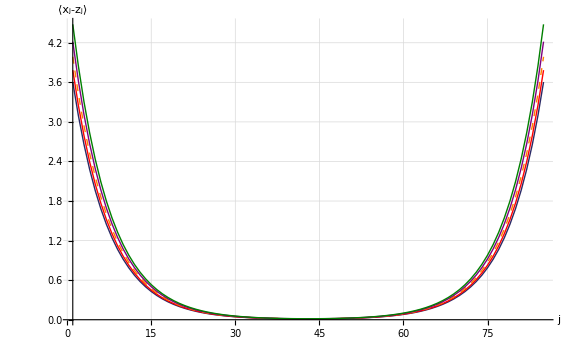
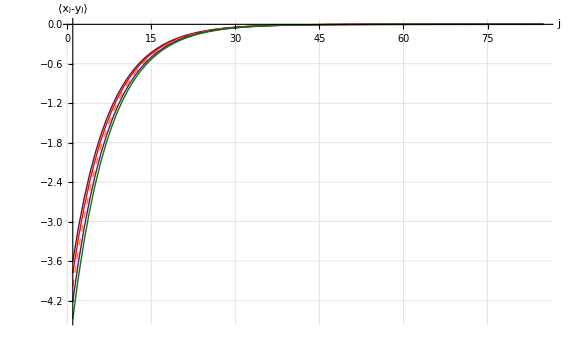

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pxzpair=ListLinePlot[{xzpair[[pos1]],xzpair[[pos2]],xzpair[[pos3]],xzpair[[pos4]],xzpair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-z_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

pxypair=ListLinePlot[{xypair[[pos1]],xypair[[pos2]],xypair[[pos3]],xypair[[pos4]],xypair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-y_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

{pxzpair,pxypair}
```

Analysis

Interpolated Extension = 16.0869

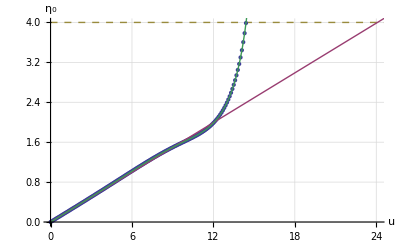

Interpolated Extension = 24.0888

Interpolated Extension = 16.0869\n

```mathematica
y[x_]:=Subscript[η, B]
MXDp1=Plot[y[x],{x,0,umax },PlotStyle->{ColorData[1,3],Dashed}];

MeanAxialDispDataRAW=Flatten[Transpose[Take[Transpose[xzpair],1]]];
maximumValue=Max[MeanAxialDispDataRAW];
positionOfMaximumValue=Flatten[Position[MeanAxialDispDataRAW,maximumValue]][[1]];

MeanAxialDispData = Table[{(i-1)Δ,MeanAxialDispDataRAW[[i]]},{i,1,positionOfMaximumValue}];
MXDp2=ListPlot[MeanAxialDispData];

model=a x  ;
MXDpara=FindFit[Take[MeanAxialDispData,10],model,{a},x];
mxd[u_]:=a u /.MXDpara


mxdInterFunc=Interpolation[MeanAxialDispData];
u=u0/.Quiet[FindRoot[mxd[u0]==Subscript[η, B],{u0,0}]];

MXDp3=Plot[mxd[u0],{u0,0,u+5},PlotStyle->{ColorData[1,2]}];
MXDp4=Plot[mxdInterFunc[x],{x,0,u},PlotRange->All,PlotStyle->ColorData[1,4]];

Show[{MXDp1,MXDp2,MXDp3,MXDp4},PlotRange->{{0,u},{0,Subscript[η, B]}},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["η_0",FontSize->fsAxesLabel]}]
Print["Interpolated Extension = ",u,"\n"]
```

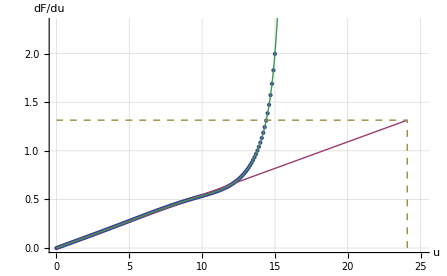

Interpolated Force = 1.31512

```mathematica
FreeEnergyMax=Max[Transpose[dFreeEnergy][[2]]];
positionOfFreeEnergyMax=Flatten[Position[dFreeEnergy,FreeEnergyMax]][[1]];
FreeEnergyData=Table[dFreeEnergy[[i]],{i,1,positionOfFreeEnergyMax}];
FEp1=ListPlot[FreeEnergyData];

model=a x  ;
FEpara=FindFit[Take[FreeEnergyData,10],model,{a},x];
dfe[u0_]:=a u0 /.FEpara
FEp2=Plot[dfe[u0],{u0,0,u},PlotStyle->{ColorData[1,2]}];

dfeInterFunc=Interpolation[FreeEnergyData];
F=dfe[u];


FEp3=Plot[dfeInterFunc[x],{x,0,u},PlotRange->{{0,u},{0,10}},PlotStyle->ColorData[1,4]];


fpos={{u,0},{u,F},{0,F}};
FEp4=ListLinePlot[fpos,PlotStyle->{ColorData[1,3],Dashed}];

Show[{FEp1,FEp2,FEp3,FEp4},PlotRange->{{0,u+1},{0,F+1}},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF/du",FontSize->fsAxesLabel]}]
Print["Interpolated Force = ",F,"\n"]
```

### Force-Extension

```mathematica
Fc=ToForceDimension[F];
U=ToDimension[u];

Print["\nDimensional Force = ",Fc pN,"\nDimensional Extension = ",U Å,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Fc}},"Table"];
```

Dimensional Force = 262.421 pN
Dimensional Extension = 5.00019 Å